# Experiments Analysis :: Héctor Manuel Sánchez Castellanos

## Functions

## Libraries

```mathematica
SetDirectory[NotebookDirectory[]];
(*<<SoNA3BSAnalysis`*)
<<PajaroLocoPublic`
<<HypothesisTesting`
```

## Package Functions

### Descriptions

```mathematica
(*(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------------*)FixBitesListTail::usage="Converts NetLogo bites lists into Mathematica bites lists"
FixBitesListTails::usage="Converts NetLogo experiment bites lists into Mathematica bites lists"
GetExperimentSection::usage="Returns an XML section that is correctly tagged as such"
ConvertTicksToIntegersExperiment::usage="Converts the ticks values to integers in a single experiment"
ConvertTicksToIntegersExperimentsSet::usage="Converts ticks values into integers in an experiments set"
(*-------------------------------------------------------------------ExperimentHeader-------------------------------------------------------------------*)
GetExperimentsSetXMLData::usage="Returns the XML of all the experiments in XML format in the given path (relative to notebook's directory)"
GetExperimentsSetXMLDataAbsolute::usage="Returns the XML of all the experiments in XML format in the given absolute path"
GetExperimentHeader::usage="Returns the header section of an experiment in list form"
GetExperimentHeaderWithFixedDate::usage="Returns the header of an experiment with the date fixed to mathematica standard"
GetExperimentsSetHeader::usage="Returns the header of a set of experiments with the dates as a range (requires that the section is tagged: 'header')"
GetExperimentParameters::usage="Returns the parameters of a given experiment"
GetExperimentsSetParameters::usage="Returns the parameters that define the behavior of a set of experiments with the independent variables ordered (requires that the section is tagged: 'parameters')"
(*-------------------------------------------------------------------DirectContact----------------------------------------------------------------------*)
GetExperimentContactLabels::usage="Returns the names of the individuals involved in contacts situations of an experiment"
GetExperimentsSetContactLabels::usage="Returns the unrepeated names of the individuals involved in contacts situations of a set of experiments"
GetContactTally::usage="Returns the transition contacts counts"
GetExperimentContactsSection::usage="Returns the contacts section of a single experiment"
GetExperimentsSetContactsSection::usage="Returns the contacts section of a set of experiments"
GetExperimentContactsTransitionsWithPattern::usage="Returns the contacts matrix of an experiment given a labels pattern"
GetExperimentSetRawContactsTransitionsWithPattern::usage="Returns the individual contacts matrices of every experiment of a set"
GetExperimentSetContactsTransitionsWithPattern::usage="Returns the contacts matrix of a set of experiments given a labels pattern with the given mix function applied to the matrices"
FilterBetweenTicksExperiment::usage="Filters all the contacts that do not happen between the given ticks period"
FilterBetweenTicksExperimentSet::usage="Filters all the contacts that do not happen between the given ticks period in an experiments set"
GetExperimentSetContactsTransitionsWithPatternInIntervals::usage="Returns the contact matrices divided un fixed time intervals (cumulative)"
(*-------------------------------------------------------------------BitesContact-----------------------------------------------------------------------*)
GetExperimentBiteLabels::usage="Returns the names of the individuals involved in bites situations of an experiment"
GetExperimentsSetBiteLabels::usage="Returns the names of the individuals involved in bites situations of a set of experiments"
GetExperimentBitesSection::usage="Returns the bites section of a single experiment"
GetExperimentsSetBitesSection::usage="Returns the bites section of a set of experiments"
GetBitesLists::usage="Returns the bite lists of the experiments"
GetBitesTransitions::usage="Converts the bite lists into transitions lists"
GetBitesTransitionsCases::usage="Filters the bites in cases"
GetTransitionFrequencies::usage="Returns the transitions frequencies of a list of bites"
GetExperimentTransitionFrequencies::usage="Returns the transitions frequencies of an experiment"
GetExperimentTransitionFrequenciesFromTail::usage="Returns the transitions frequencies of an experiment from the tail section"
GetExperimentBitesTransitionsWithPattern::usage="Returns the bites transitions matrix from an experiment"
GetExperimentsSetRawBitesTransitionsWithPattern::usage="Returns the bites transitions of a set of experiments individualy"
GetExperimentsSetBitesTransitionsWithPattern::usage="Returns the bites transitions from a set of experiments"
(*-------------------------------------------------------------------HousesContact-------------------------------------------------------------------*)
GetExperimentHousesLabels::usage="Returns the names of the houses entities on an experiment"
GetExperimentsSetHousesLabels::usage="Returns the names of the houses entities on the experiments set"
GetHousesContactTally::usage="*Returns the tally of contacts with houses entities"
GetExperimentsSetHousesContactsSection::usage="Returns the houses contacts section of a set of experiments"
GetExperimentHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiment"
GetExperimentsSetHousesContactsTransitionsWithPattern::usage="Returns the houses contacts of an experiments set"
GetExperimentsSetRawHousesContactsTransitionsWithPattern::usage="Returns the individual experiments matrices of an experiments set"
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentTicksOutputs::usage="Returns the ticks outputs of an experiment"
GetExperimentsSetTicksOutputs::usage="Returns the ticks outputs of a set of experiments"
GetExperimentOutputTags::usage="Returns the names of the outputs of an experiment"
GetTaggedOutputFromExperimentsIndexes::usage="Returns the tick output of a given XML tag from the samples provided by the list of indexes (on the imported XML list of samples)"
GetExperimentSetIndexPositionsByIndependentVariableValues::usage="Returns the indexes that contain the combination of independent variables values"
GetExperimentSetTaggedOutputByIndependentVariableValues::usage="Returns the tagged output values of the samples that contain the combination of independent variables values (the return list of lists is ordered by ticks)"
GetExperimentSetIndexPositionsByIndependentVariableBins::usage="Returns the indexes (on the imported XML list of samples) from the samples that contain a certain combination of independent variables"
(*-------------------------------------------------------------------SCEIR Dynamics-----------------------------------------------------------------------*)
SCEIRInitializePersonsVectors::usage="Returns the initialized state vectors with the given indexes cases"
SCEIRInitializeCounterVectors::usage="Returns the initialized count vectors with zero values for each of them"
SCEIRInitializeVectors::usage="Initializes both vectors"
SCEIRUpdateCounters::usage="Updates the counters for each of the individuals in each state"
SCEIRTransitionState::usage="Returns the positions of the individuals that should make a transition given a state and threshold for counter"
SCEIRGenerateContagionMatrix::usage="Returns the bool values of the probabilities of an individual infecting the others without taking into account if the individual is himself in Infected state"
SCEIRGeneratePopulationContagionsMatrix::usage="Returns the matrix of the individuals being infected (columns) by others (rows)"
SCEIRUpdatePersonsVectorWithCondemnedIndividuals::usage="Returns the updated population vector with the replaced condemned individuals"
SCEIRSpreadDisease::usage="Spreads the disease between contacts probabilistically according to their contacts matrices"
SCEIRRunEpidemicEpoch::usage="Spread a disease through one epoch between the population in a network"
SCEIRNetworkEpidemicListEpochs::usage="Spreads a disease in a network returning the persons and counter vectors for each epoch"
SCEIRNetworkEpidemic::usage="Spread a disease in a network returning the persons and counter vectors for the last epoch"
SCEIRGenerateListPlotLists::usage="Returns the epidemic process lists so that they can be plotted"
SCEIRGraphEpidemicProcess::usage="Generates a graph of each step of the epidemic process"
SCEIRListPlotEpidemicProcess::usage="Generates a list plot of each step of the epidemic process"
SCEIRMatrixPlots::usage="Generates a Matrix Plot representation of each of the states in the epidemic process"
SCEIRGenerateMatrixPlotMatrices::usage="Generates a full condensed matrix for a matrix plot of the epidemic process"
(*-------------------------------------------------------------------SEIR Dynamics-----------------------------------------------------------------------*)
SEIRInitializePersonsVectors::usage=""
SEIRInitializeCounterVectors::usage=""
SEIRInitializeVectors::usage=""
SEIRUpdateCounters::usage=""
SEIRTransitionState::usage=""
SEIRGenerateContagionMatrix::usage=""
SEIRGeneratePopulationContagionsMatrix::usage=""
SEIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SEIRSpreadDisease::usage=""
SEIRRunEpidemicEpoch::usage=""
SEIRNetworkEpidemicListEpochs::usage=""
SEIRNetworkEpidemic::usage=""
SEIRGraphEpidemicProcess::usage=""
SEIRGenerateListPlotLists::usage=""
SEIRListPlotEpidemicProcess::usage=""
SEIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIR Dynamics-----------------------------------------------------------------------*)
SIRInitializePersonsVectors::usage=""
SIRInitializeCounterVectors::usage=""
SIRInitializeVectors::usage=""
SIRUpdateCounters::usage=""
SIRTransitionState::usage=""
SIRGenerateContagionMatrix::usage=""
SIRGeneratePopulationContagionsMatrix::usage=""
SIRUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SIRSpreadDisease::usage=""
SIRRunEpidemicEpoch::usage=""
SIRNetworkEpidemicListEpochs::usage=""
SIRNetworkEpidemic::usage=""
SIRGraphEpidemicProcess::usage=""
SIRGenerateListPlotLists::usage=""
SIRListPlotEpidemicProcess::usage=""
SIRGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------SIS Dynamics-----------------------------------------------------------------------*)
SISInitializePersonsVectors::usage=""
SISInitializeCounterVectors::usage=""
SISInitializeVectors::usage=""
SISUpdateCounters::usage=""
SISTransitionState::usage=""
SISGenerateContagionMatrix::usage=""
SISGeneratePopulationContagionsMatrix::usage=""
SISUpdatePersonsVectorWithCondemnedIndividuals::usage=""
SISSpreadDisease::usage=""
SISRunEpidemicEpoch::usage=""
SISNetworkEpidemicListEpochs::usage=""
SISNetworkEpidemic::usage=""
SISGraphEpidemicProcess::usage=""
SISGenerateListPlotLists::usage=""
SISListPlotEpidemicProcess::usage=""
SISGenerateMatrixPlotMatrices::usage=""
(*-------------------------------------------------------------------Wrappers-----------------------------------------------------------------------*)
NetworkEpidemicListEpochs::usage="Simulates an epidemic returning the stages of the process"
GenerateListPlotLists::usage="Generates the list plots lists of the process"
ListPlotEpidemic::usage="Generates the final list plot of the process"
GenerateMatrixPlotMatrix::usage="Generates the final matrix of the process"
MatrixPlotEpidemic::usage="Generates the final matrix plot"
GraphEpidemicProcess::usage="Generates the graphs of each stage of the epidemic process"
ListPlotEpidemicProcess::usage="List plots an epidemic process in each stage"
MatrixPlotEpidemicProcess::usage="Generates the matrix plots at each stage of the process"
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------------------*)
GraphTransitionsFrequenciesSet::usage="Graphs a transitions frequencies set of matrices scaled to a global max of contacts"
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------------------*)
Summary::usage=""
NetworkEpidemicListEpochsRepeatOnIndexes::usage=""
NetworkEpidemicListEpochsRepeatSweep::usage=""
ListPlotRepeatOnIndexes::usage=""
MatrixPlotRepeatOnIndexes::usage=""*)
```

### Auxiliary

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)(*-------------------------------------------------------------------Auxiliary-------------------------------------------------------------------*)FixBitesListTail[experimentTail_]:=(StringReplace[#,{"["->" ","]"->" "," "->","}]//ToString//ToExpression)&/@experimentTail
FixBitesListTails[experimentsTails_]:=FixBitesListTail/@experimentsTails
GetExperimentSection[xmlExperimentData_,sectionTitle_]:=Cases[xmlExperimentData,XMLElement[sectionTitle,_,_],Infinity]
ConvertTicksToIntegersExperiment[cSectExperiment_]:=Module[{cSectOne=cSectExperiment,heads,tails,tailsFixed},heads=cSectOne[[All,1]];
tails=cSectOne[[All,2;;All]];
tailsFixed=Table[{#[[1]],#[[2]]//ToExpression}&/@tails[[i]],{i,1,tails//Length}];
(Prepend[#[[2]],#[[1]]]&/@({heads,tailsFixed}//Transpose))]
ConvertTicksToIntegersExperimentsSet[cSect_]:=ConvertTicksToIntegersExperiment/@cSect
```

### Head

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------ExperimentHeader------------------------------------------------------------*)
GetExperimentsSetXMLData[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",Directory[]<>path];
Import/@allFilesPaths]
GetExperimentsSetXMLDataAbsolute[path_]:=Module[{filesNames,allFilesPaths},allFilesPaths=FileNames["*.xml",path];
Import/@allFilesPaths]
GetExperimentHeader[xmlExperimentData_]:=Module[{temp},temp=GetExperimentSection[xmlExperimentData,"header"];
Cases[temp,XMLElement[a_,_,{c_}]->{a,c},{3}]]
GetExperimentHeaderWithFixedDate[xmlExperimentData_]:=Module[{header,datePosition},header=GetExperimentHeader[xmlExperimentData];
datePosition=(Position[header,{"date",_}]//Flatten)[[1]];
ReplacePart[header,{3,2}->DateList[header[[datePosition]][[2]]]]]
GetExperimentsSetHeader[xmlExperimentsDataSet_]:=Module[{headers,datePosition,sorted,dateRange},headers=(GetExperimentHeaderWithFixedDate[#]&/@xmlExperimentsDataSet);
datePosition=(Position[headers[[1]],{"date",_}]//Flatten)[[1]];
sorted=headers[[All,datePosition]][[All,2]]//Sort;
dateRange=DateString/@{sorted//First,sorted//Last};
ReplacePart[headers[[1]],datePosition->{"date",dateRange}]]
GetExperimentParameters[xmlExperimentData_]:=Module[{temp},temp=GetExperimentSection[xmlExperimentData,"parameters"];
Cases[temp,XMLElement[a_,{"id"->b_},{c_}]->{a,b,c},{3}]]
GetExperimentsSetParameters[xmlExperimentsDataSet_]:=Module[{experimentsData,independentPositions,independentTriplets,independentRanges,replacementRules},experimentsData=GetExperimentParameters[#]&/@xmlExperimentsDataSet;
independentPositions=Position[experimentsData[[1]],{"independent",_,_}]//Flatten;
independentTriplets=experimentsData[[All,#]]&/@independentPositions;
independentRanges=DeleteDuplicates/@(ToExpression/@(#[[All,3]]&/@independentTriplets));
replacementRules={#[[1]],3}->#[[2]]&/@({independentPositions,independentRanges}//Transpose);
ReplacePart[experimentsData[[1]],replacementRules]]
```

### Body

```mathematica
FilterBetweenTicksExperiment[fixedTicksCSect_,low_,high_]:=Module[{expCSect=fixedTicksCSect,section},Table[section=expCSect[[i]];
Cases[section[[2;;All]],{a_,b_}/;(b≥low&&b≤high)]//Prepend[#,section[[1]]]&,{i,1,expCSect//Length}]]
FilterBetweenTicksExperimentSet[cSect_,low_,high_]:=FilterBetweenTicksExperiment[#,low,high]&/@cSect
(*DirectContact*)
GetExperimentContactLabels[contactsSection_]:=Module[{b},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
b[[All,1]]]
GetExperimentsSetContactLabels[contactsSections_]:=(GetExperimentContactLabels/@contactsSections)//Flatten//DeleteDuplicates//Sort
GetContactTally[contactsSectionPart_]:=Module[{individual,contacts},individual=contactsSectionPart[[All,1]][[1]];
contacts=contactsSectionPart[[All,1]]//Drop[#,1]&//Tally;
{individual,contacts}]
GetExperimentContactsSection[experimentXMLData_]:=GetExperimentsSetContactsSection[{experimentXMLData}][[1]]
GetExperimentsSetContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails//ConvertTicksToIntegersExperimentsSet]
GetExperimentContactsTransitionsWithPattern[contactsSection_,pattern_]:=Module[{b,c},b=(GetContactTally[#]&/@contactsSection)//Sort[#]&;
c=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@pattern,{i,1,pattern//Length}];
{c,pattern}]
GetExperimentSetRawContactsTransitionsWithPattern[contactsSections_,pattern_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]],contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPattern[contactsSections_,pattern_,mixFunction_]:=Module[{contacts},contacts=GetExperimentContactsTransitionsWithPattern[#,pattern]&/@contactsSections;
{contacts[[All,1]]//mixFunction,contacts[[1,2]]}]
GetExperimentSetContactsTransitionsWithPatternInIntervals[fixedTicksCSect_,labels_,mixFunction_,frames_]:=Module[{max,increment,low,high,fCSect,intervals},max=fixedTicksCSect[[1]][[All,2;;All]][[All,All,2]]//Flatten//Max;
increment=max/frames;
intervals=Table[low=0;high=i;
fCSect=FilterBetweenTicksExperimentSet[fixedTicksCSect,low,high];
GetExperimentSetContactsTransitionsWithPattern[fCSect,labels,mixFunction],{i,0,max,increment}]]
```

### Tail

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------BitesContact-------------------------------------------------------------------*)
GetExperimentBiteLabels[bites_]:=GetExperimentsSetBiteLabels[{bites}]
GetExperimentsSetBiteLabels[bites_]:=Module[{flat},flat=bites//Flatten//DeleteDuplicates;
Cases[flat,a_/;StringMatchQ[a,LetterCharacter..]]//Sort]
GetExperimentBitesSection[experimentXMLData_]:=GetExperimentsSetBitesSection[{experimentXMLData}][[1]]
GetExperimentsSetBitesSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"biteList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetBitesLists[fixedListsTails_]:=Map[#[[All,1]]&,Map[Drop[#,1]&,#]]&/@fixedListsTails
GetBitesTransitions[bitesLists_]:=((Partition[#,2,1]&/@#)//Flatten[#,1]&)&/@bitesLists
GetBitesTransitionsCases[bitesTransitions_]:=bitesTransitions//Flatten//DeleteDuplicates//Tuples[#,2]&
GetTransitionFrequencies[bitesTransitions_,agentsNames_]:=Module[{matrices},matrices=Table[Table[Count[j,{agentsNames[[i]],#}]&/@agentsNames,{i,1,agentsNames//Length}],{j,bitesTransitions}];
{matrices,ConstantArray[agentsNames,matrices//Length]}//Transpose]
GetExperimentTransitionFrequencies[transitionFrequencies_,mixFunction_]:={transitionFrequencies[[All,1]]//mixFunction,transitionFrequencies[[1,2]]}
GetExperimentTransitionFrequenciesFromTail[fixedListsTails_,pattern_,mixFunction_]:=Module[{bitesLists,bitesTransitions,agentsNames,transitionFrequencies},bitesLists=GetBitesLists[fixedListsTails];
bitesTransitions=GetBitesTransitions[bitesLists];
(*agentsNames=GetAgentsNames[bitesTransitions];*)transitionFrequencies=GetTransitionFrequencies[bitesTransitions,pattern];
GetExperimentTransitionFrequencies[transitionFrequencies,mixFunction]]
GetExperimentBitesTransitionsWithPattern[bitesExperimentList_,pattern_]:=GetExperimentTransitionFrequenciesFromTail[{bitesExperimentList},pattern,Total]
GetExperimentsSetRawBitesTransitionsWithPattern[bitesList_,pattern_]:={(GetExperimentTransitionFrequenciesFromTail[{#},pattern,Total]&/@bitesList)[[All,1]],pattern}
GetExperimentsSetBitesTransitionsWithPattern[bitesList_,pattern_,mixFunction_]:=GetExperimentTransitionFrequenciesFromTail[bitesList,pattern,mixFunction]
(*HouseContact*)
GetExperimentHousesLabels[contactsSection_]:=GetExperimentsSetHousesLabels[{contactsSection}]
GetExperimentsSetHousesLabels[contactsSection_]:=Module[{a,houses},Table[a=GetHousesContactTally[contactsSection[[i]]];
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort,{i,1,contactsSection//Length}]//Flatten//Sort//DeleteDuplicates]
GetHousesContactTally[contactsSectionPart_]:=Module[{housesNames,individualsNames,tallys},housesNames=Table[i[[All,1]],{i,contactsSectionPart[[All,2;;All]]}]//Flatten//DeleteDuplicates//Sort;
individualsNames=contactsSectionPart[[All,1]];
tallys=Tally/@contactsSectionPart[[All,2;;All,1]];
{individualsNames,tallys}//Transpose]
GetExperimentsSetHousesContactsSection[experimentsXMLData_]:=Module[{output,bitesListRaw,fixedListsTails},output=GetExperimentSection[#,"output"]&/@experimentsXMLData;
bitesListRaw=Map[Cases[#,XMLElement["output",{"id"->"contactHousesList"},a_]->a]&,output];(*Lists Tails with data in String form*)fixedListsTails=Map[ToString,FixBitesListTails[bitesListRaw],{5}][[All,1]];(*List Tails with data in Data form*)fixedListsTails]
GetExperimentHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{a,persons=patternPersons,houses=patternHouses,partial,matrix,transitions,b,c,labels},a=GetHousesContactTally[contactsSection];
b=a//Sort;
persons=b[[All,1]]//Flatten;
houses=Flatten[a[[All,2]],1][[All,1]]//DeleteDuplicates//Sort;
labels={persons,houses}//Flatten;
partial=Table[If[Count[b[[i,2]],{#,_}]>0,b[[i,2]][[Position[b[[i,2]],#][[1]][[1]],2]],0]&/@labels,{i,1,b//Length}];
matrix={partial,ConstantArray[ConstantArray[0,partial[[1]]//Length],houses//Length]}//Flatten[#,1]&;
transitions={matrix,labels}]
GetExperimentsSetRawHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]],matrices[[1,2]]}]
GetExperimentsSetHousesContactsTransitionsWithPattern[contactsSection_,patternPersons_,patternHouses_,mixFunction_]:=Module[{matrices},matrices=GetExperimentHousesContactsTransitionsWithPattern[#,patternPersons,patternHouses]&/@contactsSection;
{matrices[[All,1]]//mixFunction,matrices[[1,2]]}]
```

### SIS

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIS-------------------------------------------------------------------*)
SISInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
{sPersonsVct*(1-iPersonsVct),iPersonsVct}]
SISInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct}]
SISInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SISUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SISTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex-1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex-1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SISGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SISGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SISSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SISGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SISGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SISUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SISRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SISUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SISTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SISSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SISNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SISInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SISRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SISNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SISGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SISGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SISListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SISListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SISGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected"},PlotStyle->{Blue,Green}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SISGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SIR-------------------------------------------------------------------*)
SIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),iPersonsVct,rPersonsVct}]
SIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,iCounterVct,rCounterVct}]
SIRInitializeVectors[indexesCases_,populationSize_]:={SIRInitializePersonsVectors[indexesCases,populationSize],SIRInitializeCounterVectors[populationSize]}
SIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[2]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(I->R)*){personsVcts,counterVcts}=SIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
(*ContagionProcess*){personsVcts,counterVcts}=SIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Green],Style[#[[3]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Infected","Recovered"},PlotStyle->{Blue,Green,Purple}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
Total[{suceptible,infected,recovered}]]
```

### SEIR

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SEIR-------------------------------------------------------------------*)
SEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),ePersonsVct,iPersonsVct,rPersonsVct}]
SEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SEIRInitializeVectors[indexesCases_,populationSize_]:={SEIRInitializePersonsVectors[indexesCases,populationSize],SEIRInitializeCounterVectors[populationSize]}
SEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[3]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(E->I->R)*){personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
(*ContagionProcess*){personsVcts,counterVcts}=SEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
Total[{suceptible,exposed,infected,recovered}]]
```

### SCEIR

```mathematica
(*+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------SCEIR-------------------------------------------------------------------*)
SCEIRInitializePersonsVectors[indexesCases_,populationSize_]:=Module[{sPersonsVct,cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct},sPersonsVct=ConstantArray[1,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[0,indexesCases//Length]}//Transpose)]&;
cPersonsVct=ConstantArray[0,populationSize];
ePersonsVct=ConstantArray[0,populationSize];
iPersonsVct=ConstantArray[0,populationSize]//ReplacePart[#,#[[1]]->#[[2]]&/@({indexesCases,ConstantArray[1,indexesCases//Length]}//Transpose)]&;
rPersonsVct=ConstantArray[0,populationSize];
{sPersonsVct*(1-iPersonsVct),cPersonsVct,ePersonsVct,iPersonsVct,rPersonsVct}]
SCEIRInitializeCounterVectors[populationSize_]:=Module[{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct},sCounterVct=ConstantArray[0,populationSize];
cCounterVct=ConstantArray[0,populationSize];
eCounterVct=ConstantArray[0,populationSize];
iCounterVct=ConstantArray[0,populationSize];
rCounterVct=ConstantArray[0,populationSize];
{sCounterVct,cCounterVct,eCounterVct,iCounterVct,rCounterVct}]
SCEIRInitializeVectors[indexesCases_,populationSize_]:={SCEIRInitializePersonsVectors[indexesCases,populationSize],SCEIRInitializeCounterVectors[populationSize]}
SCEIRUpdateCounters[personsVcts_,counterVcts_]:={personsVcts,personsVcts+counterVcts}
SCEIRTransitionState[personsVcts_,counterVcts_,threshold_,stateIndex_]:=Module[{affectedPersons,affectedCounters,intersection,personsReplacement0,personsReplacement1,personsVctsReplaced},(*Get indexes of interest*)affectedPersons=Position[personsVcts[[stateIndex]],1];
affectedCounters=Position[counterVcts[[stateIndex]],a_/;a≥threshold];
intersection=Intersection[affectedPersons,affectedCounters]//Flatten;
(*Replace in persons vectors section*)personsReplacement0=ReplacePart[personsVcts[[stateIndex]],(#->0)&/@intersection];
personsReplacement1=ReplacePart[personsVcts[[stateIndex+1]],(#->1)&/@intersection];
(*Replace in persons vector*)personsVctsReplaced=ReplacePart[personsVcts,{stateIndex->personsReplacement0,(stateIndex+1)->personsReplacement1}];
(*Return vectors*){personsVctsReplaced,counterVcts}]
SCEIRGenerateContagionMatrix[contactsMatrix_,infectionProb_,populationSize_]:=Module[{contagionProbabilites,randomMatrix},contagionProbabilites=1-infectionProb^contactsMatrix;
randomMatrix=RandomReal[{0,1},{populationSize,populationSize}];
Map[Map[If[#[[1]]>#[[2]],1,0]&,#//Transpose]&,{contagionProbabilites,randomMatrix}//Transpose]]
SCEIRGeneratePopulationContagionsMatrix[personsVcts_,contagionMatrix_]:=Module[{suceptible,infective,infMatrix,sucMatrix},suceptible=personsVcts[[1]];
infective=personsVcts[[4]];
infMatrix=infective*contagionMatrix;
sucMatrix=(suceptible*(contagionMatrix//Transpose))//Transpose;
infMatrix*sucMatrix]
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix_,personsVcts_,counterVcts_]:=Module[{condemnedIndividuals,suceptibles,condemned},condemnedIndividuals=Position[Total/@(condemnedMatrix//Transpose),a_/;a≥1];
suceptibles=ReplacePart[personsVcts[[1]],#[[1]]->0&/@condemnedIndividuals];
condemned=ReplacePart[personsVcts[[2]],#[[1]]->1&/@condemnedIndividuals];
{ReplacePart[personsVcts,{1->suceptibles,2->condemned}],counterVcts}]
SCEIRSpreadDisease[contactsMatrix_,infectionProb_,personsVcts_,counterVcts_]:=Module[{contagionMatrix,condemnedMatrix},contagionMatrix=SCEIRGenerateContagionMatrix[contactsMatrix,infectionProb,contactsMatrix//Length];
condemnedMatrix=SCEIRGeneratePopulationContagionsMatrix[personsVcts,contagionMatrix];
SCEIRUpdatePersonsVectorWithCondemnedIndividuals[condemnedMatrix,personsVcts,counterVcts]]
SCEIRRunEpidemicEpoch[personsVctsIn_,counterVctsIn_,thresholds_,infectionProbability_,contactsMatrix_]:=Module[{personsVcts=personsVctsIn,counterVcts=counterVctsIn,infectionProb=infectionProbability},(*UpdateCounters*){personsVcts,counterVcts}=SCEIRUpdateCounters[personsVcts,counterVcts];
(*TransitionBetweenStates(C->E->I->R)*){personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[2]],2];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[3]],3];
{personsVcts,counterVcts}=SCEIRTransitionState[personsVcts,counterVcts,thresholds[[4]],4];
(*ContagionProcess*){personsVcts,counterVcts}=SCEIRSpreadDisease[contactsMatrix,infectionProb,personsVcts,counterVcts];
(*ReturnValues*){personsVcts,counterVcts,thresholds,infectionProbability,contactsMatrix}]
SCEIRNetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=NestList[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[All,1]],output[[All,2]]}]
SCEIRNetworkEpidemic[thresholds_,infectionProb_,contactsMatrix_,indexesCases_,epochs_]:=Module[{personsVcts,counterVcts,output},{personsVcts,counterVcts}=SCEIRInitializeVectors[indexesCases,contactsMatrix//Length];
output=Nest[Apply[SCEIRRunEpidemicEpoch,#]&,{personsVcts,counterVcts,thresholds,infectionProb,contactsMatrix},epochs];
{output[[1]],output[[2]]}]
edgesShape[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]};
Options[SCEIRGraphEpidemicProcess]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgesShape,VertexLabelStyle->{Italic}}
SCEIRGraphEpidemicProcess[contactsMatrix_,epidemic_,OptionsPattern[]]:=Module[{graph=contactsMatrix,positions,development},positions=Map[ToString/@((Position[#,1]//Flatten))&,epidemic[[1]],{2}];
graph=GraphTransitionsFrequencies[{contactsMatrix,ToString/@Range[contactsMatrix//Length]},LineThickness->OptionValue[LineThickness],ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]];
development=HighlightGraph[graph,{Style[#[[1]],Blue],Style[#[[2]],Orange],Style[#[[3]],Green],Style[#[[4]],Red],Style[#[[5]],Purple]},ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@positions]
SCEIRGenerateListPlotLists[epidemicIndividuals_]:=Map[Total,epidemicIndividuals,{2}]//Transpose
Options[SCEIRListPlotEpidemicProcess]:={Joined->True,InterpolationOrder->2,ImageSize->Automatic}
SCEIRListPlotEpidemicProcess[epidemicSCEIR_,epochs_,OptionsPattern[]]:=Table[ListPlot[SCEIRGenerateListPlotLists[epidemicSCEIR[[1,1;;i]]],Joined->OptionValue[Joined],ImageSize->OptionValue[ImageSize],InterpolationOrder->OptionValue[InterpolationOrder],PlotRange->{{0,epochs},{0,(epidemicSCEIR[[1,1,1]]//Length)+Ceiling[(epidemicSCEIR[[1,1,1]]//Length)*.25]}},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]//Quiet,{i,1,epidemicSCEIR[[1]]//Length}]
SCEIRMatrixPlots[epidemicSCEIR_]:=Table[i//MatrixPlot,{i,(epidemicSCEIR[[1]]//Transpose)}]
SCEIRGenerateMatrixPlotMatrices[epidemicSCEIR_]:=Module[{suceptible,condemned,exposed,infected,recovered},suceptible=(#/.{1->-10})&/@((epidemicSCEIR[[1]]//Transpose)[[1]]);
condemned=(#/.{1->-5})&/@((epidemicSCEIR[[1]]//Transpose)[[2]]);
exposed=(#/.{1->0})&/@((epidemicSCEIR[[1]]//Transpose)[[3]]);
infected=(#/.{1->5})&/@((epidemicSCEIR[[1]]//Transpose)[[4]]);
recovered=(#/.{1->10})&/@((epidemicSCEIR[[1]]//Transpose)[[5]]);
Total[{suceptible,condemned,exposed,infected,recovered}]]
```

### Graphs

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Graphs-------------------------------------------------------------------*)
Options[GraphTransitionsFrequenciesSet]:={LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic}}
GraphTransitionsFrequenciesSet[matricesSet_,OptionsPattern[]]:=GraphTransitionsFrequenciesWithMax[#,matricesSet[[All,1]]//Flatten//Max,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle],GraphLayout->OptionValue[GraphLayout],ImageSize->OptionValue[ImageSize],VertexSize->OptionValue[VertexSize],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexLabelStyle->OptionValue[VertexLabelStyle]]&/@matricesSet
```

### Epidemic Wrappers

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------EpidemicWrappers---------------------------------------------------------*)
NetworkEpidemicListEpochs[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SIR",SIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SEIR",SEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs],"SCEIR",SCEIRNetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs]]]
GenerateListPlotLists[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGenerateListPlotLists[epidemicData[[1]]],"SIR",SIRGenerateListPlotLists[epidemicData[[1]]],"SEIR",SEIRGenerateListPlotLists[epidemicData[[1]]],"SCEIR",SCEIRGenerateListPlotLists[epidemicData[[1]]]]]
Options[ListPlotEpidemic]:={Joined->True,Thickness->.005}
ListPlotEpidemic[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{listPlotData},listPlotData=GenerateListPlotLists[epidemicData,epidemicType];
Switch[epidemicType,"SIS",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected"}],"SIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Infected","Recovered"}],"SEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Exposed","Infected","Recovered"}],"SCEIR",ListPlot[listPlotData,Joined->OptionValue[Joined],PlotStyle->{{PointSize[.0075],Thickness->OptionValue[Thickness]}},InterpolationOrder->2,PlotRange->{0,(epidemicData[[1,1,1]]//Length)+Ceiling[(epidemicData[[1,1,1]]//Length)*.25]},PlotLegends->{"Suceptible","Condemned","Exposed","Infected","Recovered"}]]]
GenerateMatrixPlotMatrix[epidemicData_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SISGenerateMatrixPlotMatrices[epidemicData],"SIR",SIRGenerateMatrixPlotMatrices[epidemicData],"SEIR",SEIRGenerateMatrixPlotMatrices[epidemicData],"SCEIR",SCEIRGenerateMatrixPlotMatrices[epidemicData]]]
MatrixPlotEpidemic[epidemicData_,epidemicType_]:=Module[{},MatrixPlot[GenerateMatrixPlotMatrix[epidemicData,epidemicType],PlotTheme->"Scientific"]]
GraphEpidemicProcess[epidemicData_,contactsMatrix_,epidemicType_]:=Module[{},Switch[epidemicType,"SIS",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SIR",SIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SEIR",SEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic],"SCEIR",SCEIRGraphEpidemicProcess[contactsMatrix,epidemicData,ImageSize->1000,EdgeShapeFunction->edgesShape,LineThickness->.001,GraphLayout->Automatic]]]
ListPlotEpidemicProcess[epidemicData_,epidemicType_,OptionsPattern[]]:=Module[{},Switch[epidemicType,"SIS",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SIR",SIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SEIR",SEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000],"SCEIR",SCEIRListPlotEpidemicProcess[epidemicData,epidemicData[[1]]//Length,ImageSize->1000]]]
MatrixPlotEpidemicProcess[epidemicData_,epidemicType_]:=Table[MatrixPlot[epidemicData[[1,i]]],{i,1,epidemicData[[1]]//Length}]
```

### Dynamics

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------PopulationDynamics-------------------------------------------------------------------*)
GetExperimentOutputTags[experimentsXMLData_]:=Module[{output},output=GetExperimentSection[experimentsXMLData[[1]],"output"];
{"outputs",Cases[output,XMLElement[_,{"id"->a_},_]->a]//DeleteDuplicates}]
GetExperimentSetIndexPositionsByIndependentVariableBins[experimentsXMLData_]:=Module[{parametersList,indParPos,indParVal,tuples,patterns,constant,indParList,tuplesPositions},parametersList=GetExperimentParameters[#]&/@experimentsXMLData;
indParPos=GetExperimentsSetParameters[experimentsXMLData]//Position[#,{"independent",_,_}]&//Flatten;
indParVal=(GetExperimentsSetParameters[experimentsXMLData]//Cases[#,{"independent",_,a_}->a]&);
tuples=Tuples[indParVal];
patterns=Table[constant=ConstantArray[{_,_,"dummy"},parametersList[[1]][[indParPos]]//Length];
ReplacePart[constant[[j]],3->tuples[[i]][[j]]],{i,1,tuples//Length},{j,1,tuples[[1]]//Length}];
indParList=#[[indParPos]]&/@parametersList;
tuplesPositions=Position[ToExpression/@indParList,#]&/@patterns;
{tuplesPositions,tuples}//Transpose]
GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_]:=Module[{relationTable,index},relationTable=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSampleData];
index=Position[relationTable[[All,2]],independentVariablesValuesList]//Flatten;
(relationTable[[#,1]]&/@index)//Flatten]
GetTaggedOutputFromExperimentsIndexes[experimentsXMLData_,positionsList_,outputTag_]:=Module[{experimentsOutputsSections,output},experimentsOutputsSections=GetExperimentSection[#,"output"]&/@experimentsXMLData[[positionsList]];
output=Cases[#,XMLElement["output",{"id"->outputTag},{a_}]->a]&/@experimentsOutputsSections;
Map[ToExpression,output,Infinity]]
GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSampleData_,independentVariablesValuesList_,outputTag_]:=Module[{indexes},indexes=GetExperimentSetIndexPositionsByIndependentVariableValues[xmlSampleData,independentVariablesValuesList];
GetTaggedOutputFromExperimentsIndexes[xmlSampleData,indexes,outputTag]//Transpose]
GetExperimentTicksOutputs[xmlSampleData_]:=Module[{fixed,tickXML,test,test2,out},tickXML=GetExperimentSection[xmlSampleData,"tick"];
test=Cases[tickXML,XMLElement["tick",{"id"->a_},b__]->{a,b}];
test2=(test[[All,2]][[#]]//Cases[#,XMLElement[_,{"id"->c_},{d_}]->{c,d}]&)&/@Range[test//Length];
out={{ConstantArray["Tick",test//Length],test[[All,1]]}//Transpose,test2}//Transpose;
fixed=(Prepend[#[[2]],#[[1]]]&/@out)//Transpose;
Prepend[#[[All,2]]&/@fixed,fixed[[All,1,1]]]]
GetExperimentsSetTicksOutputs[xmlSet_]:=Module[{a},a=GetExperimentTicksOutputs[#]&/@xmlSet;
{a[[1,1]],{a[[All,2;;All]]}}]
```

### Sweeps

```mathematica
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
(*-------------------------------------------------------------------Sweeps-------------------------------------------------------------------*)
Summary[epidemicData_,epidemicMatrix_,epidemicType_]:=Module[{listPlot,matrixPlot,graph},listPlot=ListPlotEpidemic[epidemicData,epidemicType,Joined->True];
matrixPlot=MatrixPlotEpidemic[epidemicData,epidemicType];
graph=GraphEpidemicProcess[epidemicData,epidemicMatrix[[1]],epidemicType]//Last;
Grid[{{"Development",Grid[{{listPlot,matrixPlot}}]},{"Graph",graph}},Frame->All,Background->{{LightBlue},None}]]
NetworkEpidemicListEpochsRepeatOnIndexes[thresholds_,infectionProb_,contactsMatrixEpidemic_,indexesCases_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,indexesCases,epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}}]
NetworkEpidemicListEpochsRepeatSweep[thresholds_,infectionProb_,contactsMatrixEpidemic_,epochs_,epidemicType_,repetitions_,mixFunction_]:=Module[{sweep,min,mean,max,epidemicData,maxI,meanI,minI,maxC,meanC,minC},Table[sweep=Table[NetworkEpidemicListEpochs[thresholds,infectionProb,contactsMatrixEpidemic,{j},epochs,epidemicType],{i,1,repetitions}];
epidemicData={sweep[[All,1]],sweep[[All,2]]};
maxI=Table[(Max/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanI=Table[(mixFunction/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minI=Table[(Min/@(epidemicData[[1,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
maxC=Table[(Max/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
meanC=Table[(mixFunction/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
minC=Table[(Min/@(epidemicData[[2,All,#]][[All,i]]//Transpose))&/@Range[epochs],{i,1,epidemicData[[1,All,1]][[1]]//Length}];
{{minI//Transpose,minC//Transpose},{meanI//Transpose,meanC//Transpose},{maxI//Transpose,maxC//Transpose}},{j,1,contactsMatrixEpidemic//Length}]//mixFunction]
ListPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=Show[Table[ListPlotEpidemic[epidemicData[[i]],epidemicType,Joined->True,Thickness->If[i==2,.0075,.001]],{i,1,3}]][[1,1,1]]
MatrixPlotRepeatOnIndexes[epidemicData_,epidemicType_]:=MatrixPlotEpidemic[{(epidemicData[[All,1]]//Mean),(epidemicData[[All,2]]//Mean)},epidemicType]
```

## Old

```mathematica
PlotData[xmlSet_,point_,dependent_,sampleRate_]:=Module[{population,secondsPerTick,days,parameters,popDays,popDaysMean},
parameters=GetExperimentsSetParameters[xmlSet];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,dependent];

secondsPerTick=ToExpression[parameters[[2,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population//Length])//N];

popDays=({days,#}//Transpose)&/@(population//Transpose);
popDaysMean=({days,Mean/@population}//Transpose);
{popDays,popDaysMean}
]
GetExperimentsSetControlSection[experimentsXMLData_] := Module[{output, bitesListRaw, fixedListsTails},
output = GetExperimentSection[#, "output"] & /@ experimentsXMLData;
bitesListRaw = Map[Cases[#, XMLElement["output", {"id" -> "controlReleasesList"}, a_] -> a] &,output];
fixedListsTails = Map[ToString, FixBitesListTails[bitesListRaw], {5}][[All, 1]];
Table[{#[[1]]//ToExpression,#[[2]]//ToExpression,#[[3]]}&/@i,{i,fixedListsTails}]
]

PlotControlMeasures[xml_,point_,secondsPerTick_,sampleRate_]:=Module[{plot,ctl,lines},
plot=ListPlot[
PlotData[{xml},point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","PupaPopulation","LarvaPopulation","AdultPopulation"}
,Joined->True,(*PlotLegends->{"Total","Egg","Larva","Pupa","Adult"},*)LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All];
ctl=GetExperimentsSetControlSection[{xml}];
lines=Graphics[({LightRed,Thin,TechniqueLine[#[[1]],secondsPerTick]}//Flatten)&/@ctl[[1]]];
Show[plot,lines]
]

SwitchTechniqueColor[techniqueName_]:=Switch[techniqueName,
"BreedingReplacementSterila",{LightBlue},
"ReleaseSterile",{LightGreen},
"BreedingReplacementWolbachia",{LightRed},
"ReleaseWolbachia",{LightOrange},
"BreedingExtermination",{LightPurple},
"BreedingFumigation",{Gray}
]
TechniqueLine[tick_,secondsPerTick_]:=Line[{{TickToDay[tick,secondsPerTick]//N,0},{TickToDay[tick,secondsPerTick]//N,50000}}]
PlotAverage[averagePopulations_]:=ListPlot[
averagePopulations
,Joined->True,PlotLegends->{"Total","Egg","Larva","Pupa","Adult","Wolbachia","Sterile"},LabelStyle->Large,ImageSize->Large,AxesLabel->{" Time[Days]","Population Size \n"},PlotRange->All
]
PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

PopulationsDynamicsDifference[averagesA_,averagesB_]:=Module[{days,dataA,dataB,diff},
days=averagesA[[1,All,1]];
dataA=averagesA[[All,All,2]];
dataB=averagesB[[All,All,2]];
diff=({dataA-dataB})[[1]];
Table[{days,i}//Transpose,{i,diff}]
]

AnalyseDataset[xmlSet_,sampleRate_]:=Module[{header,parameters,indexes,experimentDescriptionGrid,ctl,secondsPerTick,breedingExterminationRepetitions,breedingExterminationAveragePopulations,breedingExterminationAverage,point},
(*Control----------------------------*)
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
experimentDescriptionGrid=Grid[Flatten[{header,parameters},1],Background->LightBlue];(*out*)
(**)
ctl=GetExperimentsSetControlSection[xmlSet];
secondsPerTick=ToExpression[parameters[[2,3]]];
point=indexes[[1,2]];
breedingExterminationRepetitions=Show[PlotControlMeasures[#,point,secondsPerTick,sampleRate]&/@xmlSet];
breedingExterminationAveragePopulations=PlotData[xmlSet,point,#,sampleRate][[2]]&/@{"MosquitoPopulation","EggsPopulation","LarvaPopulation","PupaPopulation","AdultPopulation","WolbachiaPopulation","SterilePopulation"};
breedingExterminationAverage=PlotAverage[breedingExterminationAveragePopulations];
(*Output*)
{
{experimentDescriptionGrid,breedingExterminationRepetitions,breedingExterminationAverage},
{Flatten[{header,parameters},1],breedingExterminationRepetitions,breedingExterminationAveragePopulations}
}
]
SummaryAnalysis[path_,nCAnalysis_,sampleRate_]:=Module[{xmlSet,bEAnalysis,bEDiff,difference,bEGrid},
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bEAnalysis=AnalyseDataset[xmlSet,sampleRate];
bEDiff=PopulationsDynamicsDifference[{nCAnalysis[[2,3,5]]},{bEAnalysis[[2,3,5]]}];(*ADULTS, NOT TOTAL POPULATION*)
difference=ListPlot[bEDiff,Joined->True];
bEGrid=Grid[{{bEAnalysis[[1]],difference}//Flatten}]
]
Options[PlotRepetitions]:={PlotRange->{0,1500},ImageSize->600}
PlotRepetitions[repetitionsAndAveragesData_,stages_,colorsMean_,colorsRepetition_,OptionsPattern[]]:=Module[{colorsA=colorsMean,colors=colorsRepetition,iterationsPlot,averagesPlot,data,data2},
data=repetitionsAndAveragesData[[1]];
data2=repetitionsAndAveragesData[[2]];
iterationsPlot=Show[Table[ListPlot[data[[i]],Joined->True,PlotStyle->{colors[[i]]},ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]],{i,1,stages//Length}],ImageSize->Large];
averagesPlot=ListPlot[data2,Joined->True,PlotStyle->colorsA,ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]];
Grid[{
{
Show[{iterationsPlot,averagesPlot},ImageSize->OptionValue[ImageSize]],
Grid[Table[{colorsA[[i]],stages[[i]]},{i,1,stages//Length}]],
Grid[Table[{colors[[i]]},{i,1,stages//Length}]]
}
}]
]
FilterData[dataRaw_,{init_,end_}]:={
{dataRaw[[1,1]],dataRaw[[1,2]]},
{dataRaw[[2,1]][[All,init;;end]],dataRaw[[2,2]][[All,init;;end]]},
{dataRaw[[3,1]][[All,All,init;;end]],dataRaw[[3,2]][[All,init;;end]]}
};
TempPopPlot[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
DiffPercentage[test_,real_]:=Abs[(test-real)/real]
TempPopPlotShade[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
minAdults=Min/@(adults//Transpose);
maxAdults=Max/@(adults//Transpose);
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
dataMin={temps,minAdults}//Transpose;
dataMax={temps,maxAdults}//Transpose;
repetitionsPlot=ListPlot[{dataMin,dataMax},Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2,Filling->{2->{1}}];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
TempPopPlot2[dataRaw_,tempsIn_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->False,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->2];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=tempsIn[[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Temperature","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
```

## Auxiliary

```mathematica
TickToDay[ticks_,secondsPerTick_]:=ticks*secondsPerTick*1/60*1/60*1/24
ReturnData[path_,stagesList_,sampleRate_]:=Module[{xmlSet,header,parameters,indexes,indexesGrid,point,population,secondsPerTick,days,popDays,popDaysMean,populationB,populationMean},
(*LoadXML*)
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetIndexes*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
indexes=GetExperimentSetIndexPositionsByIndependentVariableBins[xmlSet];
(*PlotPopulationGrowth*)
point=indexes[[1,2]];
population=GetExperimentSetTaggedOutputByIndependentVariableValues[xmlSet,point,#]&/@stagesList;
populationMean=Map[Mean,population,{2}];
secondsPerTick=ToExpression[Cases[parameters,{_,"SecondsPerTick",_}][[1,3]]];
days=Flatten[TickToDay[#,secondsPerTick]&/@(sampleRate*Range[population[[1]]//Length])//N];
popDays=Table[({days,#}//Transpose)&/@(i//Transpose),{i,population}];
popDaysMean=({days,#}//Transpose)&/@populationMean;
(**)
{
{header,parameters},(*Headers*)
{population,populationMean},(*Population dynamics*)
{popDays,popDaysMean}(*Population in each simulation with days coordinates*)
}
]
```

## Functions Schoolfield and Temperature

```mathematica
eggDevelopment={1.9858775,.24,10798,100000,14184};
larvaDevelopment={1.9858775,.2088,26018,55990,304.6};
pupaDevelopment={1.9858775,.384,14931,-472379,148};
gonotropicCycleA1Development={1.9858775,.216,15725,1756481,447.2};
gonotropicCycleA2Development={1.9858775,.372,15725,1756481,447.2};

SchoolfieldDevelopmentRatio[TK_,parametersList_]:=Module[{T,R,RdK,Ha,Hh,T12},
SchoolfieldDevelopmentRatioCore[TK,parametersList[[1]],parametersList[[2]],parametersList[[3]],parametersList[[4]],parametersList[[5]]]
]
SchoolfieldDevelopmentRatioCore[T_,R_,RdK_,Ha_,Hh_,T12_]:=RdK*((T+273.15)/298*ⅇ^(Ha/R*(1/298-1/(T+273.15))))/(1+ⅇ^(Hh/R*(1/T12-1/(T+273.15))))
CalculateSchoolfieldSet[Tc_,{eggDevelopment_,larvaDevelopment_,pupaDevelopment_,gonotropicCycleA1Development_,gonotropicCycleA2Development_}]:={
SchoolfieldDevelopmentRatio[Tc,eggDevelopment],
SchoolfieldDevelopmentRatio[Tc,larvaDevelopment],
SchoolfieldDevelopmentRatio[Tc,pupaDevelopment],
SchoolfieldDevelopmentRatio[Tc,gonotropicCycleA1Development],
SchoolfieldDevelopmentRatio[Tc,gonotropicCycleA2Development]
}
```

```mathematica
Grid[{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}//Transpose//Prepend[#,{"Egg","Larva","Pupa","GonotrophicA1","GonotrophicA2"}]&//Transpose//Prepend[#,{"","R","RdK","Ha","Hh","T12"}]&];
TeXForm[%];
```

## Stochastic Model

```mathematica
mlf[T_]:=.01+.9725*ⅇ^(-(T-278)/2.7035)
mpf[T_]:=.01+.9725*ⅇ^(-(T-278)/2.7035)
γ[l_,BS_,a0_]:=If[l/BS<a0,0,.63]
αf[α0_,BS_]:=α0/BS
CalculateStochasticModel[{elr_,lpr_,par_,ovr1_,ovr2_},{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{},
Clear[e,l,p,a1,a2];
NDSolve[{
e[0]==0,l[0]==initPop*.3,p[0]==initPop*.3,a1[0]==initPop*.2,a2[0]==initPop*.2,
e'[t]==egn*(ovr1*a1[t]+ovr2*a2[t])-me*e[t]-elr*(1-If[l[t]/BS<a0,0,.63])*e[t],
l'[t]==elr*(1-If[l[t]/BS<a0,0,.63])*e[t]-ml*l[t]-α*l[t]^2-lpr*l[t],
p'[t]==lpr*l[t]-mp*p[t]-par*p[t],
a1'[t]==par*ef*1/2*p[t]-ma*a1[t]-ovr1*a1[t],
a2'[t]==ovr1*a1[t]-ma*a2[t]
},{e,l,p,a1,a2},{t,0,time}]
]
(*CalculateStochasticModel2[temperature_,{eggDevelopment_,larvaDevelopment_,pupaDevelopment_,gonotropicCycleA1Development_,gonotropicCycleA2Development_},time_]:=Module[
{elr,lpr,par,ovr1,ovr2,soln},
{elr,lpr,par,ovr1,ovr2}=CalculateSchoolfieldSet[temperature,
{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}
];
]*)
CalculateAndRunStochasticModel[schoolfield_,{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{soln},
Clear[e,l,p,a1,a2];
soln=CalculateStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},initPop,time];
{
((e[#] /. soln[[1, 1]])&/@Range[1,time])/10,
(l[#] /. soln[[1, 2]])&/@Range[1,time],
(p[#] /. soln[[1, 3]])&/@Range[1,time],
(2*((a1[#]/.soln[[1,4]])+(a2[#]/.soln[[1,5]])))&/@Range[1,time]
}
]
```

```mathematica
CalculateAndRunStochasticModelFinal[temp_,{BS_,me_,egn_,ma_,ml_,mp_,α_,ef_,a0_},initPop_,time_]:=Module[{schoolfield,stochasticPopDynamics},
schoolfield=CalculateSchoolfieldSet[temp,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},initPop,time]
]
```

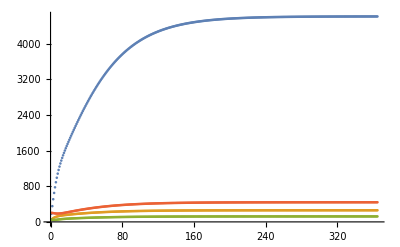

```mathematica
{bs,temperature}={25,25};
{BS,me,egn,ef,ma,α0}={bs,.01,63,.83,.09,1.5};
{a0,α,ml,mp}={.75, αf[α0, bs],mlf[temperature+273.15],mpf[temperature+273.15]};
schoolfield=CalculateSchoolfieldSet[temperature,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},250,365]//ListPlot
```

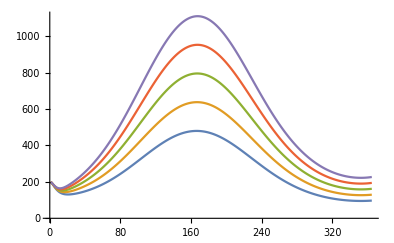

```mathematica
(*ERROR!!! HAS TO BE RUN TWICE TO WORK FOR WHATEVER REASON*)
Table[
{bs,temperature}={i,20};
{BS,me,egn,ef,ma,ml,mp,α0}={bs,.01,63,.83,.09,mlf[temperature+273.15],mpf[temperature+273.15],1.5};
{a0,α}={.75, αf[α0, bs]};
schoolfield=CalculateSchoolfieldSet[24.542238030594344-2.865555479949232*Cos[0.8337037265403161+0.017202423838958484*t],{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},250,365][[4]]
,{i,15,35,5}]//ListPlot[#,Joined->True]&
```

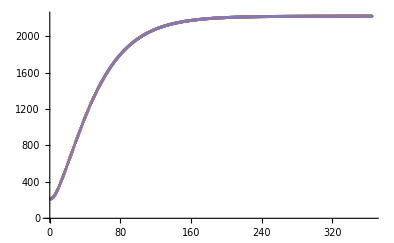

```mathematica
(*THESE TWO PLOTS SHOULD BE THE SAME*)
Table[CalculateAndRunStochasticModelFinal[30,{i,me,egn,ma,ml,mp,α,ef,a0},250,365],{i,15,35,5}][[All,4]]//ListPlot
```

## Comparison Functions

```mathematica
HeadComparisonBetweenABMAndMathematical[ABMPath_,sampleRate_]:=Module[{temperature,bs,abmData,meanABMValues,days,initPop,time,me,egn,ef,ma,ml,mp,α0,a0,α,schoolfield,soln,stochasticPopDynamics},
{temperature,bs}={ToExpression[StringTake[ABMPath,-2]],ToExpression[StringTake[ABMPath,{-4,-3}]]};
abmData=ReturnData[ParentDirectory[]<>ABMPath,{"EggsPopulation","LarvaPopulation","PupaPopulation","AdultPopulation"},sampleRate];
{meanABMValues,time,initPop }={(Transpose/@abmData[[2,1]])//Transpose,abmData[[2,1,1]]//Length,250};
(**)
{me,egn,ef,ma,ml,mp,α0}={.01,63,.83,.09,mlf[temperature+273.15],mpf[temperature+273.15],1.5};
{a0,α}={.75, αf[α0, bs]};
schoolfield=CalculateSchoolfieldSet[temperature,{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{bs,me,egn,ma,ml,mp,α,ef,a0},initPop,time];
{stochasticPopDynamics,meanABMValues}
]
CompareABMAndMathematicalFactorialRatio[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]]},
Table[Mean/@(((#[[1]]-#[[2]])/(#[[2]]))&/@({meanABMValues[[i]],stochasticPopDynamics}//Transpose//N)),{i,1,meanABMValues//Length}]//Transpose]
CompareABMAndMathematicalFactorialDifference[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]]},Table[Mean/@((#[[1]]-#[[2]])&/@({meanABMValues[[i]],stochasticPopDynamics}//Transpose//N)),{i,1,meanABMValues//Length}]//Transpose]

CompareABMAndMathematicalFactorialDifferenceSS[headComparison_]:=Module[{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]],steadySim,steadyMath,out},
Clear[a,x];
steadySim=Table[(NonlinearModelFit[#[[Floor[.5*meanABMValues[[1]]//Length];;All]],a,{a},x]//Normal)&/@i,{i,meanABMValues}];
steadyMath=Last/@stochasticPopDynamics;
out=(#-steadyMath)&/@steadySim;
out//Transpose
]

CompareABMAndMathematicalFactorialRatioSS[headComparison_]:=Module[
{stochasticPopDynamics=headComparison[[1]],meanABMValues=headComparison[[2]],steadySim,steadyMath,out},
Clear[a,x];
steadySim=Table[(NonlinearModelFit[#[[Floor[.75*meanABMValues[[1]]//Length];;All]],a,{a},x]//Normal)&/@i,{i,meanABMValues}];
steadyMath=Last/@stochasticPopDynamics;
out=(#-steadyMath)/steadyMath&/@steadySim;
out//Transpose
]
```

## Fit Density Dependent Model

```mathematica
FitNonLinearModel[dataRaw_,steps_]:=Module[{regressions,dataT,model,results,kValues,inputData,k,pfun,fit,functions,rValues},
(*Unsafe for a, k, r, t, x*)
(*Regression of k*)
Clear[a,x];
regressions=Table[
dataT=dataRaw[[2,2,i]][[Floor[(dataRaw[[2,2,1]]//Length)*.25];;All]];
model=NonlinearModelFit[dataT,a,{a},x]//Normal;
{model,Show[{ListPlot[dataT],Plot[model,{x,0,steps}]}]}
,{i,1,4}];
kValues=regressions[[All,1]];
(*Regression of r*)
Clear[τ,r,k];
τ=0;
results=Table[
inputData=dataRaw[[2,2,i]];
Clear[r,k];
k=kValues[[i]];
pfun=ParametricNDSolveValue[{
n'[t]==r*n[t]*((k-n[t-τ])/k),
n[0]==inputData[[1]]
},n,{t,0,2*steps},{r}];
fit=FindFit[inputData,pfun[r][t],{{r,1}},t]//Quiet;
{pfun,fit}
,{i,1,4}];
rValues=results[[All,2,1,2]];
(*Returning values*)
functions=(#[[1]][r][t]/.#[[2]])&/@results;
{kValues,rValues,functions}//Transpose
]
FitDensityDependentModel[meanABM_]:=Module[{k,pfun,fit,r,function},
Clear[a,x,k,r,t];
k=NonlinearModelFit[meanABM[[Floor[.25*(meanABM//Length)];;All]],a,{a},x]//Normal;
pfun=ParametricNDSolveValue[{
n'[t]==r*n[t]*((k-n[t])/k),
n[0]==meanABM[[1]]
},n,{t,0,2*(meanABM//Length)},{r}];
fit=(FindFit[meanABM,pfun[r][t],{{r,.05}},t]//Quiet);
r=fit[[1,2]];
function=(pfun[r][t]/.fit);
{function,{k,r}}
]
CompareABMAndMathematicalPlots[headTest_,lifeStage_]:=Module[{stochastic,meanABM,model},
stochastic=headTest[[1,lifeStage]];
meanABM=Mean/@(headTest[[2,All,lifeStage]]//Transpose)//N;
model=FitDensityDependentModel[meanABM];
Show[{
Plot[model[[1]],{t,0,meanABM//Length},PlotRange->{0,1.25*Max[{(stochastic//Last),(meanABM//Last)}]},PlotLegends->{"ABM Fit"},PlotLabel->{"r="<>ToString[model[[2,2]]],"k="<>ToString[model[[2,1]]]}],
ListPlot[{stochastic,meanABM},PlotStyle->{Red,Green},Joined->True,PlotLegends->{"Mathematical","ABM Data"}]
}]
]
```

## Other

```mathematica
GenerateTaguchiMatrix[comparisonsDifference_,paths_]:=Module[{bsTVct,means,sds,taguchiDifference,taguchiDifferenceFull},
bsTVct={StringTake[#,{-4,-3}],StringTake[#,-2]}&/@paths;
(*Difference*)
{means,sds}={{Prepend[Mean/@comparisonsDifference,"Mean"]}//Transpose,{Prepend[StandardDeviation/@comparisonsDifference,"SD"]}//Transpose};
taguchiDifference=Prepend[Flatten/@({bsTVct,comparisonsDifference}//Transpose),{"BreedingSites","Temperature",Range[comparisonsDifference//Transpose//Length]}//Flatten];
taguchiDifferenceFull=Append[Append[taguchiDifference//Transpose,means//Flatten],sds//Flatten]//Transpose
]
```

## Experiment 1 : Validation

## Copy Files (only needed the first time the experiment is run)

```mathematica
{sampleRate,secondsPerTick,lifeStage}={288,5*60,4};
rootPath="/GeneratedData/ValidationSweepsNew/";
files=FileNames["*.xml",ParentDirectory[]<>rootPath];
fileNames=Last[#]&/@(FileNameSplit[#]&/@files);
rawData=ParallelMap[Import[#]&,files];
headers=ParallelMap[GetExperimentParameters[#]&,rawData];
params=headers[[All,2;;3]];
paramsBS=Switch[#,"1",10,"2",15,"3",20,"4",25,"5",30,"6",35]&/@params[[All,1,3]];
paramsT=ToExpression/@params[[All,2,3]];
paramsPairs=(ToString[#[[1]]]<>ToString[#[[2]]])&/@Transpose[{paramsBS,paramsT}];
directories=(CreateDirectory[ParentDirectory[]<>"/GeneratedData/ValidationSweeps/"<>#]&/@DeleteDuplicates[paramsPairs])//Quiet
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
directories=(ParentDirectory[]<>"/GeneratedData/ValidationSweeps/"<>#)&/@paramsPairs;
CopyFile[#[[1]],#[[3]]<>"/"<>#[[2]]]&/@({files,fileNames,directories}//Transpose)//Quiet;
```

## Load Data

```mathematica
{sampleRate,secondsPerTick,lifeStage,levelsT,levelsBS}={288,5*60,4,5,6};
paths="/GeneratedData/ValidationSweeps/"<>#&/@{
"1015","1020","1025","1030","1035",
"1515","1520","1525","1530","1535",
"2015","2020","2025","2030","2035",
"2515","2520","2525","2530","2535",
"3015","3020","3025","3030","3035",
"3515","3520","3525","3530","3535"
}
```

{/GeneratedData/ValidationSweeps/1015,/GeneratedData/ValidationSweeps/1020,/GeneratedData/ValidationSweeps/1025,/GeneratedData/ValidationSweeps/1030,/GeneratedData/ValidationSweeps/1035,/GeneratedData/ValidationSweeps/1515,/GeneratedData/ValidationSweeps/1520,/GeneratedData/ValidationSweeps/1525,/GeneratedData/ValidationSweeps/1530,/GeneratedData/ValidationSweeps/1535,/GeneratedData/ValidationSweeps/2015,/GeneratedData/ValidationSweeps/2020,/GeneratedData/ValidationSweeps/2025,/GeneratedData/ValidationSweeps/2030,/GeneratedData/ValidationSweeps/2035,/GeneratedData/ValidationSweeps/2515,/GeneratedData/ValidationSweeps/2520,/GeneratedData/ValidationSweeps/2525,/GeneratedData/ValidationSweeps/2530,/GeneratedData/ValidationSweeps/2535,/GeneratedData/ValidationSweeps/3015,/GeneratedData/ValidationSweeps/3020,/GeneratedData/ValidationSweeps/3025,/GeneratedData/ValidationSweeps/3030,/GeneratedData/ValidationSweeps/3035,/GeneratedData/ValidationSweeps/3515,/GeneratedData/ValidationSweeps/3520,/GeneratedData/ValidationSweeps/3525,/GeneratedData/ValidationSweeps/3530,/GeneratedData/ValidationSweeps/3535}

```mathematica
head=HeadComparisonBetweenABMAndMathematical[#,sampleRate]&/@paths;
body={comparisonsDifference,comparisonsRatio,comparisonsDifferenceSS,comparisonsRatioSS}={
(CompareABMAndMathematicalFactorialDifference[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialRatio[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialDifferenceSS[#]&/@head)[[All,lifeStage]],
(CompareABMAndMathematicalFactorialRatioSS[#]&/@head)[[All,lifeStage]]
};
```

## Taguchi

```mathematica
taguchis=GenerateTaguchiMatrix[#,paths]&/@body;
(*Export["DOE/Taguchi/"<>#[[2]],#[[1]]]&/@({taguchis,{"taguchiDifference.csv","taguchiRatio.csv","taguchiDifferenceSS.csv","taguchiRatioSS.csv"}}//Transpose);*)
TableForm[#]&/@taguchis
```

{BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | Mean | SD
10 | 15 | -1.55086 | -4.42296 | -1.21947 | -1.96947 | -3.40552 | -1.19621 | -4.27179 | -3.33575 | -3.85319 | -5.49272 | -3.53924 | -3.45784 | -4.93458 | -1.21365 | -2.64389 | -0.922957 | -1.96365 | -4.78924 | -4.05086 | -5.10319 | -3.16685 | 1.47912
10 | 20 | -5.25097 | -3.65795 | -9.43121 | -4.94283 | -8.33818 | -4.71028 | -1.33237 | -3.28004 | -5.67539 | -3.92539 | -0.634694 | -9.00679 | -9.32074 | -6.19865 | -5.90795 | -5.49516 | -4.56493 | -10.2393 | -6.22772 | -11.4254 | -5.9783 | 2.8867
10 | 25 | 3.41189 | 6.09794 | 22.4817 | 23.6677 | 24.6038 | 28.4642 | 23.1503 | 24.9235 | 22.1096 | 6.4991 | -1.9602 | 15.7258 | 29.6212 | 20.5921 | 27.1444 | 16.4061 | 19.9584 | 12.6677 | 12.0282 | -3.4602 | 16.7067 | 10.0261
10 | 30 | -83.872 | -96.5697 | -148.198 | -120.465 | -137.093 | -91.1743 | -116.134 | -113.849 | -86.4767 | -90.7674 | -110.436 | -74.3197 | -88.7383 | -86.6743 | -91.4476 | -112.302 | -107.506 | -104.017 | -120.139 | -109.355 | -104.477 | 18.7079
10 | 35 | -341.286 | -325.054 | -346.269 | -322.6 | -343.123 | -327.054 | -346.862 | -327.461 | -328.187 | -334.693 | -344.501 | -330.455 | -336.635 | -325.484 | -329.653 | -312.868 | -325.786 | -316.676 | -324.118 | -324.17 | -330.647 | 9.71254
15 | 15 | 0.64871 | -4.36873 | -1.50245 | -2.86292 | -4.42106 | -3.21757 | -3.46757 | -1.52571 | -3.42687 | -1.8978 | -1.64199 | -3.26408 | -2.85129 | -2.66524 | -3.70594 | -3.99083 | -1.38036 | -5.35129 | -1.89199 | -3.49083 | -2.81379 | 1.37188
15 | 20 | 27.7933 | 22.6886 | 22.3572 | 26.206 | 23.8107 | 30.5316 | 27.02 | 24.2816 | 25.8746 | 24.2235 | 26.8863 | 22.863 | 26.0549 | 25.9153 | 27.677 | 26.6479 | 23.7467 | 22.8572 | 25.7642 | 22.363 | 25.2781 | 2.19654
15 | 25 | 126.586 | 132.836 | 122.034 | 126.418 | 125.15 | 130.052 | 132.476 | 137.47 | 127.528 | 122.406 | 122.709 | 128.04 | 132.488 | 130.546 | 123.116 | 134.47 | 126.441 | 128.953 | 120.836 | 130.831 | 128.069 | 4.58807
15 | 30 | -28.5531 | -46.1345 | -10.1577 | -77.5647 | -40.7449 | -38.5647 | -28.5124 | -33.71 | -36.5473 | -23.9193 | -47.0007 | -33.5356 | -54.8263 | -32.7333 | -48.3786 | -39.3961 | -50.3961 | -25.3786 | -31.8961 | -41.5124 | -38.4731 | 13.94
15 | 35 | -425.253 | -432.881 | -446.026 | -432.439 | -446.329 | -425.416 | -437.922 | -438.625 | -442.834 | -434.323 | -430.8 | -439.927 | -424.114 | -438.154 | -438.16 | -440.55 | -437.323 | -430.061 | -435.114 | -426.317 | -435.128 | 6.67823
20 | 15 | -2.72588 | -1.96426 | -4.50495 | -3.57472 | -2.58054 | -4.60961 | -4.97007 | -4.0224 | -4.69681 | -4.43519 | -4.2724 | -3.33635 | -3.7724 | -1.87123 | -4.24914 | -2.49333 | -3.75495 | -4.4003 | -4.21426 | -3.47588 | -3.69623 | 0.927137
20 | 20 | 72.1328 | 70.0747 | 67.0456 | 69.9293 | 68.0107 | 69.6735 | 65.4817 | 76.9119 | 70.4235 | 62.9235 | 71.127 | 71.284 | 66.2782 | 65.9875 | 66.3363 | 75.7317 | 68.8247 | 69.8596 | 69.4817 | 74.2898 | 69.5904 | 3.49179
20 | 25 | 262.934 | 266.928 | 256.76 | 263.254 | 262.725 | 259.254 | 261.457 | 276.969 | 260.626 | 268.946 | 261.056 | 279.608 | 251.655 | 261.521 | 249.306 | 265.777 | 267.986 | 273.969 | 280.271 | 270.533 | 265.077 | 8.35641
20 | 30 | 20.1806 | 23.5643 | 33.134 | 22.7213 | 37.1689 | 35.8957 | 23.2445 | 14.9364 | 30.6108 | 31.6515 | 18.9306 | 39.7445 | 36.0468 | 24.9654 | 36.2096 | 15.9306 | 25.8899 | 4.59916 | 28.8143 | 28.7794 | 26.6509 | 8.94138
20 | 35 | -543.625 | -548.038 | -538.869 | -532.654 | -535.224 | -553.654 | -534.107 | -518.916 | -539.887 | -548.189 | -536.357 | -541.41 | -530.776 | -533.491 | -529.119 | -537.328 | -535.997 | -534.671 | -557.52 | -543.956 | -538.689 | 8.85404
25 | 15 | -7.38988 | -1.80848 | -4.13988 | -4.14569 | -4.4422 | -2.70383 | -2.37825 | -1.7329 | -3.7329 | -4.64569 | -3.30267 | -3.25615 | -3.1515 | -4.71546 | -6.35499 | -2.82011 | -4.11662 | -0.180573 | -1.94801 | -3.26778 | -3.51168 | 1.62638
25 | 20 | 115.683 | 114.846 | 118.991 | 122.503 | 120.584 | 120.253 | 122.607 | 122.253 | 120.003 | 116.45 | 118.195 | 114.549 | 119.555 | 120.509 | 122.945 | 117.619 | 120.869 | 120.846 | 121.142 | 122.98 | 119.669 | 2.66152
25 | 25 | 413.675 | 417.478 | 424.896 | 417.344 | 425.286 | 425.013 | 414.303 | 418.327 | 402.268 | 429.21 | 406.234 | 414.612 | 417.536 | 413.112 | 414.914 | 420.018 | 419.78 | 417.449 | 412.1 | 421.414 | 417.248 | 6.41722
25 | 30 | 112.976 | 105.942 | 77.145 | 93.302 | 95.4125 | 106.988 | 98.209 | 112.436 | 97.8718 | 93.9125 | 88.7206 | 96.8601 | 103.255 | 110.86 | 97.2613 | 107. | 87.0113 | 112.215 | 110.535 | 111.918 | 100.992 | 10.0358
25 | 35 | -633.777 | -640.016 | -655.074 | -645.789 | -656.074 | -634.394 | -643.318 | -634.149 | -636.789 | -634.492 | -638.132 | -632.708 | -653.789 | -632.661 | -641.789 | -621.556 | -641.719 | -624.469 | -639.138 | -642.632 | -639.123 | 9.04849
30 | 15 | -4.4238 | -4.24357 | -6.22613 | -3.20287 | -3.78427 | -2.41217 | -4.73775 | -5.03427 | -6.26101 | -7.48775 | -6.05752 | -2.9645 | -4.90054 | -3.72031 | -4.83659 | -3.44124 | -4.94124 | -6.74357 | -3.42961 | -6.41799 | -4.76334 | 1.40351
30 | 20 | 175.024 | 167.64 | 173.658 | 167.297 | 171.733 | 182.728 | 174.739 | 171.978 | 168.175 | 172.111 | 176.414 | 162.902 | 170.512 | 170.123 | 170.553 | 170.088 | 170.14 | 164.635 | 177.39 | 177.71 | 171.778 | 4.71521
30 | 25 | 574.94 | 588.486 | 574.812 | 586.626 | 565.696 | 584.556 | 572.887 | 570.236 | 580.015 | 576.172 | 573.951 | 566.504 | 592.533 | 577.975 | 570.539 | 567.434 | 593.027 | 564.172 | 565.696 | 577.556 | 576.191 | 8.95103
30 | 30 | 189.865 | 150.865 | 178.667 | 164.998 | 186.597 | 168.76 | 181.871 | 180.795 | 175.091 | 176.65 | 181.376 | 184.202 | 184.789 | 174.196 | 193.487 | 171.452 | 193.841 | 171.318 | 179.545 | 151.795 | 177.008 | 11.6914
30 | 35 | -739.467 | -735.74 | -750.368 | -725.397 | -750.897 | -735.775 | -722.909 | -711.281 | -733.333 | -741.38 | -735.485 | -741.322 | -744.171 | -727.961 | -721.002 | -750.304 | -737.996 | -728.205 | -733.072 | -738.269 | -735.217 | 10.3291
35 | 15 | -5.43598 | -5.8604 | -5.05807 | -6.11621 | -4.26156 | -5.72086 | -5.59296 | -5.89528 | -5.95342 | -1.6104 | -5.44179 | -3.16854 | -5.05226 | -2.19179 | -7.10458 | -5.90691 | -6.3604 | -6.88947 | -7.22086 | -1.50575 | -5.11737 | 1.71331
35 | 20 | 219.009 | 223.823 | 226.858 | 221.602 | 219.312 | 222.957 | 216.684 | 219.172 | 219.015 | 225.806 | 225.602 | 208.649 | 218.015 | 228.294 | 223.306 | 228.079 | 207.591 | 229.957 | 222.032 | 227.858 | 221.681 | 6.0369
35 | 25 | 751.547 | 736.221 | 747.466 | 756.751 | 750.861 | 767.163 | 761.483 | 752.146 | 745.361 | 740.309 | 728.001 | 742.727 | 742.094 | 761.559 | 746.751 | 748.274 | 759.46 | 773.041 | 752.431 | 735.576 | 749.961 | 11.174
35 | 30 | 251.143 | 232.119 | 230.55 | 262.096 | 284.451 | 247.061 | 254.968 | 272.201 | 243.189 | 227.922 | 267.677 | 236.805 | 270.619 | 262.852 | 242.771 | 270.294 | 224.677 | 263.044 | 264.515 | 209.311 | 250.913 | 19.5939
35 | 35 | -838.632 | -845.737 | -845.597 | -854.021 | -821.487 | -843.021 | -846.248 | -818.818 | -817.911 | -839.754 | -854.202 | -842.01 | -831.864 | -814.864 | -838.958 | -826.678 | -824.521 | -839.068 | -833.975 | -815.981 | -834.667 | 12.4763,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | Mean | SD
10 | 15 | -0.664575 | -0.733786 | -0.670759 | -0.719873 | -0.724862 | -0.708223 | -0.720951 | -0.738669 | -0.751353 | -0.75846 | -0.72909 | -0.708894 | -0.758573 | -0.687729 | -0.706109 | -0.701654 | -0.675971 | -0.759397 | -0.728759 | -0.77124 | -0.720946 | 0.0308652
10 | 20 | -0.176522 | -0.140319 | -0.256691 | -0.120954 | -0.220997 | -0.140043 | -0.0580777 | -0.126579 | -0.169036 | -0.131413 | -0.0464381 | -0.2298 | -0.25184 | -0.186186 | -0.188586 | -0.123996 | -0.133173 | -0.24881 | -0.159641 | -0.286644 | -0.169787 | 0.0648029
10 | 25 | 0.0216149 | 0.03557 | 0.134415 | 0.140666 | 0.145201 | 0.171463 | 0.138174 | 0.147234 | 0.131569 | 0.0397561 | -0.0104153 | 0.0948619 | 0.177746 | 0.122952 | 0.161784 | 0.0973972 | 0.118466 | 0.0760285 | 0.0733776 | -0.0212625 | 0.0998299 | 0.0596214
10 | 30 | -0.140017 | -0.159257 | -0.260231 | -0.201863 | -0.236356 | -0.154092 | -0.206296 | -0.199057 | -0.142502 | -0.15722 | -0.194813 | -0.117585 | -0.141605 | -0.144287 | -0.151007 | -0.186907 | -0.190364 | -0.18 | -0.205555 | -0.182702 | -0.177586 | 0.0356702
10 | 35 | -0.49569 | -0.470323 | -0.501479 | -0.47139 | -0.500036 | -0.471733 | -0.504301 | -0.480155 | -0.472676 | -0.486331 | -0.499212 | -0.479459 | -0.487377 | -0.468982 | -0.479537 | -0.453741 | -0.468639 | -0.460519 | -0.469615 | -0.470732 | -0.479596 | 0.014443
15 | 15 | -0.584059 | -0.684729 | -0.582965 | -0.641366 | -0.719445 | -0.667354 | -0.663898 | -0.63372 | -0.68491 | -0.655391 | -0.64654 | -0.670065 | -0.650944 | -0.654375 | -0.69741 | -0.717028 | -0.669461 | -0.729238 | -0.664086 | -0.638253 | -0.662762 | 0.0382952
15 | 20 | 0.58901 | 0.49411 | 0.487336 | 0.546723 | 0.512415 | 0.661483 | 0.594875 | 0.534346 | 0.565674 | 0.530954 | 0.57243 | 0.474064 | 0.549046 | 0.560046 | 0.580163 | 0.556805 | 0.479225 | 0.502775 | 0.543423 | 0.510989 | 0.542295 | 0.0460181
15 | 25 | 0.53691 | 0.561818 | 0.516648 | 0.540222 | 0.530579 | 0.553826 | 0.56128 | 0.586504 | 0.542156 | 0.517406 | 0.521616 | 0.542965 | 0.568834 | 0.557088 | 0.522164 | 0.56858 | 0.534839 | 0.542146 | 0.5133 | 0.550656 | 0.543477 | 0.020082
15 | 30 | 0.0113057 | -0.0197895 | 0.0223928 | -0.0745197 | -0.0184226 | -0.0157036 | 0.00710792 | -0.00643696 | -0.0148405 | -0.00071379 | -0.0252673 | -0.00406535 | -0.043227 | -0.00151231 | -0.0188753 | -0.00799724 | -0.0359405 | 0.00657087 | -0.00106314 | -0.0159176 | -0.0128458 | 0.0214083
15 | 35 | -0.408499 | -0.409668 | -0.429871 | -0.416108 | -0.42648 | -0.406215 | -0.419606 | -0.421238 | -0.425741 | -0.418839 | -0.409888 | -0.42709 | -0.402356 | -0.425173 | -0.419598 | -0.423226 | -0.421381 | -0.409096 | -0.413025 | -0.402301 | -0.41677 | 0.00856814
20 | 15 | -0.550841 | -0.621664 | -0.670916 | -0.612193 | -0.650315 | -0.647782 | -0.652048 | -0.630987 | -0.646041 | -0.66024 | -0.661338 | -0.588353 | -0.603146 | -0.588843 | -0.632781 | -0.615295 | -0.677636 | -0.662332 | -0.649547 | -0.627362 | -0.632483 | 0.0321596
20 | 20 | 1.23733 | 1.17475 | 1.14269 | 1.2014 | 1.16873 | 1.19698 | 1.11069 | 1.30953 | 1.2023 | 1.09824 | 1.20591 | 1.21595 | 1.12807 | 1.13527 | 1.1541 | 1.28568 | 1.17647 | 1.20869 | 1.16742 | 1.27473 | 1.18975 | 0.05662
20 | 25 | 0.881787 | 0.880316 | 0.859425 | 0.875756 | 0.872095 | 0.856839 | 0.875548 | 0.924867 | 0.863387 | 0.905013 | 0.8702 | 0.927032 | 0.834914 | 0.872425 | 0.838535 | 0.881993 | 0.890249 | 0.907418 | 0.927631 | 0.901 | 0.882321 | 0.0267133
20 | 30 | 0.075713 | 0.0866771 | 0.0984975 | 0.0856348 | 0.0907726 | 0.097993 | 0.0752325 | 0.061461 | 0.0979786 | 0.090429 | 0.0661962 | 0.0913067 | 0.0965154 | 0.0781779 | 0.0994628 | 0.0670809 | 0.0875836 | 0.0641887 | 0.0967349 | 0.0802968 | 0.0843967 | 0.0125997
20 | 35 | -0.383043 | -0.387573 | -0.381107 | -0.366009 | -0.372301 | -0.390539 | -0.381475 | -0.360702 | -0.375612 | -0.393149 | -0.380887 | -0.380573 | -0.372019 | -0.373122 | -0.375874 | -0.375348 | -0.377543 | -0.378292 | -0.388832 | -0.38447 | -0.378923 | 0.00806293
25 | 15 | -0.660042 | -0.529953 | -0.536471 | -0.581899 | -0.580516 | -0.560361 | -0.589628 | -0.511189 | -0.537898 | -0.619079 | -0.552389 | -0.598659 | -0.528747 | -0.560407 | -0.62606 | -0.58161 | -0.586846 | -0.440421 | -0.542569 | -0.560715 | -0.564273 | 0.0469736
25 | 20 | 1.6547 | 1.65244 | 1.703 | 1.75752 | 1.72616 | 1.73132 | 1.7601 | 1.75659 | 1.73736 | 1.67682 | 1.70006 | 1.6493 | 1.72151 | 1.73576 | 1.76854 | 1.68861 | 1.72742 | 1.73695 | 1.73233 | 1.7621 | 1.71893 | 0.0377208
25 | 25 | 1.1394 | 1.15182 | 1.18406 | 1.12784 | 1.16977 | 1.16503 | 1.14264 | 1.14736 | 1.10373 | 1.1766 | 1.11343 | 1.14027 | 1.14783 | 1.1483 | 1.1425 | 1.14848 | 1.14817 | 1.15419 | 1.13589 | 1.15715 | 1.14722 | 0.0190678
25 | 30 | 0.170625 | 0.170017 | 0.120761 | 0.150204 | 0.147868 | 0.168745 | 0.161628 | 0.168454 | 0.158038 | 0.146785 | 0.145747 | 0.153777 | 0.156173 | 0.161597 | 0.150351 | 0.166682 | 0.135494 | 0.159387 | 0.157603 | 0.162417 | 0.155618 | 0.0124612
25 | 35 | -0.349394 | -0.347292 | -0.364002 | -0.350971 | -0.3612 | -0.346596 | -0.347862 | -0.346551 | -0.344474 | -0.347222 | -0.347654 | -0.342066 | -0.370293 | -0.344232 | -0.352071 | -0.336806 | -0.350833 | -0.3393 | -0.350814 | -0.353032 | -0.349633 | 0.00798255
30 | 15 | -0.584968 | -0.535687 | -0.575005 | -0.508884 | -0.560062 | -0.5337 | -0.552328 | -0.570942 | -0.605647 | -0.603477 | -0.57524 | -0.497318 | -0.572248 | -0.541202 | -0.522399 | -0.50287 | -0.590261 | -0.578859 | -0.561243 | -0.591379 | -0.558186 | 0.0327917
30 | 20 | 2.15225 | 2.08056 | 2.15379 | 2.07719 | 2.13045 | 2.25973 | 2.16082 | 2.13199 | 2.07953 | 2.12895 | 2.193 | 2.03152 | 2.11483 | 2.10802 | 2.11424 | 2.10328 | 2.1029 | 2.04236 | 2.19572 | 2.20228 | 2.12817 | 0.0561305
30 | 25 | 1.33277 | 1.37971 | 1.3413 | 1.36976 | 1.32246 | 1.37448 | 1.3385 | 1.33345 | 1.365 | 1.33681 | 1.34919 | 1.31599 | 1.39024 | 1.35008 | 1.32817 | 1.32568 | 1.38695 | 1.32104 | 1.31294 | 1.37587 | 1.34752 | 0.024895
30 | 30 | 0.222738 | 0.189334 | 0.197376 | 0.202067 | 0.213634 | 0.2103 | 0.215351 | 0.21002 | 0.197555 | 0.201861 | 0.226687 | 0.218485 | 0.208959 | 0.205743 | 0.226057 | 0.204195 | 0.231488 | 0.202964 | 0.210145 | 0.177162 | 0.208606 | 0.0131521
30 | 35 | -0.325217 | -0.32624 | -0.337968 | -0.319487 | -0.336962 | -0.321221 | -0.325857 | -0.303171 | -0.334787 | -0.326994 | -0.323629 | -0.322225 | -0.336284 | -0.320314 | -0.309017 | -0.335899 | -0.321619 | -0.322714 | -0.318539 | -0.338987 | -0.325357 | 0.00951212
35 | 15 | -0.541774 | -0.564491 | -0.562283 | -0.56624 | -0.523913 | -0.578937 | -0.545905 | -0.59659 | -0.553178 | -0.48961 | -0.590933 | -0.521265 | -0.567817 | -0.462989 | -0.591238 | -0.549847 | -0.56393 | -0.567056 | -0.603462 | -0.460271 | -0.550086 | 0.0407423
35 | 20 | 2.39273 | 2.44834 | 2.48092 | 2.42806 | 2.40212 | 2.43623 | 2.37034 | 2.39489 | 2.39989 | 2.47213 | 2.46646 | 2.29386 | 2.38681 | 2.49542 | 2.44333 | 2.4898 | 2.27714 | 2.52033 | 2.43105 | 2.48933 | 2.42596 | 0.063699
35 | 25 | 1.53687 | 1.49658 | 1.51183 | 1.5335 | 1.53985 | 1.56937 | 1.53678 | 1.53219 | 1.52705 | 1.50611 | 1.48013 | 1.52564 | 1.50291 | 1.5579 | 1.5008 | 1.52636 | 1.55297 | 1.58583 | 1.54141 | 1.47454 | 1.52693 | 0.0284038
35 | 30 | 0.253361 | 0.228874 | 0.21885 | 0.246389 | 0.270592 | 0.241322 | 0.246305 | 0.258813 | 0.243427 | 0.231247 | 0.249002 | 0.234991 | 0.256925 | 0.266576 | 0.23238 | 0.2558 | 0.208948 | 0.257702 | 0.258105 | 0.217074 | 0.243834 | 0.0169421
35 | 35 | -0.316113 | -0.321449 | -0.321912 | -0.31636 | -0.311588 | -0.326881 | -0.323852 | -0.302663 | -0.301754 | -0.315402 | -0.311848 | -0.312181 | -0.31098 | -0.289684 | -0.317058 | -0.315917 | -0.296329 | -0.316831 | -0.306109 | -0.302939 | -0.311893 | 0.00950018,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | Mean | SD
10 | 15 | 14.7166 | 11.9473 | 14.8763 | 13.8468 | 12.9178 | 14.687 | 11.9178 | 12.8113 | 12.0302 | 10.7817 | 12.8172 | 12.7876 | 11.4799 | 14.9296 | 13.5095 | 14.9414 | 14.2195 | 11.7343 | 12.3497 | 11.0065 | 13.0154 | 1.37336
10 | 20 | 13.3934 | 14.7839 | 9.16259 | 13.8608 | 10.1803 | 13.8726 | 17.494 | 15.3815 | 12.849 | 14.5531 | 17.7661 | 9.97324 | 9.35786 | 12.1922 | 12.4584 | 13.3046 | 14.0502 | 8.81939 | 12.3697 | 7.28685 | 12.6555 | 2.82138
10 | 25 | -3.50484 | -0.723774 | 15.8265 | 16.7141 | 17.9745 | 21.9153 | 16.365 | 18.2881 | 15.7318 | -0.39833 | -8.96046 | 8.89753 | 22.9389 | 13.8443 | 20.7318 | 9.7851 | 13.3768 | 5.94487 | 5.27031 | -10.564 | 9.97268 | 10.1654
10 | 30 | -198.475 | -211.445 | -263.522 | -235.688 | -252.505 | -206.043 | -231.215 | -229.055 | -200.866 | -205.445 | -225.126 | -188.67 | -203.505 | -201.392 | -206.037 | -227.546 | -222.369 | -218.943 | -235.38 | -224.587 | -219.391 | 18.986
10 | 35 | -478.427 | -461.794 | -483.581 | -459.61 | -480.119 | -464.102 | -483.93 | -464.054 | -465.214 | -471.421 | -481.918 | -467.451 | -473.794 | -462.705 | -466.699 | -449.64 | -462.522 | -453.285 | -461.125 | -460.859 | -467.613 | 9.86077
15 | 15 | 17.5074 | 12.1406 | 15.2944 | 13.7205 | 12.3062 | 13.5903 | 13.0873 | 15.2648 | 13.2234 | 14.6494 | 14.7974 | 13.5903 | 13.8565 | 14.0045 | 12.9867 | 12.5784 | 14.9808 | 11.3062 | 14.5252 | 13.3477 | 13.8379 | 1.38171
15 | 20 | 45.6333 | 40.58 | 39.8463 | 43.8996 | 41.4913 | 48.8286 | 45.2428 | 42.1067 | 43.6984 | 42.0948 | 44.8641 | 40.6037 | 43.9114 | 43.8463 | 45.6274 | 44.3552 | 41.4558 | 41.0061 | 43.657 | 40.509 | 43.1629 | 2.28149
15 | 25 | 100.486 | 106.693 | 95.4799 | 100.22 | 98.7698 | 103.723 | 106.456 | 111.421 | 101.379 | 96.255 | 96.2314 | 101.563 | 106.296 | 104.462 | 96.8527 | 108.243 | 100.024 | 102.687 | 94.3911 | 104.634 | 101.813 | 4.68688
15 | 30 | -228.7 | -245.884 | -209.529 | -278.073 | -240.505 | -238.493 | -228.304 | -233.629 | -236.345 | -223.475 | -246.771 | -233.298 | -254.588 | -232.783 | -248.671 | -239.256 | -250.351 | -225.185 | -231.529 | -241.505 | -238.344 | 14.1121
15 | 35 | -660.404 | -668.309 | -681.173 | -667.599 | -681.889 | -660.57 | -673.226 | -673.706 | -678.007 | -669.546 | -666.061 | -674.948 | -659.209 | -673.457 | -673.617 | -676.061 | -672.57 | -665.244 | -670.499 | -661.741 | -670.392 | 6.71655
20 | 15 | 14.4549 | 15.0998 | 12.3306 | 13.4963 | 14.1412 | 12.3543 | 12.1412 | 12.9519 | 12.2418 | 12.591 | 12.4549 | 13.7507 | 13.2596 | 15.0998 | 12.8868 | 14.3602 | 12.9874 | 12.5377 | 12.6797 | 13.6087 | 13.2714 | 0.941317
20 | 20 | 89.0581 | 86.6144 | 83.9339 | 87.0108 | 84.7386 | 86.3895 | 82.0759 | 93.9931 | 87.3008 | 80.0167 | 87.8688 | 88.2771 | 83.0404 | 83.0108 | 83.283 | 92.6558 | 85.709 | 86.7919 | 86.0818 | 91.1883 | 86.4519 | 3.51798
20 | 25 | 215.811 | 220.137 | 209.628 | 216.362 | 215.723 | 212.427 | 214.586 | 230.545 | 213.675 | 222.095 | 213.882 | 232.799 | 204.421 | 214.663 | 201.681 | 218.965 | 221.113 | 227.444 | 233.705 | 223.616 | 218.164 | 8.57832
20 | 30 | -268.381 | -264.742 | -254.961 | -265.878 | -250.931 | -252.274 | -265.298 | -273.458 | -257.973 | -256.659 | -269.416 | -248.434 | -252.245 | -263.594 | -252.109 | -272.683 | -262.464 | -283.913 | -259.7 | -259.274 | -261.719 | 9.05273
20 | 35 | -880.898 | -885.46 | -876.14 | -870.022 | -872.761 | -891.442 | -871.282 | -855.909 | -877.418 | -885.318 | -873.483 | -878.939 | -867.637 | -871.128 | -866.211 | -874.543 | -873.223 | -872.01 | -895.016 | -881.294 | -876.007 | 8.98168
25 | 15 | 10.1429 | 15.4151 | 13.4743 | 13.1133 | 12.9417 | 14.5926 | 14.776 | 15.3796 | 13.5512 | 12.6458 | 14.0896 | 13.8352 | 14.0956 | 12.5867 | 10.9595 | 14.2553 | 12.8115 | 17.208 | 15.0896 | 13.7642 | 13.7364 | 1.5705
25 | 20 | 131.268 | 130.522 | 134.907 | 138.286 | 136.327 | 136.303 | 138.149 | 138.209 | 135.842 | 132.037 | 133.901 | 130.41 | 135.428 | 136.333 | 138.871 | 133.25 | 136.386 | 136.599 | 136.7 | 138.996 | 135.436 | 2.71216
25 | 25 | 345.418 | 349.182 | 356.626 | 349.188 | 357.377 | 356.945 | 345.945 | 350.134 | 333.85 | 361.01 | 337.738 | 346.034 | 349.158 | 344.336 | 346.685 | 351.998 | 351.791 | 349.01 | 343.56 | 352.744 | 348.937 | 6.53652
25 | 30 | -266.01 | -273.306 | -302.152 | -285.975 | -283.857 | -272.04 | -281.081 | -266.359 | -281.336 | -285.466 | -290.496 | -282.365 | -275.774 | -267.916 | -281.809 | -272.194 | -292.359 | -266.519 | -268.513 | -267.241 | -278.138 | 10.177
25 | 35 | -1075.39 | -1081.54 | -1096.84 | -1087.67 | -1098.37 | -1076.08 | -1085.6 | -1075.77 | -1078.51 | -1075.91 | -1080.09 | -1074.2 | -1095.59 | -1074.47 | -1083.51 | -1063.26 | -1083.72 | -1065.95 | -1080.79 | -1084.26 | -1080.88 | 9.18188
30 | 15 | 12.6922 | 13.1596 | 11.2543 | 14.1714 | 13.6448 | 14.8164 | 12.5324 | 12.3785 | 11.0827 | 10.1478 | 11.5797 | 14.4436 | 12.3726 | 13.7572 | 12.8519 | 13.917 | 12.2484 | 10.7513 | 13.8697 | 11.2957 | 12.6484 | 1.32609
30 | 20 | 188.939 | 181.904 | 187.756 | 181.43 | 185.821 | 196.969 | 188.969 | 186.182 | 182.158 | 186.306 | 190.785 | 177.046 | 184.554 | 184.448 | 184.478 | 184.3 | 184.235 | 178.785 | 191.679 | 191.744 | 185.924 | 4.73791
30 | 25 | 484.549 | 498.01 | 484.43 | 496.33 | 474.773 | 493.691 | 482.259 | 479.205 | 489.732 | 485.696 | 483.17 | 475.673 | 501.957 | 487.365 | 480.004 | 476.584 | 503.111 | 473.336 | 475.158 | 486.696 | 485.586 | 9.11451
30 | 30 | -281.685 | -321.111 | -292.726 | -307.111 | -284.927 | -302.957 | -289.856 | -290.507 | -296.537 | -294.898 | -290.353 | -287.194 | -286.448 | -297.188 | -277.915 | -300.276 | -277.667 | -300.519 | -292.146 | -320.146 | -294.608 | 11.8614
30 | 35 | -1287.63 | -1283.96 | -1299.09 | -1273.55 | -1299.29 | -1283.73 | -1270.75 | -1259.26 | -1281.29 | -1289.72 | -1283.7 | -1289.95 | -1292.55 | -1275.9 | -1268.89 | -1298.81 | -1286.24 | -1276.27 | -1281.38 | -1286.5 | -1283.42 | 10.5257
35 | 15 | 12.1372 | 11.5159 | 12.2319 | 11.4804 | 13.1194 | 11.723 | 11.8295 | 11.2555 | 11.5632 | 15.4922 | 11.7881 | 14.149 | 12.22 | 15.291 | 10.4153 | 11.5928 | 11.3147 | 10.5395 | 10.3324 | 15.9478 | 12.2969 | 1.65912
35 | 20 | 231.366 | 236.502 | 239.26 | 234.082 | 231.863 | 235.396 | 229.064 | 231.49 | 231.573 | 238.627 | 238.059 | 221.195 | 230.508 | 240.922 | 235.875 | 240.727 | 219.834 | 242.721 | 234.573 | 240.769 | 234.22 | 6.14125
35 | 25 | 638.603 | 622.993 | 634.384 | 643.709 | 637.39 | 654.443 | 648.709 | 638.993 | 632.035 | 627.106 | 614.473 | 629.189 | 628.786 | 648.242 | 633.698 | 634.81 | 646.579 | 660.402 | 639.319 | 622.005 | 636.793 | 11.3913
35 | 30 | -314.658 | -333.995 | -335.392 | -303.303 | -280.569 | -318.711 | -310.54 | -293.19 | -322.758 | -338.22 | -297.782 | -328.895 | -294.634 | -302.711 | -323.119 | -294.966 | -341.433 | -302.54 | -301.226 | -357.025 | -314.783 | 19.9198
35 | 35 | -1494.96 | -1501.9 | -1501.97 | -1510.34 | -1477.31 | -1499.15 | -1502.43 | -1474.45 | -1473.52 | -1496.04 | -1510.89 | -1498.54 | -1488.17 | -1470.91 | -1495.07 | -1482.76 | -1480.72 | -1495.18 | -1489.94 | -1471.58 | -1490.79 | 12.7055,BreedingSites | Temperature | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | Mean | SD
10 | 15 | 4.98518 | 4.04712 | 5.0393 | 4.69053 | 4.37584 | 4.97516 | 4.0371 | 4.33976 | 4.07518 | 3.65225 | 4.34177 | 4.33174 | 3.88877 | 5.05734 | 4.57628 | 5.06135 | 4.81681 | 3.97496 | 4.18342 | 3.72842 | 4.40891 | 0.46522
10 | 20 | 0.508816 | 0.561642 | 0.348088 | 0.526574 | 0.386753 | 0.527024 | 0.664598 | 0.584346 | 0.488135 | 0.552875 | 0.674938 | 0.378885 | 0.355506 | 0.463182 | 0.473298 | 0.505444 | 0.533768 | 0.33505 | 0.469926 | 0.276828 | 0.480784 | 0.107184
10 | 25 | -0.0199546 | -0.00412076 | 0.0901073 | 0.0951606 | 0.102336 | 0.124773 | 0.0931729 | 0.104122 | 0.0895682 | -0.00226787 | -0.0510158 | 0.0506575 | 0.130601 | 0.0788215 | 0.118035 | 0.0557108 | 0.07616 | 0.0338467 | 0.0300062 | -0.0601455 | 0.0567788 | 0.0578759
10 | 30 | -0.312331 | -0.332742 | -0.414693 | -0.370892 | -0.397355 | -0.324241 | -0.363852 | -0.360453 | -0.316093 | -0.3233 | -0.354271 | -0.296902 | -0.320246 | -0.316922 | -0.324231 | -0.358079 | -0.349931 | -0.34454 | -0.370408 | -0.353423 | -0.345245 | 0.0298774
10 | 35 | -0.610155 | -0.588942 | -0.616728 | -0.586157 | -0.612313 | -0.591885 | -0.617173 | -0.591825 | -0.593304 | -0.60122 | -0.614607 | -0.596156 | -0.604246 | -0.590104 | -0.595198 | -0.573442 | -0.58987 | -0.57809 | -0.588089 | -0.58775 | -0.596363 | 0.0125758
15 | 15 | 4.15997 | 2.88474 | 3.63413 | 3.26014 | 2.92411 | 3.22921 | 3.1097 | 3.6271 | 3.14204 | 3.48088 | 3.51603 | 3.22921 | 3.29248 | 3.32763 | 3.0858 | 2.98879 | 3.55962 | 2.6865 | 3.45136 | 3.17156 | 3.28805 | 0.328312
15 | 20 | 1.17526 | 1.04512 | 1.02622 | 1.13061 | 1.06858 | 1.25755 | 1.1652 | 1.08443 | 1.12543 | 1.08413 | 1.15545 | 1.04573 | 1.13091 | 1.12924 | 1.17511 | 1.14234 | 1.06767 | 1.05609 | 1.12436 | 1.04329 | 1.11164 | 0.0587585
15 | 25 | 0.383535 | 0.407226 | 0.364428 | 0.382518 | 0.376985 | 0.395888 | 0.406322 | 0.425271 | 0.386945 | 0.367387 | 0.367296 | 0.387645 | 0.405713 | 0.398711 | 0.369668 | 0.413143 | 0.381773 | 0.391936 | 0.360272 | 0.399366 | 0.388601 | 0.0178889
15 | 30 | -0.240434 | -0.258499 | -0.220279 | -0.29234 | -0.252844 | -0.250729 | -0.240017 | -0.245616 | -0.248471 | -0.234941 | -0.259432 | -0.245268 | -0.26765 | -0.244726 | -0.261429 | -0.251532 | -0.263196 | -0.236739 | -0.243408 | -0.253896 | -0.250572 | 0.0148361
15 | 35 | -0.562099 | -0.568827 | -0.579777 | -0.568223 | -0.580386 | -0.56224 | -0.573013 | -0.573421 | -0.577082 | -0.56988 | -0.566914 | -0.574478 | -0.561082 | -0.573209 | -0.573345 | -0.575425 | -0.572454 | -0.566219 | -0.570691 | -0.563237 | -0.5706 | 0.00571675
20 | 15 | 2.66361 | 2.78246 | 2.27217 | 2.48697 | 2.60582 | 2.27653 | 2.23728 | 2.38666 | 2.25581 | 2.32014 | 2.29507 | 2.53385 | 2.44335 | 2.78246 | 2.37466 | 2.64616 | 2.3932 | 2.31033 | 2.3365 | 2.50769 | 2.44554 | 0.173457
20 | 20 | 1.73914 | 1.69142 | 1.63907 | 1.69916 | 1.65479 | 1.68703 | 1.60279 | 1.83551 | 1.70482 | 1.56258 | 1.71592 | 1.72389 | 1.62163 | 1.62105 | 1.62636 | 1.8094 | 1.67374 | 1.69488 | 1.68102 | 1.78074 | 1.68825 | 0.0686997
20 | 25 | 0.620022 | 0.632449 | 0.602257 | 0.621603 | 0.619767 | 0.610298 | 0.616503 | 0.662352 | 0.613885 | 0.638076 | 0.61448 | 0.668829 | 0.587297 | 0.616724 | 0.579426 | 0.629083 | 0.635254 | 0.653444 | 0.67143 | 0.642445 | 0.626781 | 0.0246454
20 | 30 | -0.211901 | -0.209027 | -0.201305 | -0.209924 | -0.198123 | -0.199184 | -0.209467 | -0.215909 | -0.203683 | -0.202646 | -0.212718 | -0.196152 | -0.19916 | -0.208121 | -0.199053 | -0.215297 | -0.207229 | -0.224164 | -0.205047 | -0.204711 | -0.206641 | 0.0071476
20 | 35 | -0.562719 | -0.565633 | -0.55968 | -0.555772 | -0.557522 | -0.569455 | -0.556577 | -0.546757 | -0.560497 | -0.565543 | -0.557983 | -0.561468 | -0.554248 | -0.556479 | -0.553337 | -0.55866 | -0.557817 | -0.557042 | -0.571738 | -0.562972 | -0.559595 | 0.00573752
25 | 15 | 1.52933 | 2.32426 | 2.03162 | 1.9772 | 1.95133 | 2.20025 | 2.2279 | 2.31891 | 2.04322 | 1.90672 | 2.12441 | 2.08605 | 2.1253 | 1.8978 | 1.65245 | 2.14939 | 1.9317 | 2.59459 | 2.27519 | 2.07534 | 2.07115 | 0.236796
25 | 20 | 2.06716 | 2.05542 | 2.12447 | 2.17768 | 2.14683 | 2.14646 | 2.17553 | 2.17646 | 2.13919 | 2.07928 | 2.10863 | 2.05365 | 2.13267 | 2.14693 | 2.1869 | 2.09838 | 2.14776 | 2.15112 | 2.1527 | 2.18886 | 2.1328 | 0.0427102
25 | 25 | 0.796001 | 0.804673 | 0.821827 | 0.804687 | 0.823559 | 0.822563 | 0.797214 | 0.806868 | 0.769343 | 0.831931 | 0.778301 | 0.797419 | 0.804618 | 0.793505 | 0.798919 | 0.811164 | 0.810686 | 0.804278 | 0.791719 | 0.812882 | 0.804108 | 0.0150631
25 | 30 | -0.168189 | -0.172802 | -0.191041 | -0.180812 | -0.179473 | -0.172002 | -0.177718 | -0.16841 | -0.177879 | -0.18049 | -0.18367 | -0.17853 | -0.174362 | -0.169394 | -0.178178 | -0.172099 | -0.184849 | -0.168511 | -0.169772 | -0.168967 | -0.175857 | 0.00643454
25 | 35 | -0.549843 | -0.552989 | -0.56081 | -0.556124 | -0.561597 | -0.550197 | -0.555068 | -0.550039 | -0.55144 | -0.550112 | -0.552248 | -0.549238 | -0.560175 | -0.549377 | -0.553997 | -0.543641 | -0.554103 | -0.545017 | -0.552608 | -0.554381 | -0.55265 | 0.00469468
30 | 15 | 1.61638 | 1.67591 | 1.43326 | 1.80477 | 1.7377 | 1.88691 | 1.59603 | 1.57644 | 1.41141 | 1.29234 | 1.47471 | 1.83943 | 1.57568 | 1.75202 | 1.63672 | 1.77237 | 1.55986 | 1.36921 | 1.76634 | 1.43854 | 1.6108 | 0.168881
30 | 20 | 2.49492 | 2.40201 | 2.47929 | 2.39576 | 2.45374 | 2.60095 | 2.49531 | 2.45851 | 2.40537 | 2.46015 | 2.5193 | 2.33786 | 2.43702 | 2.43561 | 2.436 | 2.43366 | 2.4328 | 2.36084 | 2.53109 | 2.53195 | 2.45511 | 0.0625635
30 | 25 | 0.932426 | 0.95833 | 0.932198 | 0.955096 | 0.913615 | 0.950018 | 0.928019 | 0.922144 | 0.9424 | 0.934635 | 0.929773 | 0.915346 | 0.965925 | 0.937846 | 0.923681 | 0.917099 | 0.968145 | 0.910848 | 0.914355 | 0.936559 | 0.934423 | 0.0175392
30 | 30 | -0.14853 | -0.169319 | -0.154352 | -0.161937 | -0.15024 | -0.159747 | -0.152839 | -0.153182 | -0.156361 | -0.155497 | -0.153101 | -0.151435 | -0.151042 | -0.156705 | -0.146542 | -0.158333 | -0.146411 | -0.158461 | -0.154046 | -0.16881 | -0.155345 | 0.00625443
30 | 35 | -0.548846 | -0.547283 | -0.553734 | -0.542846 | -0.553818 | -0.547187 | -0.541653 | -0.536755 | -0.546148 | -0.549739 | -0.547174 | -0.549838 | -0.550947 | -0.543848 | -0.540861 | -0.553616 | -0.548256 | -0.544006 | -0.546183 | -0.548365 | -0.547055 | 0.00448654
35 | 15 | 1.33556 | 1.2672 | 1.34598 | 1.26329 | 1.44365 | 1.28999 | 1.30171 | 1.23855 | 1.27241 | 1.70475 | 1.29715 | 1.55694 | 1.34468 | 1.68261 | 1.14609 | 1.27566 | 1.24506 | 1.15976 | 1.13697 | 1.75489 | 1.35314 | 0.182569
35 | 20 | 2.63197 | 2.6904 | 2.72177 | 2.66287 | 2.63763 | 2.67781 | 2.60579 | 2.63339 | 2.63433 | 2.71457 | 2.7081 | 2.51626 | 2.62221 | 2.74068 | 2.68326 | 2.73846 | 2.50078 | 2.76115 | 2.66846 | 2.73893 | 2.66444 | 0.0698615
35 | 25 | 1.05508 | 1.02929 | 1.04811 | 1.06351 | 1.05307 | 1.08125 | 1.07177 | 1.05572 | 1.04423 | 1.03608 | 1.01521 | 1.03952 | 1.03886 | 1.071 | 1.04697 | 1.04881 | 1.06825 | 1.09109 | 1.05626 | 1.02765 | 1.05209 | 0.0188203
35 | 30 | -0.142302 | -0.151048 | -0.151679 | -0.137167 | -0.126886 | -0.144136 | -0.14044 | -0.132594 | -0.145966 | -0.152958 | -0.134671 | -0.148741 | -0.133247 | -0.1369 | -0.146129 | -0.133397 | -0.154411 | -0.136822 | -0.136228 | -0.161463 | -0.142359 | 0.00900864
35 | 35 | -0.546362 | -0.548897 | -0.548925 | -0.551983 | -0.539911 | -0.547893 | -0.549091 | -0.538867 | -0.538527 | -0.546758 | -0.552184 | -0.54767 | -0.54388 | -0.537571 | -0.546403 | -0.541903 | -0.541157 | -0.546442 | -0.544526 | -0.537818 | -0.544838 | 0.00464348}

## Factorial

```mathematica
bsTVct={StringTake[#,{-4,-3}],StringTake[#,-2]}&/@paths;
factorials=Prepend[Flatten[Table[Table[Flatten[{bsTVct[[j]],#[[j,i]]}],{i,1,((#[[1]])//Length)}],{j,1,bsTVct//Length}],1],{"BreedingSites","Temperature","Value"}]&/@body;
(*Export["DOE/Factorial/"<>#[[2]],#[[1]]]&/@({factorials,{"factorialDifference.csv","factorialRatio.csv","factorialDifferenceSS.csv","factorialRatioSS.csv"}}//Transpose);*)
TableForm[#]&/@factorials
```

{BreedingSites | Temperature | Value
10 | 15 | -1.55086
10 | 15 | -4.42296
10 | 15 | -1.21947
10 | 15 | -1.96947
10 | 15 | -3.40552
10 | 15 | -1.19621
10 | 15 | -4.27179
10 | 15 | -3.33575
10 | 15 | -3.85319
10 | 15 | -5.49272
10 | 15 | -3.53924
10 | 15 | -3.45784
10 | 15 | -4.93458
10 | 15 | -1.21365
10 | 15 | -2.64389
10 | 15 | -0.922957
10 | 15 | -1.96365
10 | 15 | -4.78924
10 | 15 | -4.05086
10 | 15 | -5.10319
10 | 20 | -5.25097
10 | 20 | -3.65795
10 | 20 | -9.43121
10 | 20 | -4.94283
10 | 20 | -8.33818
10 | 20 | -4.71028
10 | 20 | -1.33237
10 | 20 | -3.28004
10 | 20 | -5.67539
10 | 20 | -3.92539
10 | 20 | -0.634694
10 | 20 | -9.00679
10 | 20 | -9.32074
10 | 20 | -6.19865
10 | 20 | -5.90795
10 | 20 | -5.49516
10 | 20 | -4.56493
10 | 20 | -10.2393
10 | 20 | -6.22772
10 | 20 | -11.4254
10 | 25 | 3.41189
10 | 25 | 6.09794
10 | 25 | 22.4817
10 | 25 | 23.6677
10 | 25 | 24.6038
10 | 25 | 28.4642
10 | 25 | 23.1503
10 | 25 | 24.9235
10 | 25 | 22.1096
10 | 25 | 6.4991
10 | 25 | -1.9602
10 | 25 | 15.7258
10 | 25 | 29.6212
10 | 25 | 20.5921
10 | 25 | 27.1444
10 | 25 | 16.4061
10 | 25 | 19.9584
10 | 25 | 12.6677
10 | 25 | 12.0282
10 | 25 | -3.4602
10 | 30 | -83.872
10 | 30 | -96.5697
10 | 30 | -148.198
10 | 30 | -120.465
10 | 30 | -137.093
10 | 30 | -91.1743
10 | 30 | -116.134
10 | 30 | -113.849
10 | 30 | -86.4767
10 | 30 | -90.7674
10 | 30 | -110.436
10 | 30 | -74.3197
10 | 30 | -88.7383
10 | 30 | -86.6743
10 | 30 | -91.4476
10 | 30 | -112.302
10 | 30 | -107.506
10 | 30 | -104.017
10 | 30 | -120.139
10 | 30 | -109.355
10 | 35 | -341.286
10 | 35 | -325.054
10 | 35 | -346.269
10 | 35 | -322.6
10 | 35 | -343.123
10 | 35 | -327.054
10 | 35 | -346.862
10 | 35 | -327.461
10 | 35 | -328.187
10 | 35 | -334.693
10 | 35 | -344.501
10 | 35 | -330.455
10 | 35 | -336.635
10 | 35 | -325.484
10 | 35 | -329.653
10 | 35 | -312.868
10 | 35 | -325.786
10 | 35 | -316.676
10 | 35 | -324.118
10 | 35 | -324.17
15 | 15 | 0.64871
15 | 15 | -4.36873
15 | 15 | -1.50245
15 | 15 | -2.86292
15 | 15 | -4.42106
15 | 15 | -3.21757
15 | 15 | -3.46757
15 | 15 | -1.52571
15 | 15 | -3.42687
15 | 15 | -1.8978
15 | 15 | -1.64199
15 | 15 | -3.26408
15 | 15 | -2.85129
15 | 15 | -2.66524
15 | 15 | -3.70594
15 | 15 | -3.99083
15 | 15 | -1.38036
15 | 15 | -5.35129
15 | 15 | -1.89199
15 | 15 | -3.49083
15 | 20 | 27.7933
15 | 20 | 22.6886
15 | 20 | 22.3572
15 | 20 | 26.206
15 | 20 | 23.8107
15 | 20 | 30.5316
15 | 20 | 27.02
15 | 20 | 24.2816
15 | 20 | 25.8746
15 | 20 | 24.2235
15 | 20 | 26.8863
15 | 20 | 22.863
15 | 20 | 26.0549
15 | 20 | 25.9153
15 | 20 | 27.677
15 | 20 | 26.6479
15 | 20 | 23.7467
15 | 20 | 22.8572
15 | 20 | 25.7642
15 | 20 | 22.363
15 | 25 | 126.586
15 | 25 | 132.836
15 | 25 | 122.034
15 | 25 | 126.418
15 | 25 | 125.15
15 | 25 | 130.052
15 | 25 | 132.476
15 | 25 | 137.47
15 | 25 | 127.528
15 | 25 | 122.406
15 | 25 | 122.709
15 | 25 | 128.04
15 | 25 | 132.488
15 | 25 | 130.546
15 | 25 | 123.116
15 | 25 | 134.47
15 | 25 | 126.441
15 | 25 | 128.953
15 | 25 | 120.836
15 | 25 | 130.831
15 | 30 | -28.5531
15 | 30 | -46.1345
15 | 30 | -10.1577
15 | 30 | -77.5647
15 | 30 | -40.7449
15 | 30 | -38.5647
15 | 30 | -28.5124
15 | 30 | -33.71
15 | 30 | -36.5473
15 | 30 | -23.9193
15 | 30 | -47.0007
15 | 30 | -33.5356
15 | 30 | -54.8263
15 | 30 | -32.7333
15 | 30 | -48.3786
15 | 30 | -39.3961
15 | 30 | -50.3961
15 | 30 | -25.3786
15 | 30 | -31.8961
15 | 30 | -41.5124
15 | 35 | -425.253
15 | 35 | -432.881
15 | 35 | -446.026
15 | 35 | -432.439
15 | 35 | -446.329
15 | 35 | -425.416
15 | 35 | -437.922
15 | 35 | -438.625
15 | 35 | -442.834
15 | 35 | -434.323
15 | 35 | -430.8
15 | 35 | -439.927
15 | 35 | -424.114
15 | 35 | -438.154
15 | 35 | -438.16
15 | 35 | -440.55
15 | 35 | -437.323
15 | 35 | -430.061
15 | 35 | -435.114
15 | 35 | -426.317
20 | 15 | -2.72588
20 | 15 | -1.96426
20 | 15 | -4.50495
20 | 15 | -3.57472
20 | 15 | -2.58054
20 | 15 | -4.60961
20 | 15 | -4.97007
20 | 15 | -4.0224
20 | 15 | -4.69681
20 | 15 | -4.43519
20 | 15 | -4.2724
20 | 15 | -3.33635
20 | 15 | -3.7724
20 | 15 | -1.87123
20 | 15 | -4.24914
20 | 15 | -2.49333
20 | 15 | -3.75495
20 | 15 | -4.4003
20 | 15 | -4.21426
20 | 15 | -3.47588
20 | 20 | 72.1328
20 | 20 | 70.0747
20 | 20 | 67.0456
20 | 20 | 69.9293
20 | 20 | 68.0107
20 | 20 | 69.6735
20 | 20 | 65.4817
20 | 20 | 76.9119
20 | 20 | 70.4235
20 | 20 | 62.9235
20 | 20 | 71.127
20 | 20 | 71.284
20 | 20 | 66.2782
20 | 20 | 65.9875
20 | 20 | 66.3363
20 | 20 | 75.7317
20 | 20 | 68.8247
20 | 20 | 69.8596
20 | 20 | 69.4817
20 | 20 | 74.2898
20 | 25 | 262.934
20 | 25 | 266.928
20 | 25 | 256.76
20 | 25 | 263.254
20 | 25 | 262.725
20 | 25 | 259.254
20 | 25 | 261.457
20 | 25 | 276.969
20 | 25 | 260.626
20 | 25 | 268.946
20 | 25 | 261.056
20 | 25 | 279.608
20 | 25 | 251.655
20 | 25 | 261.521
20 | 25 | 249.306
20 | 25 | 265.777
20 | 25 | 267.986
20 | 25 | 273.969
20 | 25 | 280.271
20 | 25 | 270.533
20 | 30 | 20.1806
20 | 30 | 23.5643
20 | 30 | 33.134
20 | 30 | 22.7213
20 | 30 | 37.1689
20 | 30 | 35.8957
20 | 30 | 23.2445
20 | 30 | 14.9364
20 | 30 | 30.6108
20 | 30 | 31.6515
20 | 30 | 18.9306
20 | 30 | 39.7445
20 | 30 | 36.0468
20 | 30 | 24.9654
20 | 30 | 36.2096
20 | 30 | 15.9306
20 | 30 | 25.8899
20 | 30 | 4.59916
20 | 30 | 28.8143
20 | 30 | 28.7794
20 | 35 | -543.625
20 | 35 | -548.038
20 | 35 | -538.869
20 | 35 | -532.654
20 | 35 | -535.224
20 | 35 | -553.654
20 | 35 | -534.107
20 | 35 | -518.916
20 | 35 | -539.887
20 | 35 | -548.189
20 | 35 | -536.357
20 | 35 | -541.41
20 | 35 | -530.776
20 | 35 | -533.491
20 | 35 | -529.119
20 | 35 | -537.328
20 | 35 | -535.997
20 | 35 | -534.671
20 | 35 | -557.52
20 | 35 | -543.956
25 | 15 | -7.38988
25 | 15 | -1.80848
25 | 15 | -4.13988
25 | 15 | -4.14569
25 | 15 | -4.4422
25 | 15 | -2.70383
25 | 15 | -2.37825
25 | 15 | -1.7329
25 | 15 | -3.7329
25 | 15 | -4.64569
25 | 15 | -3.30267
25 | 15 | -3.25615
25 | 15 | -3.1515
25 | 15 | -4.71546
25 | 15 | -6.35499
25 | 15 | -2.82011
25 | 15 | -4.11662
25 | 15 | -0.180573
25 | 15 | -1.94801
25 | 15 | -3.26778
25 | 20 | 115.683
25 | 20 | 114.846
25 | 20 | 118.991
25 | 20 | 122.503
25 | 20 | 120.584
25 | 20 | 120.253
25 | 20 | 122.607
25 | 20 | 122.253
25 | 20 | 120.003
25 | 20 | 116.45
25 | 20 | 118.195
25 | 20 | 114.549
25 | 20 | 119.555
25 | 20 | 120.509
25 | 20 | 122.945
25 | 20 | 117.619
25 | 20 | 120.869
25 | 20 | 120.846
25 | 20 | 121.142
25 | 20 | 122.98
25 | 25 | 413.675
25 | 25 | 417.478
25 | 25 | 424.896
25 | 25 | 417.344
25 | 25 | 425.286
25 | 25 | 425.013
25 | 25 | 414.303
25 | 25 | 418.327
25 | 25 | 402.268
25 | 25 | 429.21
25 | 25 | 406.234
25 | 25 | 414.612
25 | 25 | 417.536
25 | 25 | 413.112
25 | 25 | 414.914
25 | 25 | 420.018
25 | 25 | 419.78
25 | 25 | 417.449
25 | 25 | 412.1
25 | 25 | 421.414
25 | 30 | 112.976
25 | 30 | 105.942
25 | 30 | 77.145
25 | 30 | 93.302
25 | 30 | 95.4125
25 | 30 | 106.988
25 | 30 | 98.209
25 | 30 | 112.436
25 | 30 | 97.8718
25 | 30 | 93.9125
25 | 30 | 88.7206
25 | 30 | 96.8601
25 | 30 | 103.255
25 | 30 | 110.86
25 | 30 | 97.2613
25 | 30 | 107.
25 | 30 | 87.0113
25 | 30 | 112.215
25 | 30 | 110.535
25 | 30 | 111.918
25 | 35 | -633.777
25 | 35 | -640.016
25 | 35 | -655.074
25 | 35 | -645.789
25 | 35 | -656.074
25 | 35 | -634.394
25 | 35 | -643.318
25 | 35 | -634.149
25 | 35 | -636.789
25 | 35 | -634.492
25 | 35 | -638.132
25 | 35 | -632.708
25 | 35 | -653.789
25 | 35 | -632.661
25 | 35 | -641.789
25 | 35 | -621.556
25 | 35 | -641.719
25 | 35 | -624.469
25 | 35 | -639.138
25 | 35 | -642.632
30 | 15 | -4.4238
30 | 15 | -4.24357
30 | 15 | -6.22613
30 | 15 | -3.20287
30 | 15 | -3.78427
30 | 15 | -2.41217
30 | 15 | -4.73775
30 | 15 | -5.03427
30 | 15 | -6.26101
30 | 15 | -7.48775
30 | 15 | -6.05752
30 | 15 | -2.9645
30 | 15 | -4.90054
30 | 15 | -3.72031
30 | 15 | -4.83659
30 | 15 | -3.44124
30 | 15 | -4.94124
30 | 15 | -6.74357
30 | 15 | -3.42961
30 | 15 | -6.41799
30 | 20 | 175.024
30 | 20 | 167.64
30 | 20 | 173.658
30 | 20 | 167.297
30 | 20 | 171.733
30 | 20 | 182.728
30 | 20 | 174.739
30 | 20 | 171.978
30 | 20 | 168.175
30 | 20 | 172.111
30 | 20 | 176.414
30 | 20 | 162.902
30 | 20 | 170.512
30 | 20 | 170.123
30 | 20 | 170.553
30 | 20 | 170.088
30 | 20 | 170.14
30 | 20 | 164.635
30 | 20 | 177.39
30 | 20 | 177.71
30 | 25 | 574.94
30 | 25 | 588.486
30 | 25 | 574.812
30 | 25 | 586.626
30 | 25 | 565.696
30 | 25 | 584.556
30 | 25 | 572.887
30 | 25 | 570.236
30 | 25 | 580.015
30 | 25 | 576.172
30 | 25 | 573.951
30 | 25 | 566.504
30 | 25 | 592.533
30 | 25 | 577.975
30 | 25 | 570.539
30 | 25 | 567.434
30 | 25 | 593.027
30 | 25 | 564.172
30 | 25 | 565.696
30 | 25 | 577.556
30 | 30 | 189.865
30 | 30 | 150.865
30 | 30 | 178.667
30 | 30 | 164.998
30 | 30 | 186.597
30 | 30 | 168.76
30 | 30 | 181.871
30 | 30 | 180.795
30 | 30 | 175.091
30 | 30 | 176.65
30 | 30 | 181.376
30 | 30 | 184.202
30 | 30 | 184.789
30 | 30 | 174.196
30 | 30 | 193.487
30 | 30 | 171.452
30 | 30 | 193.841
30 | 30 | 171.318
30 | 30 | 179.545
30 | 30 | 151.795
30 | 35 | -739.467
30 | 35 | -735.74
30 | 35 | -750.368
30 | 35 | -725.397
30 | 35 | -750.897
30 | 35 | -735.775
30 | 35 | -722.909
30 | 35 | -711.281
30 | 35 | -733.333
30 | 35 | -741.38
30 | 35 | -735.485
30 | 35 | -741.322
30 | 35 | -744.171
30 | 35 | -727.961
30 | 35 | -721.002
30 | 35 | -750.304
30 | 35 | -737.996
30 | 35 | -728.205
30 | 35 | -733.072
30 | 35 | -738.269
35 | 15 | -5.43598
35 | 15 | -5.8604
35 | 15 | -5.05807
35 | 15 | -6.11621
35 | 15 | -4.26156
35 | 15 | -5.72086
35 | 15 | -5.59296
35 | 15 | -5.89528
35 | 15 | -5.95342
35 | 15 | -1.6104
35 | 15 | -5.44179
35 | 15 | -3.16854
35 | 15 | -5.05226
35 | 15 | -2.19179
35 | 15 | -7.10458
35 | 15 | -5.90691
35 | 15 | -6.3604
35 | 15 | -6.88947
35 | 15 | -7.22086
35 | 15 | -1.50575
35 | 20 | 219.009
35 | 20 | 223.823
35 | 20 | 226.858
35 | 20 | 221.602
35 | 20 | 219.312
35 | 20 | 222.957
35 | 20 | 216.684
35 | 20 | 219.172
35 | 20 | 219.015
35 | 20 | 225.806
35 | 20 | 225.602
35 | 20 | 208.649
35 | 20 | 218.015
35 | 20 | 228.294
35 | 20 | 223.306
35 | 20 | 228.079
35 | 20 | 207.591
35 | 20 | 229.957
35 | 20 | 222.032
35 | 20 | 227.858
35 | 25 | 751.547
35 | 25 | 736.221
35 | 25 | 747.466
35 | 25 | 756.751
35 | 25 | 750.861
35 | 25 | 767.163
35 | 25 | 761.483
35 | 25 | 752.146
35 | 25 | 745.361
35 | 25 | 740.309
35 | 25 | 728.001
35 | 25 | 742.727
35 | 25 | 742.094
35 | 25 | 761.559
35 | 25 | 746.751
35 | 25 | 748.274
35 | 25 | 759.46
35 | 25 | 773.041
35 | 25 | 752.431
35 | 25 | 735.576
35 | 30 | 251.143
35 | 30 | 232.119
35 | 30 | 230.55
35 | 30 | 262.096
35 | 30 | 284.451
35 | 30 | 247.061
35 | 30 | 254.968
35 | 30 | 272.201
35 | 30 | 243.189
35 | 30 | 227.922
35 | 30 | 267.677
35 | 30 | 236.805
35 | 30 | 270.619
35 | 30 | 262.852
35 | 30 | 242.771
35 | 30 | 270.294
35 | 30 | 224.677
35 | 30 | 263.044
35 | 30 | 264.515
35 | 30 | 209.311
35 | 35 | -838.632
35 | 35 | -845.737
35 | 35 | -845.597
35 | 35 | -854.021
35 | 35 | -821.487
35 | 35 | -843.021
35 | 35 | -846.248
35 | 35 | -818.818
35 | 35 | -817.911
35 | 35 | -839.754
35 | 35 | -854.202
35 | 35 | -842.01
35 | 35 | -831.864
35 | 35 | -814.864
35 | 35 | -838.958
35 | 35 | -826.678
35 | 35 | -824.521
35 | 35 | -839.068
35 | 35 | -833.975
35 | 35 | -815.981,BreedingSites | Temperature | Value
10 | 15 | -0.664575
10 | 15 | -0.733786
10 | 15 | -0.670759
10 | 15 | -0.719873
10 | 15 | -0.724862
10 | 15 | -0.708223
10 | 15 | -0.720951
10 | 15 | -0.738669
10 | 15 | -0.751353
10 | 15 | -0.75846
10 | 15 | -0.72909
10 | 15 | -0.708894
10 | 15 | -0.758573
10 | 15 | -0.687729
10 | 15 | -0.706109
10 | 15 | -0.701654
10 | 15 | -0.675971
10 | 15 | -0.759397
10 | 15 | -0.728759
10 | 15 | -0.77124
10 | 20 | -0.176522
10 | 20 | -0.140319
10 | 20 | -0.256691
10 | 20 | -0.120954
10 | 20 | -0.220997
10 | 20 | -0.140043
10 | 20 | -0.0580777
10 | 20 | -0.126579
10 | 20 | -0.169036
10 | 20 | -0.131413
10 | 20 | -0.0464381
10 | 20 | -0.2298
10 | 20 | -0.25184
10 | 20 | -0.186186
10 | 20 | -0.188586
10 | 20 | -0.123996
10 | 20 | -0.133173
10 | 20 | -0.24881
10 | 20 | -0.159641
10 | 20 | -0.286644
10 | 25 | 0.0216149
10 | 25 | 0.03557
10 | 25 | 0.134415
10 | 25 | 0.140666
10 | 25 | 0.145201
10 | 25 | 0.171463
10 | 25 | 0.138174
10 | 25 | 0.147234
10 | 25 | 0.131569
10 | 25 | 0.0397561
10 | 25 | -0.0104153
10 | 25 | 0.0948619
10 | 25 | 0.177746
10 | 25 | 0.122952
10 | 25 | 0.161784
10 | 25 | 0.0973972
10 | 25 | 0.118466
10 | 25 | 0.0760285
10 | 25 | 0.0733776
10 | 25 | -0.0212625
10 | 30 | -0.140017
10 | 30 | -0.159257
10 | 30 | -0.260231
10 | 30 | -0.201863
10 | 30 | -0.236356
10 | 30 | -0.154092
10 | 30 | -0.206296
10 | 30 | -0.199057
10 | 30 | -0.142502
10 | 30 | -0.15722
10 | 30 | -0.194813
10 | 30 | -0.117585
10 | 30 | -0.141605
10 | 30 | -0.144287
10 | 30 | -0.151007
10 | 30 | -0.186907
10 | 30 | -0.190364
10 | 30 | -0.18
10 | 30 | -0.205555
10 | 30 | -0.182702
10 | 35 | -0.49569
10 | 35 | -0.470323
10 | 35 | -0.501479
10 | 35 | -0.47139
10 | 35 | -0.500036
10 | 35 | -0.471733
10 | 35 | -0.504301
10 | 35 | -0.480155
10 | 35 | -0.472676
10 | 35 | -0.486331
10 | 35 | -0.499212
10 | 35 | -0.479459
10 | 35 | -0.487377
10 | 35 | -0.468982
10 | 35 | -0.479537
10 | 35 | -0.453741
10 | 35 | -0.468639
10 | 35 | -0.460519
10 | 35 | -0.469615
10 | 35 | -0.470732
15 | 15 | -0.584059
15 | 15 | -0.684729
15 | 15 | -0.582965
15 | 15 | -0.641366
15 | 15 | -0.719445
15 | 15 | -0.667354
15 | 15 | -0.663898
15 | 15 | -0.63372
15 | 15 | -0.68491
15 | 15 | -0.655391
15 | 15 | -0.64654
15 | 15 | -0.670065
15 | 15 | -0.650944
15 | 15 | -0.654375
15 | 15 | -0.69741
15 | 15 | -0.717028
15 | 15 | -0.669461
15 | 15 | -0.729238
15 | 15 | -0.664086
15 | 15 | -0.638253
15 | 20 | 0.58901
15 | 20 | 0.49411
15 | 20 | 0.487336
15 | 20 | 0.546723
15 | 20 | 0.512415
15 | 20 | 0.661483
15 | 20 | 0.594875
15 | 20 | 0.534346
15 | 20 | 0.565674
15 | 20 | 0.530954
15 | 20 | 0.57243
15 | 20 | 0.474064
15 | 20 | 0.549046
15 | 20 | 0.560046
15 | 20 | 0.580163
15 | 20 | 0.556805
15 | 20 | 0.479225
15 | 20 | 0.502775
15 | 20 | 0.543423
15 | 20 | 0.510989
15 | 25 | 0.53691
15 | 25 | 0.561818
15 | 25 | 0.516648
15 | 25 | 0.540222
15 | 25 | 0.530579
15 | 25 | 0.553826
15 | 25 | 0.56128
15 | 25 | 0.586504
15 | 25 | 0.542156
15 | 25 | 0.517406
15 | 25 | 0.521616
15 | 25 | 0.542965
15 | 25 | 0.568834
15 | 25 | 0.557088
15 | 25 | 0.522164
15 | 25 | 0.56858
15 | 25 | 0.534839
15 | 25 | 0.542146
15 | 25 | 0.5133
15 | 25 | 0.550656
15 | 30 | 0.0113057
15 | 30 | -0.0197895
15 | 30 | 0.0223928
15 | 30 | -0.0745197
15 | 30 | -0.0184226
15 | 30 | -0.0157036
15 | 30 | 0.00710792
15 | 30 | -0.00643696
15 | 30 | -0.0148405
15 | 30 | -0.00071379
15 | 30 | -0.0252673
15 | 30 | -0.00406535
15 | 30 | -0.043227
15 | 30 | -0.00151231
15 | 30 | -0.0188753
15 | 30 | -0.00799724
15 | 30 | -0.0359405
15 | 30 | 0.00657087
15 | 30 | -0.00106314
15 | 30 | -0.0159176
15 | 35 | -0.408499
15 | 35 | -0.409668
15 | 35 | -0.429871
15 | 35 | -0.416108
15 | 35 | -0.42648
15 | 35 | -0.406215
15 | 35 | -0.419606
15 | 35 | -0.421238
15 | 35 | -0.425741
15 | 35 | -0.418839
15 | 35 | -0.409888
15 | 35 | -0.42709
15 | 35 | -0.402356
15 | 35 | -0.425173
15 | 35 | -0.419598
15 | 35 | -0.423226
15 | 35 | -0.421381
15 | 35 | -0.409096
15 | 35 | -0.413025
15 | 35 | -0.402301
20 | 15 | -0.550841
20 | 15 | -0.621664
20 | 15 | -0.670916
20 | 15 | -0.612193
20 | 15 | -0.650315
20 | 15 | -0.647782
20 | 15 | -0.652048
20 | 15 | -0.630987
20 | 15 | -0.646041
20 | 15 | -0.66024
20 | 15 | -0.661338
20 | 15 | -0.588353
20 | 15 | -0.603146
20 | 15 | -0.588843
20 | 15 | -0.632781
20 | 15 | -0.615295
20 | 15 | -0.677636
20 | 15 | -0.662332
20 | 15 | -0.649547
20 | 15 | -0.627362
20 | 20 | 1.23733
20 | 20 | 1.17475
20 | 20 | 1.14269
20 | 20 | 1.2014
20 | 20 | 1.16873
20 | 20 | 1.19698
20 | 20 | 1.11069
20 | 20 | 1.30953
20 | 20 | 1.2023
20 | 20 | 1.09824
20 | 20 | 1.20591
20 | 20 | 1.21595
20 | 20 | 1.12807
20 | 20 | 1.13527
20 | 20 | 1.1541
20 | 20 | 1.28568
20 | 20 | 1.17647
20 | 20 | 1.20869
20 | 20 | 1.16742
20 | 20 | 1.27473
20 | 25 | 0.881787
20 | 25 | 0.880316
20 | 25 | 0.859425
20 | 25 | 0.875756
20 | 25 | 0.872095
20 | 25 | 0.856839
20 | 25 | 0.875548
20 | 25 | 0.924867
20 | 25 | 0.863387
20 | 25 | 0.905013
20 | 25 | 0.8702
20 | 25 | 0.927032
20 | 25 | 0.834914
20 | 25 | 0.872425
20 | 25 | 0.838535
20 | 25 | 0.881993
20 | 25 | 0.890249
20 | 25 | 0.907418
20 | 25 | 0.927631
20 | 25 | 0.901
20 | 30 | 0.075713
20 | 30 | 0.0866771
20 | 30 | 0.0984975
20 | 30 | 0.0856348
20 | 30 | 0.0907726
20 | 30 | 0.097993
20 | 30 | 0.0752325
20 | 30 | 0.061461
20 | 30 | 0.0979786
20 | 30 | 0.090429
20 | 30 | 0.0661962
20 | 30 | 0.0913067
20 | 30 | 0.0965154
20 | 30 | 0.0781779
20 | 30 | 0.0994628
20 | 30 | 0.0670809
20 | 30 | 0.0875836
20 | 30 | 0.0641887
20 | 30 | 0.0967349
20 | 30 | 0.0802968
20 | 35 | -0.383043
20 | 35 | -0.387573
20 | 35 | -0.381107
20 | 35 | -0.366009
20 | 35 | -0.372301
20 | 35 | -0.390539
20 | 35 | -0.381475
20 | 35 | -0.360702
20 | 35 | -0.375612
20 | 35 | -0.393149
20 | 35 | -0.380887
20 | 35 | -0.380573
20 | 35 | -0.372019
20 | 35 | -0.373122
20 | 35 | -0.375874
20 | 35 | -0.375348
20 | 35 | -0.377543
20 | 35 | -0.378292
20 | 35 | -0.388832
20 | 35 | -0.38447
25 | 15 | -0.660042
25 | 15 | -0.529953
25 | 15 | -0.536471
25 | 15 | -0.581899
25 | 15 | -0.580516
25 | 15 | -0.560361
25 | 15 | -0.589628
25 | 15 | -0.511189
25 | 15 | -0.537898
25 | 15 | -0.619079
25 | 15 | -0.552389
25 | 15 | -0.598659
25 | 15 | -0.528747
25 | 15 | -0.560407
25 | 15 | -0.62606
25 | 15 | -0.58161
25 | 15 | -0.586846
25 | 15 | -0.440421
25 | 15 | -0.542569
25 | 15 | -0.560715
25 | 20 | 1.6547
25 | 20 | 1.65244
25 | 20 | 1.703
25 | 20 | 1.75752
25 | 20 | 1.72616
25 | 20 | 1.73132
25 | 20 | 1.7601
25 | 20 | 1.75659
25 | 20 | 1.73736
25 | 20 | 1.67682
25 | 20 | 1.70006
25 | 20 | 1.6493
25 | 20 | 1.72151
25 | 20 | 1.73576
25 | 20 | 1.76854
25 | 20 | 1.68861
25 | 20 | 1.72742
25 | 20 | 1.73695
25 | 20 | 1.73233
25 | 20 | 1.7621
25 | 25 | 1.1394
25 | 25 | 1.15182
25 | 25 | 1.18406
25 | 25 | 1.12784
25 | 25 | 1.16977
25 | 25 | 1.16503
25 | 25 | 1.14264
25 | 25 | 1.14736
25 | 25 | 1.10373
25 | 25 | 1.1766
25 | 25 | 1.11343
25 | 25 | 1.14027
25 | 25 | 1.14783
25 | 25 | 1.1483
25 | 25 | 1.1425
25 | 25 | 1.14848
25 | 25 | 1.14817
25 | 25 | 1.15419
25 | 25 | 1.13589
25 | 25 | 1.15715
25 | 30 | 0.170625
25 | 30 | 0.170017
25 | 30 | 0.120761
25 | 30 | 0.150204
25 | 30 | 0.147868
25 | 30 | 0.168745
25 | 30 | 0.161628
25 | 30 | 0.168454
25 | 30 | 0.158038
25 | 30 | 0.146785
25 | 30 | 0.145747
25 | 30 | 0.153777
25 | 30 | 0.156173
25 | 30 | 0.161597
25 | 30 | 0.150351
25 | 30 | 0.166682
25 | 30 | 0.135494
25 | 30 | 0.159387
25 | 30 | 0.157603
25 | 30 | 0.162417
25 | 35 | -0.349394
25 | 35 | -0.347292
25 | 35 | -0.364002
25 | 35 | -0.350971
25 | 35 | -0.3612
25 | 35 | -0.346596
25 | 35 | -0.347862
25 | 35 | -0.346551
25 | 35 | -0.344474
25 | 35 | -0.347222
25 | 35 | -0.347654
25 | 35 | -0.342066
25 | 35 | -0.370293
25 | 35 | -0.344232
25 | 35 | -0.352071
25 | 35 | -0.336806
25 | 35 | -0.350833
25 | 35 | -0.3393
25 | 35 | -0.350814
25 | 35 | -0.353032
30 | 15 | -0.584968
30 | 15 | -0.535687
30 | 15 | -0.575005
30 | 15 | -0.508884
30 | 15 | -0.560062
30 | 15 | -0.5337
30 | 15 | -0.552328
30 | 15 | -0.570942
30 | 15 | -0.605647
30 | 15 | -0.603477
30 | 15 | -0.57524
30 | 15 | -0.497318
30 | 15 | -0.572248
30 | 15 | -0.541202
30 | 15 | -0.522399
30 | 15 | -0.50287
30 | 15 | -0.590261
30 | 15 | -0.578859
30 | 15 | -0.561243
30 | 15 | -0.591379
30 | 20 | 2.15225
30 | 20 | 2.08056
30 | 20 | 2.15379
30 | 20 | 2.07719
30 | 20 | 2.13045
30 | 20 | 2.25973
30 | 20 | 2.16082
30 | 20 | 2.13199
30 | 20 | 2.07953
30 | 20 | 2.12895
30 | 20 | 2.193
30 | 20 | 2.03152
30 | 20 | 2.11483
30 | 20 | 2.10802
30 | 20 | 2.11424
30 | 20 | 2.10328
30 | 20 | 2.1029
30 | 20 | 2.04236
30 | 20 | 2.19572
30 | 20 | 2.20228
30 | 25 | 1.33277
30 | 25 | 1.37971
30 | 25 | 1.3413
30 | 25 | 1.36976
30 | 25 | 1.32246
30 | 25 | 1.37448
30 | 25 | 1.3385
30 | 25 | 1.33345
30 | 25 | 1.365
30 | 25 | 1.33681
30 | 25 | 1.34919
30 | 25 | 1.31599
30 | 25 | 1.39024
30 | 25 | 1.35008
30 | 25 | 1.32817
30 | 25 | 1.32568
30 | 25 | 1.38695
30 | 25 | 1.32104
30 | 25 | 1.31294
30 | 25 | 1.37587
30 | 30 | 0.222738
30 | 30 | 0.189334
30 | 30 | 0.197376
30 | 30 | 0.202067
30 | 30 | 0.213634
30 | 30 | 0.2103
30 | 30 | 0.215351
30 | 30 | 0.21002
30 | 30 | 0.197555
30 | 30 | 0.201861
30 | 30 | 0.226687
30 | 30 | 0.218485
30 | 30 | 0.208959
30 | 30 | 0.205743
30 | 30 | 0.226057
30 | 30 | 0.204195
30 | 30 | 0.231488
30 | 30 | 0.202964
30 | 30 | 0.210145
30 | 30 | 0.177162
30 | 35 | -0.325217
30 | 35 | -0.32624
30 | 35 | -0.337968
30 | 35 | -0.319487
30 | 35 | -0.336962
30 | 35 | -0.321221
30 | 35 | -0.325857
30 | 35 | -0.303171
30 | 35 | -0.334787
30 | 35 | -0.326994
30 | 35 | -0.323629
30 | 35 | -0.322225
30 | 35 | -0.336284
30 | 35 | -0.320314
30 | 35 | -0.309017
30 | 35 | -0.335899
30 | 35 | -0.321619
30 | 35 | -0.322714
30 | 35 | -0.318539
30 | 35 | -0.338987
35 | 15 | -0.541774
35 | 15 | -0.564491
35 | 15 | -0.562283
35 | 15 | -0.56624
35 | 15 | -0.523913
35 | 15 | -0.578937
35 | 15 | -0.545905
35 | 15 | -0.59659
35 | 15 | -0.553178
35 | 15 | -0.48961
35 | 15 | -0.590933
35 | 15 | -0.521265
35 | 15 | -0.567817
35 | 15 | -0.462989
35 | 15 | -0.591238
35 | 15 | -0.549847
35 | 15 | -0.56393
35 | 15 | -0.567056
35 | 15 | -0.603462
35 | 15 | -0.460271
35 | 20 | 2.39273
35 | 20 | 2.44834
35 | 20 | 2.48092
35 | 20 | 2.42806
35 | 20 | 2.40212
35 | 20 | 2.43623
35 | 20 | 2.37034
35 | 20 | 2.39489
35 | 20 | 2.39989
35 | 20 | 2.47213
35 | 20 | 2.46646
35 | 20 | 2.29386
35 | 20 | 2.38681
35 | 20 | 2.49542
35 | 20 | 2.44333
35 | 20 | 2.4898
35 | 20 | 2.27714
35 | 20 | 2.52033
35 | 20 | 2.43105
35 | 20 | 2.48933
35 | 25 | 1.53687
35 | 25 | 1.49658
35 | 25 | 1.51183
35 | 25 | 1.5335
35 | 25 | 1.53985
35 | 25 | 1.56937
35 | 25 | 1.53678
35 | 25 | 1.53219
35 | 25 | 1.52705
35 | 25 | 1.50611
35 | 25 | 1.48013
35 | 25 | 1.52564
35 | 25 | 1.50291
35 | 25 | 1.5579
35 | 25 | 1.5008
35 | 25 | 1.52636
35 | 25 | 1.55297
35 | 25 | 1.58583
35 | 25 | 1.54141
35 | 25 | 1.47454
35 | 30 | 0.253361
35 | 30 | 0.228874
35 | 30 | 0.21885
35 | 30 | 0.246389
35 | 30 | 0.270592
35 | 30 | 0.241322
35 | 30 | 0.246305
35 | 30 | 0.258813
35 | 30 | 0.243427
35 | 30 | 0.231247
35 | 30 | 0.249002
35 | 30 | 0.234991
35 | 30 | 0.256925
35 | 30 | 0.266576
35 | 30 | 0.23238
35 | 30 | 0.2558
35 | 30 | 0.208948
35 | 30 | 0.257702
35 | 30 | 0.258105
35 | 30 | 0.217074
35 | 35 | -0.316113
35 | 35 | -0.321449
35 | 35 | -0.321912
35 | 35 | -0.31636
35 | 35 | -0.311588
35 | 35 | -0.326881
35 | 35 | -0.323852
35 | 35 | -0.302663
35 | 35 | -0.301754
35 | 35 | -0.315402
35 | 35 | -0.311848
35 | 35 | -0.312181
35 | 35 | -0.31098
35 | 35 | -0.289684
35 | 35 | -0.317058
35 | 35 | -0.315917
35 | 35 | -0.296329
35 | 35 | -0.316831
35 | 35 | -0.306109
35 | 35 | -0.302939,BreedingSites | Temperature | Value
10 | 15 | 14.7166
10 | 15 | 11.9473
10 | 15 | 14.8763
10 | 15 | 13.8468
10 | 15 | 12.9178
10 | 15 | 14.687
10 | 15 | 11.9178
10 | 15 | 12.8113
10 | 15 | 12.0302
10 | 15 | 10.7817
10 | 15 | 12.8172
10 | 15 | 12.7876
10 | 15 | 11.4799
10 | 15 | 14.9296
10 | 15 | 13.5095
10 | 15 | 14.9414
10 | 15 | 14.2195
10 | 15 | 11.7343
10 | 15 | 12.3497
10 | 15 | 11.0065
10 | 20 | 13.3934
10 | 20 | 14.7839
10 | 20 | 9.16259
10 | 20 | 13.8608
10 | 20 | 10.1803
10 | 20 | 13.8726
10 | 20 | 17.494
10 | 20 | 15.3815
10 | 20 | 12.849
10 | 20 | 14.5531
10 | 20 | 17.7661
10 | 20 | 9.97324
10 | 20 | 9.35786
10 | 20 | 12.1922
10 | 20 | 12.4584
10 | 20 | 13.3046
10 | 20 | 14.0502
10 | 20 | 8.81939
10 | 20 | 12.3697
10 | 20 | 7.28685
10 | 25 | -3.50484
10 | 25 | -0.723774
10 | 25 | 15.8265
10 | 25 | 16.7141
10 | 25 | 17.9745
10 | 25 | 21.9153
10 | 25 | 16.365
10 | 25 | 18.2881
10 | 25 | 15.7318
10 | 25 | -0.39833
10 | 25 | -8.96046
10 | 25 | 8.89753
10 | 25 | 22.9389
10 | 25 | 13.8443
10 | 25 | 20.7318
10 | 25 | 9.7851
10 | 25 | 13.3768
10 | 25 | 5.94487
10 | 25 | 5.27031
10 | 25 | -10.564
10 | 30 | -198.475
10 | 30 | -211.445
10 | 30 | -263.522
10 | 30 | -235.688
10 | 30 | -252.505
10 | 30 | -206.043
10 | 30 | -231.215
10 | 30 | -229.055
10 | 30 | -200.866
10 | 30 | -205.445
10 | 30 | -225.126
10 | 30 | -188.67
10 | 30 | -203.505
10 | 30 | -201.392
10 | 30 | -206.037
10 | 30 | -227.546
10 | 30 | -222.369
10 | 30 | -218.943
10 | 30 | -235.38
10 | 30 | -224.587
10 | 35 | -478.427
10 | 35 | -461.794
10 | 35 | -483.581
10 | 35 | -459.61
10 | 35 | -480.119
10 | 35 | -464.102
10 | 35 | -483.93
10 | 35 | -464.054
10 | 35 | -465.214
10 | 35 | -471.421
10 | 35 | -481.918
10 | 35 | -467.451
10 | 35 | -473.794
10 | 35 | -462.705
10 | 35 | -466.699
10 | 35 | -449.64
10 | 35 | -462.522
10 | 35 | -453.285
10 | 35 | -461.125
10 | 35 | -460.859
15 | 15 | 17.5074
15 | 15 | 12.1406
15 | 15 | 15.2944
15 | 15 | 13.7205
15 | 15 | 12.3062
15 | 15 | 13.5903
15 | 15 | 13.0873
15 | 15 | 15.2648
15 | 15 | 13.2234
15 | 15 | 14.6494
15 | 15 | 14.7974
15 | 15 | 13.5903
15 | 15 | 13.8565
15 | 15 | 14.0045
15 | 15 | 12.9867
15 | 15 | 12.5784
15 | 15 | 14.9808
15 | 15 | 11.3062
15 | 15 | 14.5252
15 | 15 | 13.3477
15 | 20 | 45.6333
15 | 20 | 40.58
15 | 20 | 39.8463
15 | 20 | 43.8996
15 | 20 | 41.4913
15 | 20 | 48.8286
15 | 20 | 45.2428
15 | 20 | 42.1067
15 | 20 | 43.6984
15 | 20 | 42.0948
15 | 20 | 44.8641
15 | 20 | 40.6037
15 | 20 | 43.9114
15 | 20 | 43.8463
15 | 20 | 45.6274
15 | 20 | 44.3552
15 | 20 | 41.4558
15 | 20 | 41.0061
15 | 20 | 43.657
15 | 20 | 40.509
15 | 25 | 100.486
15 | 25 | 106.693
15 | 25 | 95.4799
15 | 25 | 100.22
15 | 25 | 98.7698
15 | 25 | 103.723
15 | 25 | 106.456
15 | 25 | 111.421
15 | 25 | 101.379
15 | 25 | 96.255
15 | 25 | 96.2314
15 | 25 | 101.563
15 | 25 | 106.296
15 | 25 | 104.462
15 | 25 | 96.8527
15 | 25 | 108.243
15 | 25 | 100.024
15 | 25 | 102.687
15 | 25 | 94.3911
15 | 25 | 104.634
15 | 30 | -228.7
15 | 30 | -245.884
15 | 30 | -209.529
15 | 30 | -278.073
15 | 30 | -240.505
15 | 30 | -238.493
15 | 30 | -228.304
15 | 30 | -233.629
15 | 30 | -236.345
15 | 30 | -223.475
15 | 30 | -246.771
15 | 30 | -233.298
15 | 30 | -254.588
15 | 30 | -232.783
15 | 30 | -248.671
15 | 30 | -239.256
15 | 30 | -250.351
15 | 30 | -225.185
15 | 30 | -231.529
15 | 30 | -241.505
15 | 35 | -660.404
15 | 35 | -668.309
15 | 35 | -681.173
15 | 35 | -667.599
15 | 35 | -681.889
15 | 35 | -660.57
15 | 35 | -673.226
15 | 35 | -673.706
15 | 35 | -678.007
15 | 35 | -669.546
15 | 35 | -666.061
15 | 35 | -674.948
15 | 35 | -659.209
15 | 35 | -673.457
15 | 35 | -673.617
15 | 35 | -676.061
15 | 35 | -672.57
15 | 35 | -665.244
15 | 35 | -670.499
15 | 35 | -661.741
20 | 15 | 14.4549
20 | 15 | 15.0998
20 | 15 | 12.3306
20 | 15 | 13.4963
20 | 15 | 14.1412
20 | 15 | 12.3543
20 | 15 | 12.1412
20 | 15 | 12.9519
20 | 15 | 12.2418
20 | 15 | 12.591
20 | 15 | 12.4549
20 | 15 | 13.7507
20 | 15 | 13.2596
20 | 15 | 15.0998
20 | 15 | 12.8868
20 | 15 | 14.3602
20 | 15 | 12.9874
20 | 15 | 12.5377
20 | 15 | 12.6797
20 | 15 | 13.6087
20 | 20 | 89.0581
20 | 20 | 86.6144
20 | 20 | 83.9339
20 | 20 | 87.0108
20 | 20 | 84.7386
20 | 20 | 86.3895
20 | 20 | 82.0759
20 | 20 | 93.9931
20 | 20 | 87.3008
20 | 20 | 80.0167
20 | 20 | 87.8688
20 | 20 | 88.2771
20 | 20 | 83.0404
20 | 20 | 83.0108
20 | 20 | 83.283
20 | 20 | 92.6558
20 | 20 | 85.709
20 | 20 | 86.7919
20 | 20 | 86.0818
20 | 20 | 91.1883
20 | 25 | 215.811
20 | 25 | 220.137
20 | 25 | 209.628
20 | 25 | 216.362
20 | 25 | 215.723
20 | 25 | 212.427
20 | 25 | 214.586
20 | 25 | 230.545
20 | 25 | 213.675
20 | 25 | 222.095
20 | 25 | 213.882
20 | 25 | 232.799
20 | 25 | 204.421
20 | 25 | 214.663
20 | 25 | 201.681
20 | 25 | 218.965
20 | 25 | 221.113
20 | 25 | 227.444
20 | 25 | 233.705
20 | 25 | 223.616
20 | 30 | -268.381
20 | 30 | -264.742
20 | 30 | -254.961
20 | 30 | -265.878
20 | 30 | -250.931
20 | 30 | -252.274
20 | 30 | -265.298
20 | 30 | -273.458
20 | 30 | -257.973
20 | 30 | -256.659
20 | 30 | -269.416
20 | 30 | -248.434
20 | 30 | -252.245
20 | 30 | -263.594
20 | 30 | -252.109
20 | 30 | -272.683
20 | 30 | -262.464
20 | 30 | -283.913
20 | 30 | -259.7
20 | 30 | -259.274
20 | 35 | -880.898
20 | 35 | -885.46
20 | 35 | -876.14
20 | 35 | -870.022
20 | 35 | -872.761
20 | 35 | -891.442
20 | 35 | -871.282
20 | 35 | -855.909
20 | 35 | -877.418
20 | 35 | -885.318
20 | 35 | -873.483
20 | 35 | -878.939
20 | 35 | -867.637
20 | 35 | -871.128
20 | 35 | -866.211
20 | 35 | -874.543
20 | 35 | -873.223
20 | 35 | -872.01
20 | 35 | -895.016
20 | 35 | -881.294
25 | 15 | 10.1429
25 | 15 | 15.4151
25 | 15 | 13.4743
25 | 15 | 13.1133
25 | 15 | 12.9417
25 | 15 | 14.5926
25 | 15 | 14.776
25 | 15 | 15.3796
25 | 15 | 13.5512
25 | 15 | 12.6458
25 | 15 | 14.0896
25 | 15 | 13.8352
25 | 15 | 14.0956
25 | 15 | 12.5867
25 | 15 | 10.9595
25 | 15 | 14.2553
25 | 15 | 12.8115
25 | 15 | 17.208
25 | 15 | 15.0896
25 | 15 | 13.7642
25 | 20 | 131.268
25 | 20 | 130.522
25 | 20 | 134.907
25 | 20 | 138.286
25 | 20 | 136.327
25 | 20 | 136.303
25 | 20 | 138.149
25 | 20 | 138.209
25 | 20 | 135.842
25 | 20 | 132.037
25 | 20 | 133.901
25 | 20 | 130.41
25 | 20 | 135.428
25 | 20 | 136.333
25 | 20 | 138.871
25 | 20 | 133.25
25 | 20 | 136.386
25 | 20 | 136.599
25 | 20 | 136.7
25 | 20 | 138.996
25 | 25 | 345.418
25 | 25 | 349.182
25 | 25 | 356.626
25 | 25 | 349.188
25 | 25 | 357.377
25 | 25 | 356.945
25 | 25 | 345.945
25 | 25 | 350.134
25 | 25 | 333.85
25 | 25 | 361.01
25 | 25 | 337.738
25 | 25 | 346.034
25 | 25 | 349.158
25 | 25 | 344.336
25 | 25 | 346.685
25 | 25 | 351.998
25 | 25 | 351.791
25 | 25 | 349.01
25 | 25 | 343.56
25 | 25 | 352.744
25 | 30 | -266.01
25 | 30 | -273.306
25 | 30 | -302.152
25 | 30 | -285.975
25 | 30 | -283.857
25 | 30 | -272.04
25 | 30 | -281.081
25 | 30 | -266.359
25 | 30 | -281.336
25 | 30 | -285.466
25 | 30 | -290.496
25 | 30 | -282.365
25 | 30 | -275.774
25 | 30 | -267.916
25 | 30 | -281.809
25 | 30 | -272.194
25 | 30 | -292.359
25 | 30 | -266.519
25 | 30 | -268.513
25 | 30 | -267.241
25 | 35 | -1075.39
25 | 35 | -1081.54
25 | 35 | -1096.84
25 | 35 | -1087.67
25 | 35 | -1098.37
25 | 35 | -1076.08
25 | 35 | -1085.6
25 | 35 | -1075.77
25 | 35 | -1078.51
25 | 35 | -1075.91
25 | 35 | -1080.09
25 | 35 | -1074.2
25 | 35 | -1095.59
25 | 35 | -1074.47
25 | 35 | -1083.51
25 | 35 | -1063.26
25 | 35 | -1083.72
25 | 35 | -1065.95
25 | 35 | -1080.79
25 | 35 | -1084.26
30 | 15 | 12.6922
30 | 15 | 13.1596
30 | 15 | 11.2543
30 | 15 | 14.1714
30 | 15 | 13.6448
30 | 15 | 14.8164
30 | 15 | 12.5324
30 | 15 | 12.3785
30 | 15 | 11.0827
30 | 15 | 10.1478
30 | 15 | 11.5797
30 | 15 | 14.4436
30 | 15 | 12.3726
30 | 15 | 13.7572
30 | 15 | 12.8519
30 | 15 | 13.917
30 | 15 | 12.2484
30 | 15 | 10.7513
30 | 15 | 13.8697
30 | 15 | 11.2957
30 | 20 | 188.939
30 | 20 | 181.904
30 | 20 | 187.756
30 | 20 | 181.43
30 | 20 | 185.821
30 | 20 | 196.969
30 | 20 | 188.969
30 | 20 | 186.182
30 | 20 | 182.158
30 | 20 | 186.306
30 | 20 | 190.785
30 | 20 | 177.046
30 | 20 | 184.554
30 | 20 | 184.448
30 | 20 | 184.478
30 | 20 | 184.3
30 | 20 | 184.235
30 | 20 | 178.785
30 | 20 | 191.679
30 | 20 | 191.744
30 | 25 | 484.549
30 | 25 | 498.01
30 | 25 | 484.43
30 | 25 | 496.33
30 | 25 | 474.773
30 | 25 | 493.691
30 | 25 | 482.259
30 | 25 | 479.205
30 | 25 | 489.732
30 | 25 | 485.696
30 | 25 | 483.17
30 | 25 | 475.673
30 | 25 | 501.957
30 | 25 | 487.365
30 | 25 | 480.004
30 | 25 | 476.584
30 | 25 | 503.111
30 | 25 | 473.336
30 | 25 | 475.158
30 | 25 | 486.696
30 | 30 | -281.685
30 | 30 | -321.111
30 | 30 | -292.726
30 | 30 | -307.111
30 | 30 | -284.927
30 | 30 | -302.957
30 | 30 | -289.856
30 | 30 | -290.507
30 | 30 | -296.537
30 | 30 | -294.898
30 | 30 | -290.353
30 | 30 | -287.194
30 | 30 | -286.448
30 | 30 | -297.188
30 | 30 | -277.915
30 | 30 | -300.276
30 | 30 | -277.667
30 | 30 | -300.519
30 | 30 | -292.146
30 | 30 | -320.146
30 | 35 | -1287.63
30 | 35 | -1283.96
30 | 35 | -1299.09
30 | 35 | -1273.55
30 | 35 | -1299.29
30 | 35 | -1283.73
30 | 35 | -1270.75
30 | 35 | -1259.26
30 | 35 | -1281.29
30 | 35 | -1289.72
30 | 35 | -1283.7
30 | 35 | -1289.95
30 | 35 | -1292.55
30 | 35 | -1275.9
30 | 35 | -1268.89
30 | 35 | -1298.81
30 | 35 | -1286.24
30 | 35 | -1276.27
30 | 35 | -1281.38
30 | 35 | -1286.5
35 | 15 | 12.1372
35 | 15 | 11.5159
35 | 15 | 12.2319
35 | 15 | 11.4804
35 | 15 | 13.1194
35 | 15 | 11.723
35 | 15 | 11.8295
35 | 15 | 11.2555
35 | 15 | 11.5632
35 | 15 | 15.4922
35 | 15 | 11.7881
35 | 15 | 14.149
35 | 15 | 12.22
35 | 15 | 15.291
35 | 15 | 10.4153
35 | 15 | 11.5928
35 | 15 | 11.3147
35 | 15 | 10.5395
35 | 15 | 10.3324
35 | 15 | 15.9478
35 | 20 | 231.366
35 | 20 | 236.502
35 | 20 | 239.26
35 | 20 | 234.082
35 | 20 | 231.863
35 | 20 | 235.396
35 | 20 | 229.064
35 | 20 | 231.49
35 | 20 | 231.573
35 | 20 | 238.627
35 | 20 | 238.059
35 | 20 | 221.195
35 | 20 | 230.508
35 | 20 | 240.922
35 | 20 | 235.875
35 | 20 | 240.727
35 | 20 | 219.834
35 | 20 | 242.721
35 | 20 | 234.573
35 | 20 | 240.769
35 | 25 | 638.603
35 | 25 | 622.993
35 | 25 | 634.384
35 | 25 | 643.709
35 | 25 | 637.39
35 | 25 | 654.443
35 | 25 | 648.709
35 | 25 | 638.993
35 | 25 | 632.035
35 | 25 | 627.106
35 | 25 | 614.473
35 | 25 | 629.189
35 | 25 | 628.786
35 | 25 | 648.242
35 | 25 | 633.698
35 | 25 | 634.81
35 | 25 | 646.579
35 | 25 | 660.402
35 | 25 | 639.319
35 | 25 | 622.005
35 | 30 | -314.658
35 | 30 | -333.995
35 | 30 | -335.392
35 | 30 | -303.303
35 | 30 | -280.569
35 | 30 | -318.711
35 | 30 | -310.54
35 | 30 | -293.19
35 | 30 | -322.758
35 | 30 | -338.22
35 | 30 | -297.782
35 | 30 | -328.895
35 | 30 | -294.634
35 | 30 | -302.711
35 | 30 | -323.119
35 | 30 | -294.966
35 | 30 | -341.433
35 | 30 | -302.54
35 | 30 | -301.226
35 | 30 | -357.025
35 | 35 | -1494.96
35 | 35 | -1501.9
35 | 35 | -1501.97
35 | 35 | -1510.34
35 | 35 | -1477.31
35 | 35 | -1499.15
35 | 35 | -1502.43
35 | 35 | -1474.45
35 | 35 | -1473.52
35 | 35 | -1496.04
35 | 35 | -1510.89
35 | 35 | -1498.54
35 | 35 | -1488.17
35 | 35 | -1470.91
35 | 35 | -1495.07
35 | 35 | -1482.76
35 | 35 | -1480.72
35 | 35 | -1495.18
35 | 35 | -1489.94
35 | 35 | -1471.58,BreedingSites | Temperature | Value
10 | 15 | 4.98518
10 | 15 | 4.04712
10 | 15 | 5.0393
10 | 15 | 4.69053
10 | 15 | 4.37584
10 | 15 | 4.97516
10 | 15 | 4.0371
10 | 15 | 4.33976
10 | 15 | 4.07518
10 | 15 | 3.65225
10 | 15 | 4.34177
10 | 15 | 4.33174
10 | 15 | 3.88877
10 | 15 | 5.05734
10 | 15 | 4.57628
10 | 15 | 5.06135
10 | 15 | 4.81681
10 | 15 | 3.97496
10 | 15 | 4.18342
10 | 15 | 3.72842
10 | 20 | 0.508816
10 | 20 | 0.561642
10 | 20 | 0.348088
10 | 20 | 0.526574
10 | 20 | 0.386753
10 | 20 | 0.527024
10 | 20 | 0.664598
10 | 20 | 0.584346
10 | 20 | 0.488135
10 | 20 | 0.552875
10 | 20 | 0.674938
10 | 20 | 0.378885
10 | 20 | 0.355506
10 | 20 | 0.463182
10 | 20 | 0.473298
10 | 20 | 0.505444
10 | 20 | 0.533768
10 | 20 | 0.33505
10 | 20 | 0.469926
10 | 20 | 0.276828
10 | 25 | -0.0199546
10 | 25 | -0.00412076
10 | 25 | 0.0901073
10 | 25 | 0.0951606
10 | 25 | 0.102336
10 | 25 | 0.124773
10 | 25 | 0.0931729
10 | 25 | 0.104122
10 | 25 | 0.0895682
10 | 25 | -0.00226787
10 | 25 | -0.0510158
10 | 25 | 0.0506575
10 | 25 | 0.130601
10 | 25 | 0.0788215
10 | 25 | 0.118035
10 | 25 | 0.0557108
10 | 25 | 0.07616
10 | 25 | 0.0338467
10 | 25 | 0.0300062
10 | 25 | -0.0601455
10 | 30 | -0.312331
10 | 30 | -0.332742
10 | 30 | -0.414693
10 | 30 | -0.370892
10 | 30 | -0.397355
10 | 30 | -0.324241
10 | 30 | -0.363852
10 | 30 | -0.360453
10 | 30 | -0.316093
10 | 30 | -0.3233
10 | 30 | -0.354271
10 | 30 | -0.296902
10 | 30 | -0.320246
10 | 30 | -0.316922
10 | 30 | -0.324231
10 | 30 | -0.358079
10 | 30 | -0.349931
10 | 30 | -0.34454
10 | 30 | -0.370408
10 | 30 | -0.353423
10 | 35 | -0.610155
10 | 35 | -0.588942
10 | 35 | -0.616728
10 | 35 | -0.586157
10 | 35 | -0.612313
10 | 35 | -0.591885
10 | 35 | -0.617173
10 | 35 | -0.591825
10 | 35 | -0.593304
10 | 35 | -0.60122
10 | 35 | -0.614607
10 | 35 | -0.596156
10 | 35 | -0.604246
10 | 35 | -0.590104
10 | 35 | -0.595198
10 | 35 | -0.573442
10 | 35 | -0.58987
10 | 35 | -0.57809
10 | 35 | -0.588089
10 | 35 | -0.58775
15 | 15 | 4.15997
15 | 15 | 2.88474
15 | 15 | 3.63413
15 | 15 | 3.26014
15 | 15 | 2.92411
15 | 15 | 3.22921
15 | 15 | 3.1097
15 | 15 | 3.6271
15 | 15 | 3.14204
15 | 15 | 3.48088
15 | 15 | 3.51603
15 | 15 | 3.22921
15 | 15 | 3.29248
15 | 15 | 3.32763
15 | 15 | 3.0858
15 | 15 | 2.98879
15 | 15 | 3.55962
15 | 15 | 2.6865
15 | 15 | 3.45136
15 | 15 | 3.17156
15 | 20 | 1.17526
15 | 20 | 1.04512
15 | 20 | 1.02622
15 | 20 | 1.13061
15 | 20 | 1.06858
15 | 20 | 1.25755
15 | 20 | 1.1652
15 | 20 | 1.08443
15 | 20 | 1.12543
15 | 20 | 1.08413
15 | 20 | 1.15545
15 | 20 | 1.04573
15 | 20 | 1.13091
15 | 20 | 1.12924
15 | 20 | 1.17511
15 | 20 | 1.14234
15 | 20 | 1.06767
15 | 20 | 1.05609
15 | 20 | 1.12436
15 | 20 | 1.04329
15 | 25 | 0.383535
15 | 25 | 0.407226
15 | 25 | 0.364428
15 | 25 | 0.382518
15 | 25 | 0.376985
15 | 25 | 0.395888
15 | 25 | 0.406322
15 | 25 | 0.425271
15 | 25 | 0.386945
15 | 25 | 0.367387
15 | 25 | 0.367296
15 | 25 | 0.387645
15 | 25 | 0.405713
15 | 25 | 0.398711
15 | 25 | 0.369668
15 | 25 | 0.413143
15 | 25 | 0.381773
15 | 25 | 0.391936
15 | 25 | 0.360272
15 | 25 | 0.399366
15 | 30 | -0.240434
15 | 30 | -0.258499
15 | 30 | -0.220279
15 | 30 | -0.29234
15 | 30 | -0.252844
15 | 30 | -0.250729
15 | 30 | -0.240017
15 | 30 | -0.245616
15 | 30 | -0.248471
15 | 30 | -0.234941
15 | 30 | -0.259432
15 | 30 | -0.245268
15 | 30 | -0.26765
15 | 30 | -0.244726
15 | 30 | -0.261429
15 | 30 | -0.251532
15 | 30 | -0.263196
15 | 30 | -0.236739
15 | 30 | -0.243408
15 | 30 | -0.253896
15 | 35 | -0.562099
15 | 35 | -0.568827
15 | 35 | -0.579777
15 | 35 | -0.568223
15 | 35 | -0.580386
15 | 35 | -0.56224
15 | 35 | -0.573013
15 | 35 | -0.573421
15 | 35 | -0.577082
15 | 35 | -0.56988
15 | 35 | -0.566914
15 | 35 | -0.574478
15 | 35 | -0.561082
15 | 35 | -0.573209
15 | 35 | -0.573345
15 | 35 | -0.575425
15 | 35 | -0.572454
15 | 35 | -0.566219
15 | 35 | -0.570691
15 | 35 | -0.563237
20 | 15 | 2.66361
20 | 15 | 2.78246
20 | 15 | 2.27217
20 | 15 | 2.48697
20 | 15 | 2.60582
20 | 15 | 2.27653
20 | 15 | 2.23728
20 | 15 | 2.38666
20 | 15 | 2.25581
20 | 15 | 2.32014
20 | 15 | 2.29507
20 | 15 | 2.53385
20 | 15 | 2.44335
20 | 15 | 2.78246
20 | 15 | 2.37466
20 | 15 | 2.64616
20 | 15 | 2.3932
20 | 15 | 2.31033
20 | 15 | 2.3365
20 | 15 | 2.50769
20 | 20 | 1.73914
20 | 20 | 1.69142
20 | 20 | 1.63907
20 | 20 | 1.69916
20 | 20 | 1.65479
20 | 20 | 1.68703
20 | 20 | 1.60279
20 | 20 | 1.83551
20 | 20 | 1.70482
20 | 20 | 1.56258
20 | 20 | 1.71592
20 | 20 | 1.72389
20 | 20 | 1.62163
20 | 20 | 1.62105
20 | 20 | 1.62636
20 | 20 | 1.8094
20 | 20 | 1.67374
20 | 20 | 1.69488
20 | 20 | 1.68102
20 | 20 | 1.78074
20 | 25 | 0.620022
20 | 25 | 0.632449
20 | 25 | 0.602257
20 | 25 | 0.621603
20 | 25 | 0.619767
20 | 25 | 0.610298
20 | 25 | 0.616503
20 | 25 | 0.662352
20 | 25 | 0.613885
20 | 25 | 0.638076
20 | 25 | 0.61448
20 | 25 | 0.668829
20 | 25 | 0.587297
20 | 25 | 0.616724
20 | 25 | 0.579426
20 | 25 | 0.629083
20 | 25 | 0.635254
20 | 25 | 0.653444
20 | 25 | 0.67143
20 | 25 | 0.642445
20 | 30 | -0.211901
20 | 30 | -0.209027
20 | 30 | -0.201305
20 | 30 | -0.209924
20 | 30 | -0.198123
20 | 30 | -0.199184
20 | 30 | -0.209467
20 | 30 | -0.215909
20 | 30 | -0.203683
20 | 30 | -0.202646
20 | 30 | -0.212718
20 | 30 | -0.196152
20 | 30 | -0.19916
20 | 30 | -0.208121
20 | 30 | -0.199053
20 | 30 | -0.215297
20 | 30 | -0.207229
20 | 30 | -0.224164
20 | 30 | -0.205047
20 | 30 | -0.204711
20 | 35 | -0.562719
20 | 35 | -0.565633
20 | 35 | -0.55968
20 | 35 | -0.555772
20 | 35 | -0.557522
20 | 35 | -0.569455
20 | 35 | -0.556577
20 | 35 | -0.546757
20 | 35 | -0.560497
20 | 35 | -0.565543
20 | 35 | -0.557983
20 | 35 | -0.561468
20 | 35 | -0.554248
20 | 35 | -0.556479
20 | 35 | -0.553337
20 | 35 | -0.55866
20 | 35 | -0.557817
20 | 35 | -0.557042
20 | 35 | -0.571738
20 | 35 | -0.562972
25 | 15 | 1.52933
25 | 15 | 2.32426
25 | 15 | 2.03162
25 | 15 | 1.9772
25 | 15 | 1.95133
25 | 15 | 2.20025
25 | 15 | 2.2279
25 | 15 | 2.31891
25 | 15 | 2.04322
25 | 15 | 1.90672
25 | 15 | 2.12441
25 | 15 | 2.08605
25 | 15 | 2.1253
25 | 15 | 1.8978
25 | 15 | 1.65245
25 | 15 | 2.14939
25 | 15 | 1.9317
25 | 15 | 2.59459
25 | 15 | 2.27519
25 | 15 | 2.07534
25 | 20 | 2.06716
25 | 20 | 2.05542
25 | 20 | 2.12447
25 | 20 | 2.17768
25 | 20 | 2.14683
25 | 20 | 2.14646
25 | 20 | 2.17553
25 | 20 | 2.17646
25 | 20 | 2.13919
25 | 20 | 2.07928
25 | 20 | 2.10863
25 | 20 | 2.05365
25 | 20 | 2.13267
25 | 20 | 2.14693
25 | 20 | 2.1869
25 | 20 | 2.09838
25 | 20 | 2.14776
25 | 20 | 2.15112
25 | 20 | 2.1527
25 | 20 | 2.18886
25 | 25 | 0.796001
25 | 25 | 0.804673
25 | 25 | 0.821827
25 | 25 | 0.804687
25 | 25 | 0.823559
25 | 25 | 0.822563
25 | 25 | 0.797214
25 | 25 | 0.806868
25 | 25 | 0.769343
25 | 25 | 0.831931
25 | 25 | 0.778301
25 | 25 | 0.797419
25 | 25 | 0.804618
25 | 25 | 0.793505
25 | 25 | 0.798919
25 | 25 | 0.811164
25 | 25 | 0.810686
25 | 25 | 0.804278
25 | 25 | 0.791719
25 | 25 | 0.812882
25 | 30 | -0.168189
25 | 30 | -0.172802
25 | 30 | -0.191041
25 | 30 | -0.180812
25 | 30 | -0.179473
25 | 30 | -0.172002
25 | 30 | -0.177718
25 | 30 | -0.16841
25 | 30 | -0.177879
25 | 30 | -0.18049
25 | 30 | -0.18367
25 | 30 | -0.17853
25 | 30 | -0.174362
25 | 30 | -0.169394
25 | 30 | -0.178178
25 | 30 | -0.172099
25 | 30 | -0.184849
25 | 30 | -0.168511
25 | 30 | -0.169772
25 | 30 | -0.168967
25 | 35 | -0.549843
25 | 35 | -0.552989
25 | 35 | -0.56081
25 | 35 | -0.556124
25 | 35 | -0.561597
25 | 35 | -0.550197
25 | 35 | -0.555068
25 | 35 | -0.550039
25 | 35 | -0.55144
25 | 35 | -0.550112
25 | 35 | -0.552248
25 | 35 | -0.549238
25 | 35 | -0.560175
25 | 35 | -0.549377
25 | 35 | -0.553997
25 | 35 | -0.543641
25 | 35 | -0.554103
25 | 35 | -0.545017
25 | 35 | -0.552608
25 | 35 | -0.554381
30 | 15 | 1.61638
30 | 15 | 1.67591
30 | 15 | 1.43326
30 | 15 | 1.80477
30 | 15 | 1.7377
30 | 15 | 1.88691
30 | 15 | 1.59603
30 | 15 | 1.57644
30 | 15 | 1.41141
30 | 15 | 1.29234
30 | 15 | 1.47471
30 | 15 | 1.83943
30 | 15 | 1.57568
30 | 15 | 1.75202
30 | 15 | 1.63672
30 | 15 | 1.77237
30 | 15 | 1.55986
30 | 15 | 1.36921
30 | 15 | 1.76634
30 | 15 | 1.43854
30 | 20 | 2.49492
30 | 20 | 2.40201
30 | 20 | 2.47929
30 | 20 | 2.39576
30 | 20 | 2.45374
30 | 20 | 2.60095
30 | 20 | 2.49531
30 | 20 | 2.45851
30 | 20 | 2.40537
30 | 20 | 2.46015
30 | 20 | 2.5193
30 | 20 | 2.33786
30 | 20 | 2.43702
30 | 20 | 2.43561
30 | 20 | 2.436
30 | 20 | 2.43366
30 | 20 | 2.4328
30 | 20 | 2.36084
30 | 20 | 2.53109
30 | 20 | 2.53195
30 | 25 | 0.932426
30 | 25 | 0.95833
30 | 25 | 0.932198
30 | 25 | 0.955096
30 | 25 | 0.913615
30 | 25 | 0.950018
30 | 25 | 0.928019
30 | 25 | 0.922144
30 | 25 | 0.9424
30 | 25 | 0.934635
30 | 25 | 0.929773
30 | 25 | 0.915346
30 | 25 | 0.965925
30 | 25 | 0.937846
30 | 25 | 0.923681
30 | 25 | 0.917099
30 | 25 | 0.968145
30 | 25 | 0.910848
30 | 25 | 0.914355
30 | 25 | 0.936559
30 | 30 | -0.14853
30 | 30 | -0.169319
30 | 30 | -0.154352
30 | 30 | -0.161937
30 | 30 | -0.15024
30 | 30 | -0.159747
30 | 30 | -0.152839
30 | 30 | -0.153182
30 | 30 | -0.156361
30 | 30 | -0.155497
30 | 30 | -0.153101
30 | 30 | -0.151435
30 | 30 | -0.151042
30 | 30 | -0.156705
30 | 30 | -0.146542
30 | 30 | -0.158333
30 | 30 | -0.146411
30 | 30 | -0.158461
30 | 30 | -0.154046
30 | 30 | -0.16881
30 | 35 | -0.548846
30 | 35 | -0.547283
30 | 35 | -0.553734
30 | 35 | -0.542846
30 | 35 | -0.553818
30 | 35 | -0.547187
30 | 35 | -0.541653
30 | 35 | -0.536755
30 | 35 | -0.546148
30 | 35 | -0.549739
30 | 35 | -0.547174
30 | 35 | -0.549838
30 | 35 | -0.550947
30 | 35 | -0.543848
30 | 35 | -0.540861
30 | 35 | -0.553616
30 | 35 | -0.548256
30 | 35 | -0.544006
30 | 35 | -0.546183
30 | 35 | -0.548365
35 | 15 | 1.33556
35 | 15 | 1.2672
35 | 15 | 1.34598
35 | 15 | 1.26329
35 | 15 | 1.44365
35 | 15 | 1.28999
35 | 15 | 1.30171
35 | 15 | 1.23855
35 | 15 | 1.27241
35 | 15 | 1.70475
35 | 15 | 1.29715
35 | 15 | 1.55694
35 | 15 | 1.34468
35 | 15 | 1.68261
35 | 15 | 1.14609
35 | 15 | 1.27566
35 | 15 | 1.24506
35 | 15 | 1.15976
35 | 15 | 1.13697
35 | 15 | 1.75489
35 | 20 | 2.63197
35 | 20 | 2.6904
35 | 20 | 2.72177
35 | 20 | 2.66287
35 | 20 | 2.63763
35 | 20 | 2.67781
35 | 20 | 2.60579
35 | 20 | 2.63339
35 | 20 | 2.63433
35 | 20 | 2.71457
35 | 20 | 2.7081
35 | 20 | 2.51626
35 | 20 | 2.62221
35 | 20 | 2.74068
35 | 20 | 2.68326
35 | 20 | 2.73846
35 | 20 | 2.50078
35 | 20 | 2.76115
35 | 20 | 2.66846
35 | 20 | 2.73893
35 | 25 | 1.05508
35 | 25 | 1.02929
35 | 25 | 1.04811
35 | 25 | 1.06351
35 | 25 | 1.05307
35 | 25 | 1.08125
35 | 25 | 1.07177
35 | 25 | 1.05572
35 | 25 | 1.04423
35 | 25 | 1.03608
35 | 25 | 1.01521
35 | 25 | 1.03952
35 | 25 | 1.03886
35 | 25 | 1.071
35 | 25 | 1.04697
35 | 25 | 1.04881
35 | 25 | 1.06825
35 | 25 | 1.09109
35 | 25 | 1.05626
35 | 25 | 1.02765
35 | 30 | -0.142302
35 | 30 | -0.151048
35 | 30 | -0.151679
35 | 30 | -0.137167
35 | 30 | -0.126886
35 | 30 | -0.144136
35 | 30 | -0.14044
35 | 30 | -0.132594
35 | 30 | -0.145966
35 | 30 | -0.152958
35 | 30 | -0.134671
35 | 30 | -0.148741
35 | 30 | -0.133247
35 | 30 | -0.1369
35 | 30 | -0.146129
35 | 30 | -0.133397
35 | 30 | -0.154411
35 | 30 | -0.136822
35 | 30 | -0.136228
35 | 30 | -0.161463
35 | 35 | -0.546362
35 | 35 | -0.548897
35 | 35 | -0.548925
35 | 35 | -0.551983
35 | 35 | -0.539911
35 | 35 | -0.547893
35 | 35 | -0.549091
35 | 35 | -0.538867
35 | 35 | -0.538527
35 | 35 | -0.546758
35 | 35 | -0.552184
35 | 35 | -0.54767
35 | 35 | -0.54388
35 | 35 | -0.537571
35 | 35 | -0.546403
35 | 35 | -0.541903
35 | 35 | -0.541157
35 | 35 | -0.546442
35 | 35 | -0.544526
35 | 35 | -0.537818}

## Comparison Plots

### Quartiles

```mathematica
sdS=Flatten[(({Flatten[Partition[StandardDeviation/@#,5]]}//Transpose)//Transpose)&/@body];
{Max[sdS],Mean[sdS],Min[sdS]}
```

{19.9198,3.71812,0.00448654}

{31.9408,10.1263,1.27811}

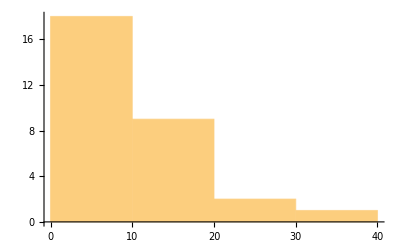

{0.853881,0.105139,0.00478321}

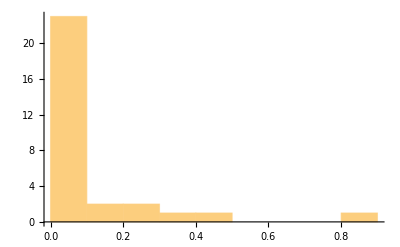

```mathematica
quartiles=Transpose[Quartiles/@body[[3]]];
diffs=quartiles[[3]]-quartiles[[1]];
{Max[diffs],Mean[diffs],Min[diffs]}
Histogram[diffs]
quartiles=Transpose[Quartiles/@body[[4]]];
diffs=quartiles[[3]]-quartiles[[1]];
{Max[diffs],Mean[diffs],Min[diffs]}
Histogram[diffs]
```

### Experiments plots

```mathematica
matricesA=ArrayPlot[#[[All,1;;All]]//Transpose,
ColorFunction->"ThermometerColors",
(*PlotLegends->Placed[Automatic,Right],*)
RotateLabel->True,
ImageSize->500,
FrameTicks->{
{Transpose[{(Range[body[[1,1]]//Length]),Rotate[#,90Degree]&/@(Reverse[Range[body[[1,1]]//Length]])}],None},
{{Range[#//Length],(Table[Table[Rotate["B"<>ToString[i]"T"<>ToString[j],90Degree],{i,10,35,5}],{j,15,35,5}]//Flatten)}//Transpose,
{Range[#//Length],((Rotate["μ ["<>ToString[#[[1]]]<>"] σ ["<>ToString[#[[2]]]<>"]",90Degree])&/@({Flatten[Partition[Mean/@#,5]],Flatten[Partition[StandardDeviation/@#,5]]}//Transpose))}//Transpose
}
}
]&/@body;
matricesB=ArrayPlot[#[[All,1;;All]]//Abs//Transpose,
ColorFunction->"ThermometerColors",
(*PlotLegends->Placed[Automatic,Right],*)
RotateLabel->True,
ImageSize->500,
FrameTicks->{
{Transpose[{(Range[body[[1,1]]//Length]),Rotate[#,90Degree]&/@(Reverse[Range[body[[1,1]]//Length]])}],None},
{{Range[#//Length],(Table[Table[Rotate["B"<>ToString[i]"T"<>ToString[j],90Degree],{i,10,35,5}],{j,15,35,5}]//Flatten)}//Transpose,
{Range[#//Length],((Rotate["μ ["<>ToString[#[[1]]]<>"] σ ["<>ToString[#[[2]]]<>"]",90Degree])&/@({Flatten[Partition[Mean/@#,5]],Flatten[Partition[StandardDeviation/@#,5]]}//Transpose))}//Transpose
}
}
]&/@body;
(*Export["Plots/Repetitions/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"experimentsDifferences.png","experimentsRatios.png","experimentsDifferencesSS.png","experimentsRatiosSS.png"},matrices}//Transpose)*)
```

### Contours

```mathematica
partitions=Partition[Median/@#,levelsT]&/@body;
contoursA=ListDensityPlot[#,
ColorFunction->"ThermometerColors",
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LabelStyle->(Directive[15,Gray]),LegendMargins->5(*LegendLabel->Placed[Style["Difference",Directive[25,Bold]],Center]*)],Right],
InterpolationOrder->2,
BaseStyle->Directive[Bold,25,Gray],
FrameLabel->{"Temperature","Breeding Sites"},
FrameTicks->{
{None,{Range[6],(""<>ToString[#])&/@Range[10,35,5]}//Transpose},
{None,{Range[5],(""<>ToString[#])&/@Range[15,35,5]}//Transpose}
}
,Epilog->Flatten[{PointSize[Medium],Opacity[.5],Black,Point[#]&/@Tuples[{Range[0,50,1],Range[0,50,1]}]}]
,ImageSize->375
]&/@partitions;
```

```mathematica
contoursB=ListDensityPlot[#//Abs,
ColorFunction->"ThermometerColors",
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->180,LabelStyle->(Directive[15,Gray]),LegendMargins->5(*LegendLabel->Placed[Style["Difference",Directive[25,Bold]],Center]*)],Right],
InterpolationOrder->2,
BaseStyle->Directive[Bold,25,Gray],
FrameLabel->{"Temperature","Breeding Sites"},
FrameTicks->{
{None,{Range[6],(""<>ToString[#])&/@Range[10,35,5]}//Transpose},
{None,{Range[5],(""<>ToString[#])&/@Range[15,35,5]}//Transpose}
}
,Epilog->Flatten[{PointSize[Medium],Opacity[.5],Black,Point[#]&/@Tuples[{Range[0,50,1],Range[0,50,1]}]}]
,ImageSize->375
]&/@partitions;
```

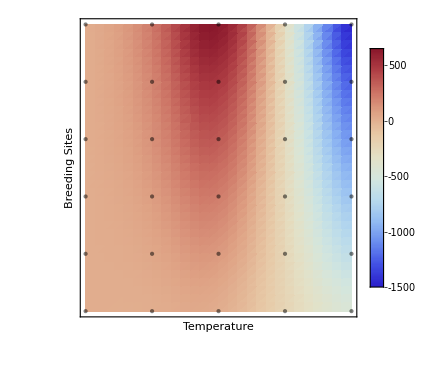
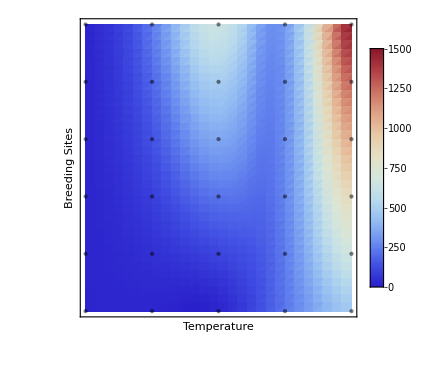
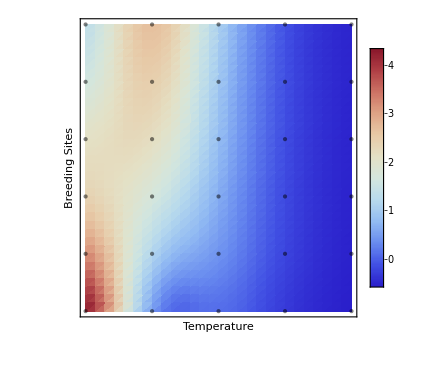
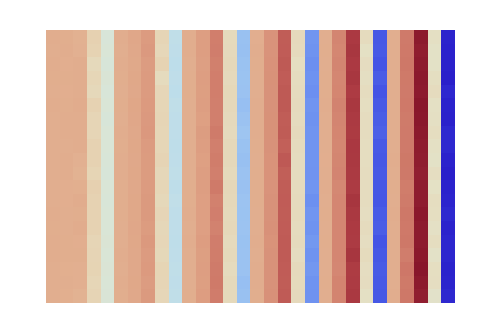
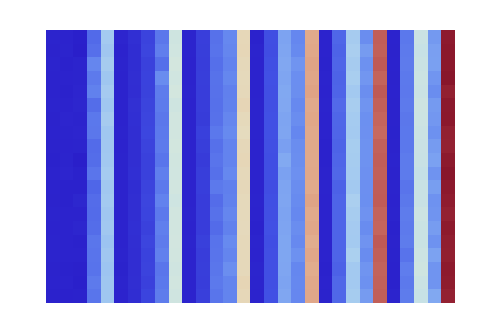
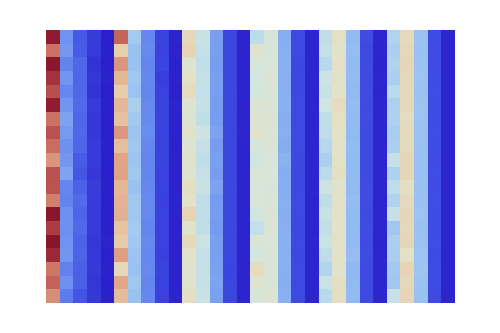
|  | 
(a) | (b) | (c)
-Graphics- | -Graphics- | -Graphics-
 |  | 
-Graphics- | -Graphics- | -Graphics-
 |  | 
 |  |

/Users/chipdelmal/Desktop/contourResponsesB.pdf

```mathematica
Grid[{
{},
Style[#,25,Gray]&/@{"(a)","(b)","(c)"},
{contoursA[[3]],contoursB[[3]],contoursA[[4]]},
(*Style[#,25,Gray]&/@{"(d)","(e)","(f)"},*){},
Rotate[#,-90Degree]&/@{matricesA[[3]],matricesB[[3]],matricesA[[4]]},
{},
{}
},Frame->{None,None,{{{1,7},{1,1}}->True,{{1,7},{2,2}}->True,{{1,7},{3,3}}->True}},Alignment->Right,FrameStyle->Directive[Gray,Thick]]
Export[$HomeDirectory<>"/Desktop/"<>"contourResponsesB.pdf",%]
```

```mathematica
(*Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"contourDifferencesAbs.png","contourRatiosAbs.png","contourDifferencesSSAbs.png","contourRatiosSSAbs.png"},contoursB}//Transpose)*)
```

```mathematica
(*threeDA=ListPlot3D[#,ColorFunction->"TemperatureMap",InterpolationOrder->2]&/@partitions
contoursB=ListContourPlot[#//Abs,
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
InterpolationOrder->2,
FrameTicks->{
{{Range[100],("B"<>ToString[#])&/@Range[15,510,5]}//Transpose,None},
{None,{Range[99],("T"<>ToString[#])&/@Range[20,510,5]}//Transpose}
}
]&/@partitions
threeDB=ListPlot3D[#//Abs,ColorFunction->"TemperatureMap",InterpolationOrder->2]&/@partitions*)

(*Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"contourDifferences.png","contourRatios.png","contourDifferencesSS.png","contourRatiosSS.png"},contoursA}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"contourDifferencesAbs.png","contourRatiosAbs.png","contourDifferencesSSAbs.png","contourRatiosSSAbs.png"},contoursB}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"3dcontourDifferences.png","3dcontourRatios.png","3dcontourDifferencesSS.png","3dcontourRatiosSS.png"},threeDA}//Transpose)
Export["Plots/Real/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"3dcontourDifferencesAbs.png","3dcontourRatiosAbs.png","3dcontourDifferencesSSAbs.png","3dcontourRatiosSSAbs.png"},threeDB}//Transpose)*)
```

## Minitab Fits

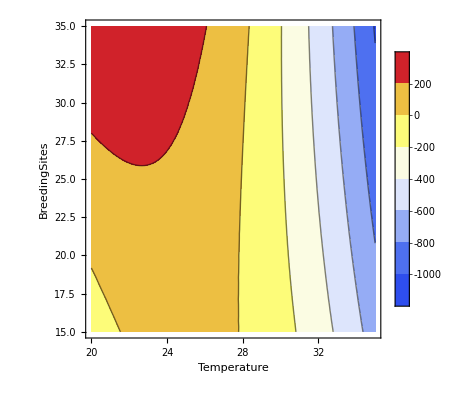
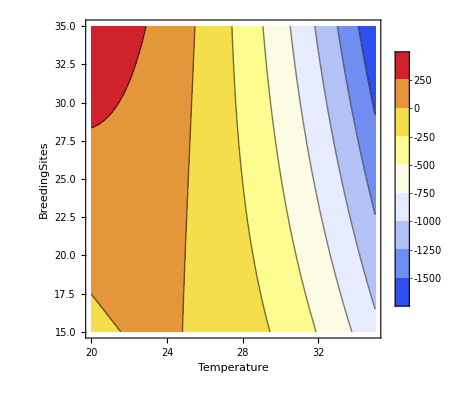
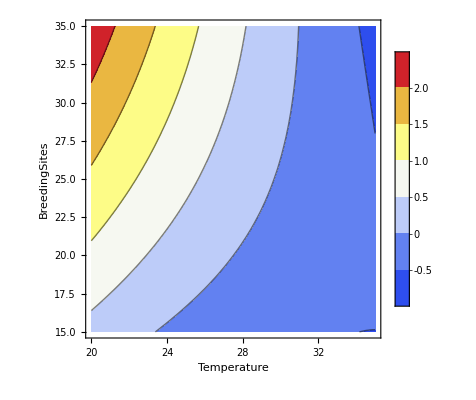
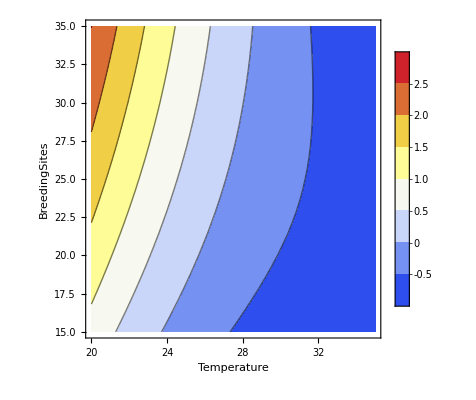

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

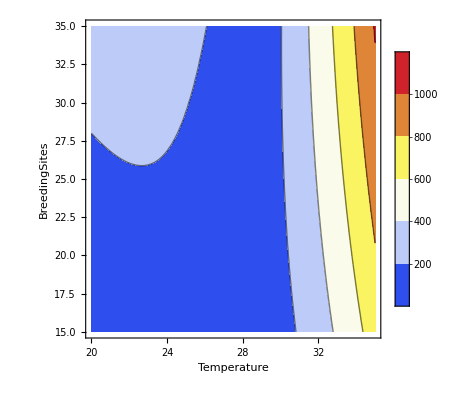
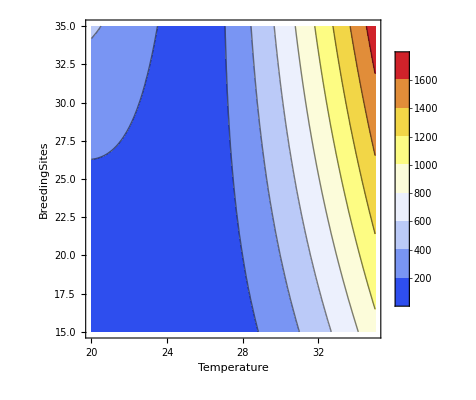
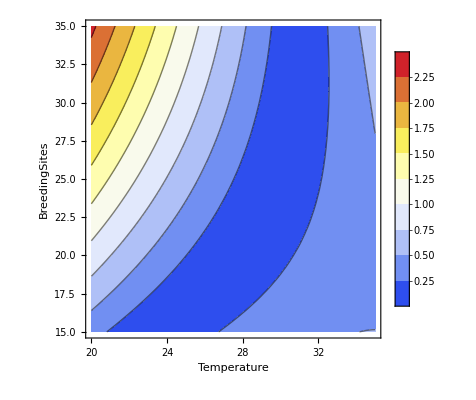
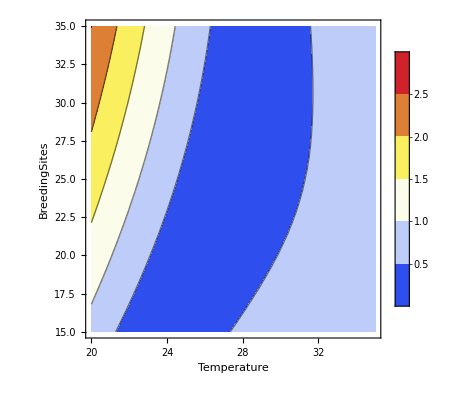

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{Plots/Fits/FitcontourDifferences.png,Plots/Fits/FitcontourRatios.png,Plots/Fits/FitcontourDifferencesSS.png,Plots/Fits/FitcontourRatiosSS.png}

{Plots/Fits/FitcontourDifferencesAbs.png,Plots/Fits/FitcontourRatiosAbs.png,Plots/Fits/FitcontourDifferencesSSAbs.png,Plots/Fits/FitcontourRatiosSSAbs.png}

{Plots/Fits/Fit3dcontourDifferences.png,Plots/Fits/Fit3dcontourRatios.png,Plots/Fits/Fit3dcontourDifferencesSS.png,Plots/Fits/Fit3dcontourRatiosSS.png}

{Plots/Fits/Fit3dcontourDifferencesAbs.png,Plots/Fits/Fit3dcontourRatiosAbs.png,Plots/Fits/Fit3dcontourDifferencesSSAbs.png,Plots/Fits/Fit3dcontourRatiosSSAbs.png}

```mathematica
Clear[BS,Temps];
factDiff[BreedingSites_,Temperature_]:=-5309+66.7 BreedingSites+391.1 Temperature+0.179 BreedingSites*BreedingSites-7.131 Temperature*Temperature-2.622 BreedingSites*Temperature
factDiffSS[BreedingSites_,Temperature_]:=-5187+98.9 BreedingSites+380.3 Temperature+0.158 BreedingSites*BreedingSites-6.856 Temperature*Temperature-4.157 BreedingSites*Temperature
factErr[BreedingSites_,Temperature_]:=0.117+0.2812 BreedingSites-0.1620 Temperature-0.000867 BreedingSites*BreedingSites+0.003825 Temperature*Temperature-0.006966 BreedingSites*Temperature
factErrSS[BreedingSites_,Temperature_]:=6.917+0.2550 BreedingSites-0.6153 Temperature-0.000863 BreedingSites*BreedingSites+0.011221 Temperature*Temperature-0.006373 BreedingSites*Temperature
funArr={factDiff[BS,Temps],factDiffSS[BS,Temps],factErr[BS,Temps],factErrSS[BS,Temps]};
c=ContourPlot[#,{Temps,20,35},{BS,15,35},FrameLabel->{"Temperature","BreedingSites"},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr
p=Plot3D[#,{Temps,20,35},{BS,15,35},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr

cAbs=ContourPlot[#//Abs,{Temps,20,35},{BS,15,35},FrameLabel->{"Temperature","BreedingSites"},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr
pAbs=Plot3D[#//Abs,{Temps,20,35},{BS,15,35},PlotLegends->Automatic,ColorFunction->"TemperatureMap"]&/@funArr


Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"FitcontourDifferences.png","FitcontourRatios.png","FitcontourDifferencesSS.png","FitcontourRatiosSS.png"},c}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"FitcontourDifferencesAbs.png","FitcontourRatiosAbs.png","FitcontourDifferencesSSAbs.png","FitcontourRatiosSSAbs.png"},cAbs}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"Fit3dcontourDifferences.png","Fit3dcontourRatios.png","Fit3dcontourDifferencesSS.png","Fit3dcontourRatiosSS.png"},p}//Transpose)
Export["Plots/Fits/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"Fit3dcontourDifferencesAbs.png","Fit3dcontourRatiosAbs.png","Fit3dcontourDifferencesSSAbs.png","Fit3dcontourRatiosSSAbs.png"},pAbs}//Transpose)
```

```mathematica
Minimize[{Abs[#],15≤BS≤35,20≤Temps≤35},{BS,Temps}]&/@{factDiff[BS,Temps],factDiffSS[BS,Temps],factErr[BS,Temps],factErrSS[BS,Temps]}
Minimize[{Abs[factDiff[BS,Temps]+factDiffSS[BS,Temps]],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
Minimize[{Abs[factErr[BS,Temps]+factErrSS[BS,Temps]],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
Minimize[{Abs[factDiff[BS,Temps]+factDiffSS[BS,Temps]+factErr[BS,Temps]*100+factErrSS[BS,Temps]*100],15≤BS≤35,20≤Temps≤35},{BS,Temps}]
```

{{1.81899×10^-12,{BS→30.5439,Temps→28.145}},{4.1382×10^-11,{BS→15.5287,Temps→21.2254}},{4.89839×10^-11,{BS→20.5423,Temps→27.822}},{5.76977×10^-10,{BS→31.1898,Temps→28.1857}}}

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{9.09495×10^-13,{BS→15.5757,Temps→21.2838}}

{8.60556×10^-11,{BS→22.4397,Temps→27.3664}}

{2.03229×10^-10,{BS→15.0147,Temps→20.2888}}

```mathematica
temp=25;
Plot[{
factDiff[bs,temp],
factDiffSS[bs,temp],
factErr[bs,temp]*100,
factErrSS[bs,temp]*100
},{bs,0,35}
,AxesLabel->{"Breeding Sites","Difference"},
PlotLegends->{"Difference","SS Difference","Error*100","SS Error*200"}]
```

$Aborted[]

## Dynamics Differences

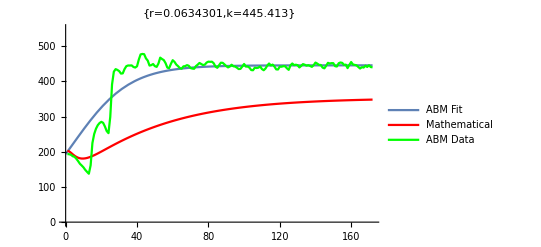

funArr

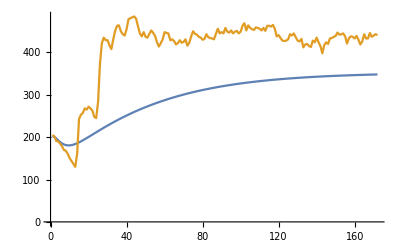

```mathematica
sampleRate=288;
point={20,25};
headTestB=HeadComparisonBetweenABMAndMathematical["/GeneratedData/ValidationSweeps/PopDynAt"<>ToString[point[[1]]]<>ToString[point[[2]]],sampleRate];
CompareABMAndMathematicalPlots[headTestB,4]
#/.{BS->point[[1]],Temps->point[[2]]}&/@funArr

ListPlot[{headTestB[[1,4]],headTestB[[2,1,4]]},Joined->True]
```

## Climate Error (see parameters export - superseeded by “Experiment 1”)

```mathematica
breedingSitesNumber=20;
timeInSection={{15,0.00039092117663288087},{16,0.0011075586658537326},{17,0.0028304175036653507},{18,0.00652445195470739},{19,0.013565960790938398},{20,0.025443269103349587},{21,0.04304409432489916},{22,0.0656862753154703},{23,0.09041860236944899},{24,0.11227015507880694},{25,0.12574626983023768},{26,0.12704296320915381},{27,0.11577928845540386},{28,0.09517776840981118},{29,0.07057708975647792},{30,0.04720786450097014},{31,0.028483000104885137},{32,0.015501576365713698},{33,0.007609959638019803},{34,0.003369786785840212},{35,0.0013459624176445084}};
errorInNumber=(factDiff[breedingSitesNumber,#[[1]]])&/@timeInSection;
errorInPercentage=(#[[2]]*factErr[breedingSitesNumber,#[[1]]])&/@timeInSection;
{errorInNumber,errorInPercentage}
```

{{-423.025,-308.256,-207.609,-121.084,-48.681,9.6,53.759,83.796,99.711,101.504,89.175,62.724,22.151,-32.544,-101.361,-184.3,-281.361,-392.544,-517.849,-657.276,-810.825},{0.000605605,0.00153008,0.00345505,0.0069601,0.0124772,0.0198356,0.0278212,0.034155,0.0362115,0.0323212,0.0229078,0.0105888,-0.000994891,-0.00891321,-0.0121263,-0.0114762,-0.00875844,-0.0056582,-0.00316295,-0.00154799,-0.0006679}}

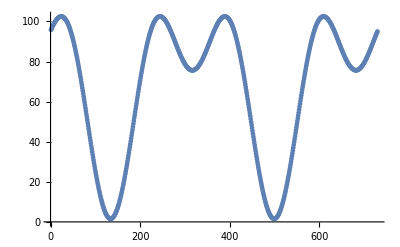
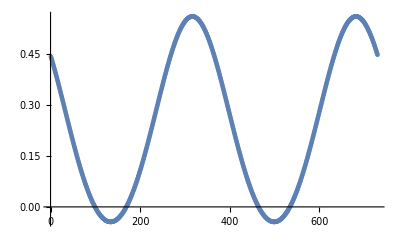

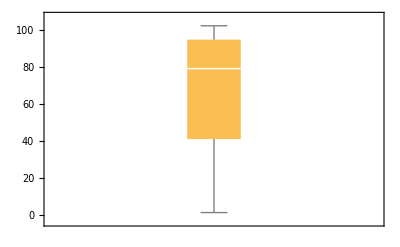
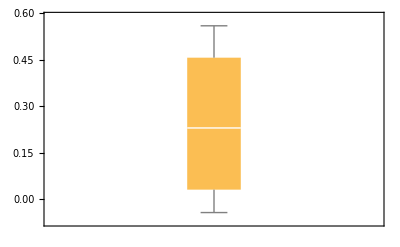

```mathematica
temps=(climateModel/.x->#)&/@Range[2*365];
{ListPlot[factDiff[breedingSitesNumber,#]&/@temps],ListPlot[factErr[breedingSitesNumber,#]&/@temps]}
{BoxWhiskerChart[factDiff[breedingSitesNumber,#]&/@temps],BoxWhiskerChart[factErr[breedingSitesNumber,#]&/@temps]}
```

## Experiment 2 : Varying Temperature

## Load Data

```mathematica
sampleRate=288;
secondsPerTick=300;
path=ParentDirectory[]<>"/GeneratedData/CatemacoBaselineNew/";
stages={"AdultPopulation","Temperature","BreedingZones"};
colorsA={Blue,Red,Green,Orange,Purple,Yellow,Brown,Black};
colorsB={LightBlue,LightRed,LightGreen,LightOrange,LightPurple,LightYellow,LightBrown,Gray};
dataRaw=ReturnData[path,stages,sampleRate];
```

## Dynamics

### Stochastic Model

```mathematica
{bs,temperature}={22.5,30};
{BS,me,egn,ef,ma,ml,mp,α0}={bs,.01,63,.83,.09,mlf[temperature+273.15],mpf[temperature+273.15],1.5};
{a0,α}={.75, αf[α0, bs]};
schoolfield=CalculateSchoolfieldSet[24.542238030594344-2.865555479949232*Cos[0.8337037265403161+0.017202423838958484*t],{eggDevelopment,larvaDevelopment,pupaDevelopment,gonotropicCycleA1Development,gonotropicCycleA2Development}];
stochasticPopDynamics=CalculateAndRunStochasticModel[schoolfield,{BS,me,egn,ma,ml,mp,α,ef,a0},500,5*365][[4]];
temps=24.542238030594344-2.865555479949232*Cos[0.8337037265403161+0.017202423838958484*#]&/@Range[1,stochasticPopDynamics//Length];
stochasticPlot=Transpose[{temps,stochasticPopDynamics}][[365;;365+365]]//ListPlot[#,Joined->True,PlotStyle->Thickness[.0075],PlotLegends->(Style[#,25,Gray]&/@{"Stochastic"})]&;
stochasticPlotD=stochasticPopDynamics[[365*2;;365+3*365]]//ListPlot[#,Joined->True,PlotStyle->Thickness[.0075],PlotLegends->(Style[#,25,Gray]&/@{"Stochastic"})]&;
```

### Functions

```mathematica
Options[PlotRepetitions]:={PlotRange->{0,1500},ImageSize->600}
PlotRepetitions[repetitionsAndAveragesData_,stages_,colorsMean_,colorsRepetition_,OptionsPattern[]]:=Module[{colorsA=colorsMean,colors=colorsRepetition,iterationsPlot,averagesPlot,data,data2},
data=repetitionsAndAveragesData[[1]];
data2=repetitionsAndAveragesData[[2]];
iterationsPlot=Show[Table[ListPlot[data[[i]],Joined->True,PlotStyle->{colors[[i]]},ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]],{i,1,stages//Length}],ImageSize->Large];
averagesPlot=ListPlot[data2,Joined->True,Frame->True,PlotStyle->Transpose[{ConstantArray[Thickness[.0075],Length[colorsA]],colorsA}],ImageSize->OptionValue[ImageSize],PlotRange->OptionValue[PlotRange]];
Grid[{
{
Show[{iterationsPlot,averagesPlot},
ImageSize->OptionValue[ImageSize],
Frame->True,
BaseStyle->25,
FrameTicksStyle->17.5,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Days","Adult Mosquitoes Number"},
Grid->True
],
Grid[Table[{colorsA[[i]],stages[[i]]},{i,1,stages//Length}]],
Grid[Table[{colors[[i]]},{i,1,stages//Length}]]
}
}]
]
TempPopPlot[dataRaw_,style1_,style2_,popIndex_,tempIndex_]:=Module[{lowLimit,adults,temps,meanPlot,data,repetitionsPlot},
(*MeanPlot*)
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
meanPlot=ListPlot[{temps,adults}//Transpose,Joined->True,Frame->True,AxesLabel->{"Temperature","Population"},PlotStyle->style1,InterpolationOrder->1];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
repetitionsPlot=ListPlot[data,Joined->True,PlotStyle->style2,AxesLabel->{"Days","Population"},InterpolationOrder->2];
(*FullPlot*)
Show[{repetitionsPlot,meanPlot}]
]
```

### Pop VS Time

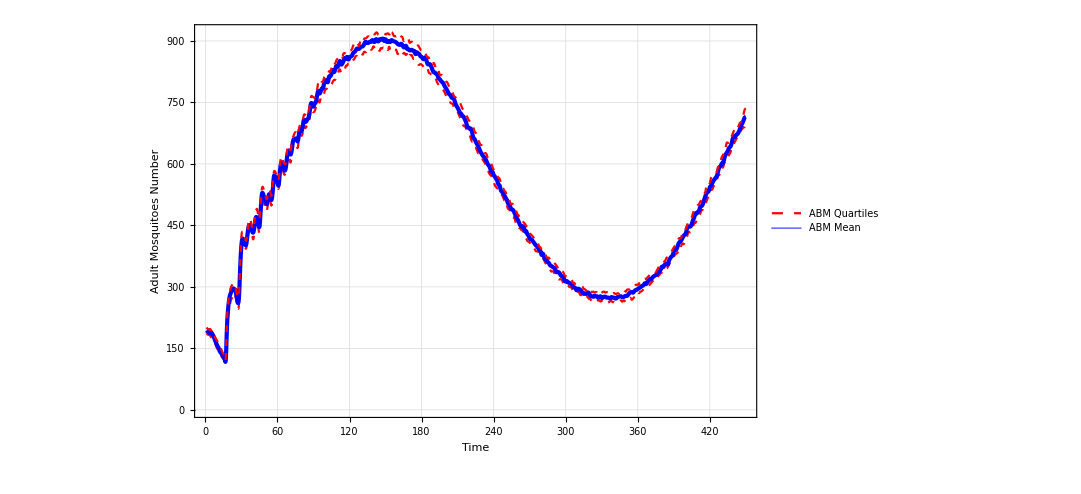

/Users/chipdelmal/Desktop/timeVSpopSize.pdf

```mathematica
repetitionsAndAveragesData=dataRaw[[3]];
colors=colorsB;

data=repetitionsAndAveragesData[[1]];
data2=repetitionsAndAveragesData[[2]];
days=data[[1,1,All,1]];
popSizes=#[[All,2]]&/@data[[1]];
popSizesQuartiles=Transpose[Quartiles/@Transpose[popSizes]];
popSizesFinal=Transpose[{days,#}]&/@popSizesQuartiles;
popSizesPlot=ListPlot[popSizesFinal,
Joined->True,
InterpolationOrder->2,
ImageSize->800,
Filling->None,
PlotStyle->{{Dashed,Red},{Thickness[.00375], Blue},{Dashed,Red}},
GridLines->Automatic,
Frame->True,
BaseStyle->Directive[30],
(*PlotLabel->Style["Temperature Effects on Mosquito Population Sizes",35,Gray],*)
FrameTicksStyle->20,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Time","Adult Mosquitoes Number"},
PlotLegends->(Style[#,25,Gray]&/@{"ABM Quartiles","ABM Mean"})
]
Export[$HomeDirectory<>"/Desktop/"<>"timeVSpopSize.pdf",%]
```

### Pop VS Temp

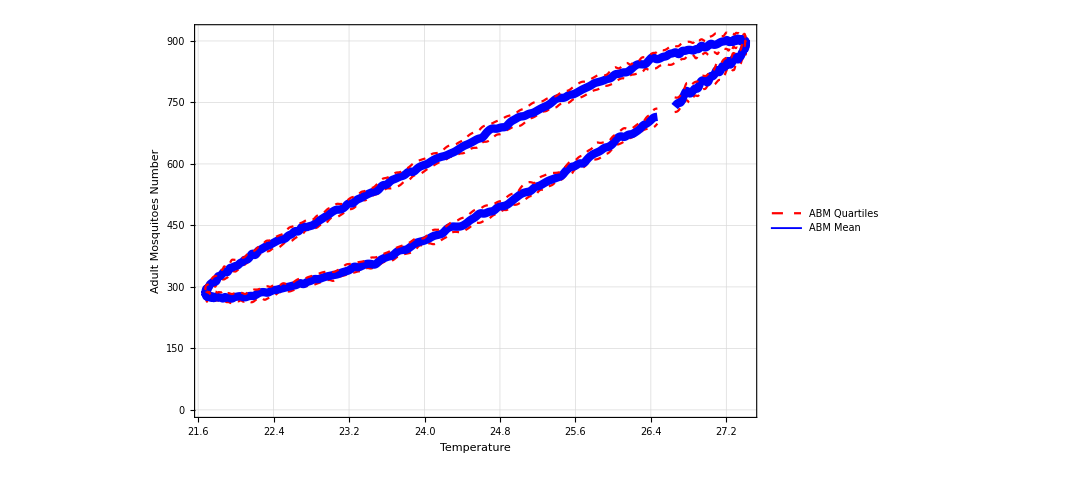

/Users/chipdelmal/Desktop/temperatureVSpopSize.pdf

```mathematica
{adultIndex,tempIndex}={1,2};
popIndex=adultIndex;
lowLimit=Floor[(dataRaw[[2,2,popIndex]]//Length)*.2];
adults=dataRaw[[2,2,popIndex]][[lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
(*RepetitionsPlot*)
lowLimit=Floor[((dataRaw[[2,1,popIndex]]//Transpose)[[1]]//Length)*.2];
adults=(dataRaw[[2,1,popIndex]]//Transpose)[[All,lowLimit;;All]];
temps=dataRaw[[2,2,tempIndex]][[lowLimit;;All]];
data=({temps,#}//Transpose)&/@adults;
quartilesAdults=Transpose[Quartiles/@Transpose[adults]];
data=({temps,#}//Transpose)&/@quartilesAdults;
repetitionsPlot=ListPlot[data,
Joined->True,
InterpolationOrder->2,
ImageSize->800,
Filling->None,
PlotStyle->{{Dashed,Red},{Thickness[.0075], Blue},{Dashed,Red}},
GridLines->Automatic,
Frame->True,
BaseStyle->Directive[30],
(*PlotLabel->Style["Temperature Effects on Mosquito Population Sizes",35,Gray],*)
FrameTicksStyle->20,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Temperature","Adult Mosquitoes Number"},
PlotLegends->(Style[#,25,Gray]&/@{"ABM Quartiles","ABM Mean"})
]
Export[$HomeDirectory<>"/Desktop/"<>"temperatureVSpopSize.pdf",%]
```

### Contrasts

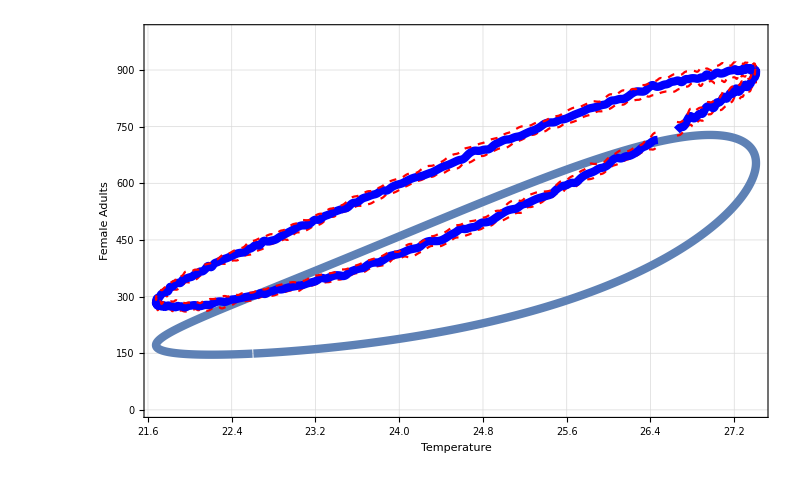
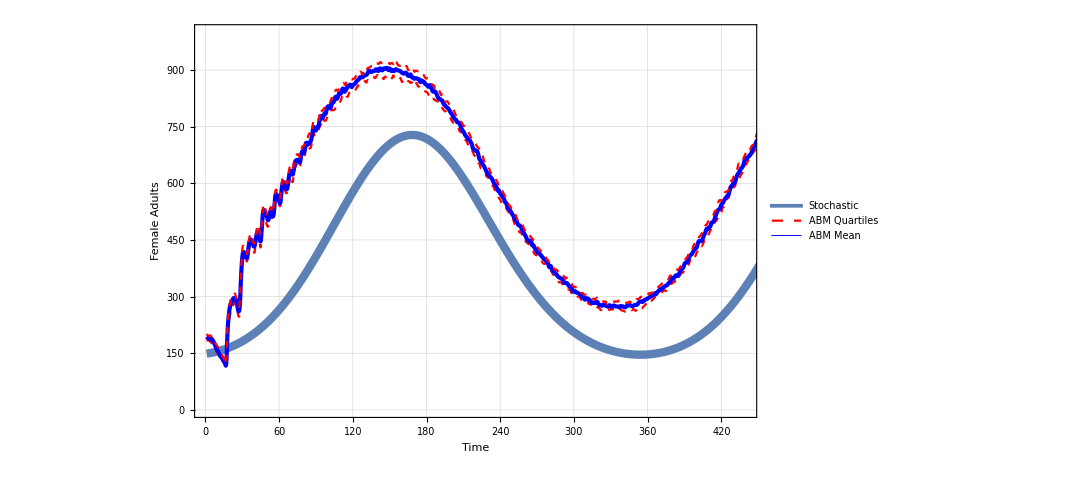
-Graphics- | -Graphics-
(a) | (b)

/Users/chipdelmal/Desktop/seasonality.pdf

```mathematica
tempVSFemales=Show[stochasticPlot,repetitionsPlot,
PlotRange->{0,1000},
ImageSize->800,
GridLines->Automatic,
Frame->True,
BaseStyle->Directive[30],
FrameTicksStyle->20,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Temperature","Female Adults"}
];
timeVSFemales=Show[stochasticPlotD,popSizesPlot,
PlotRange->{{0,440},{0,1000}},
ImageSize->800,
GridLines->Automatic,
Frame->True,
BaseStyle->Directive[30],
FrameTicksStyle->20,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Time","Female Adults"}
];
Grid[{{tempVSFemales[[1,1]],timeVSFemales},Style[#,Gray,40]&/@{"(a)","(b)"}},Alignment->Right]
Export[$HomeDirectory<>"/Desktop/"<>"seasonality.pdf",%]
```

### Old

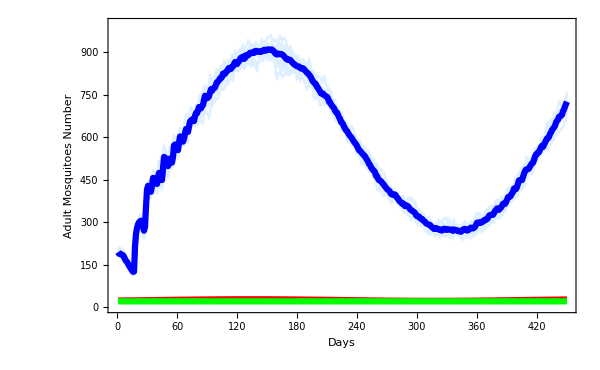
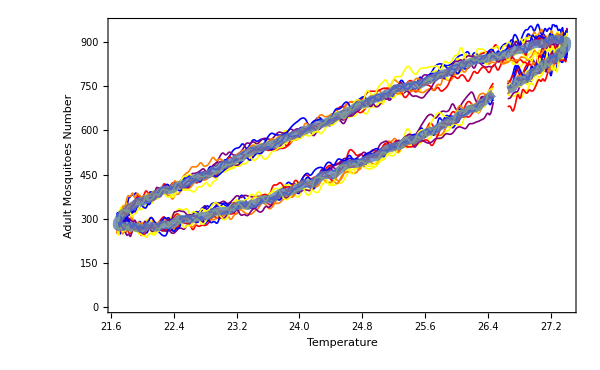
title | PopulationDynamics. | 
author | HMSC | 
date | {Tue 16 Jun 2015 17:40:36,Thu 8 Dec 2016 10:51:19} | 
description | Calibration attempts with stochastic model as reference. | 
parameter | SecondsPerTick | 300
parameter | ScenarioNumber | 2
independent | Temperature | {25}
-Graphics- | RGBColor[0, 0, 1] | AdultPopulation
RGBColor[1, 0, 0] | Temperature
RGBColor[0, 1, 0] | BreedingZones | RGBColor[0.87, 0.94, 1]
RGBColor[1, 0.85, 0.85]
RGBColor[0.88, 1, 0.88] | -Graphics-

```mathematica
{adultIndex,tempIndex}={1,2};
header=Grid[Flatten[dataRaw[[1]],1],Background->LightBlue];
repetitions=PlotRepetitions[dataRaw[[3]],stages,colorsA,colorsB,PlotRange->{0,1000}];
tempPlot=Show[TempPopPlot[dataRaw,{Thickness[.01],Opacity[.8],PointSize[.0075]},{{Thickness[.002],Blue},{Thickness[.002],Yellow},{Thickness[.002],Red},{Thickness[.002],Orange},{Thickness[.002],Purple}},adultIndex,tempIndex],ImageSize->600,
Frame->True,
BaseStyle->25,
FrameTicksStyle->17.5,
FrameStyle->Directive[Gray,Thick],
FrameLabel->{"Temperature","Adult Mosquitoes Number"},
Grid->True
];
Grid[{{header},{Grid[{{repetitions,tempPlot}}]}}]
(*
Export["Plots/Dynamics/header.png",header,ImageSize->2000,ImageResolution->200]
Export["Plots/Dynamics/repetitions.png",repetitions,ImageSize->1500,ImageResolution->200]
Export["Plots/Dynamics/ellipse.png",tempPlot,ImageSize->2000,ImageResolution->200]*)
```

## Temp Population correlation

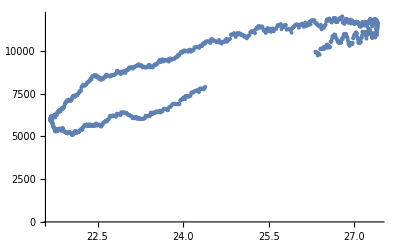
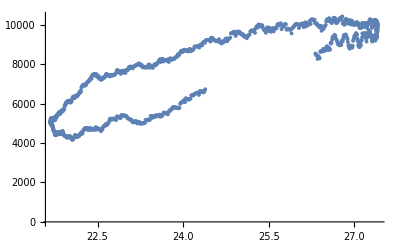
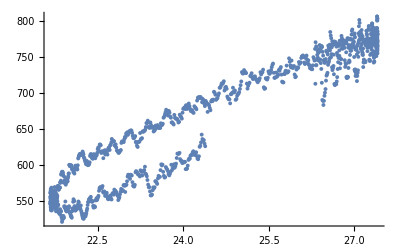
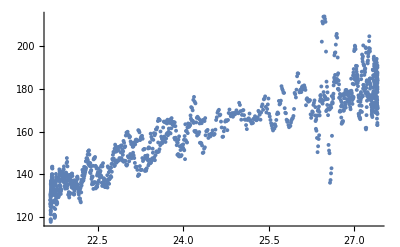
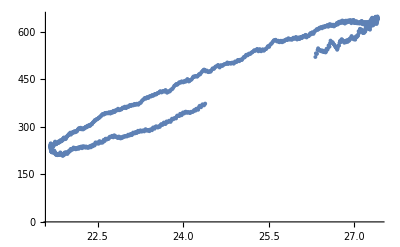
MosquitoPopulation | EggsPopulation | LarvaPopulation | PupaPopulation | AdultPopulation
0.902053 | 0.888989 | 0.95849 | 0.912921 | 0.975777
7.68471171230133×10^-509 | 1.15334204316888×10^-462 | 6.76229482070948×10^-790 | 1.41812402367543×10^-724 | 6.46685378734017×10^-1061
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Plots/Correlation/correlation.png

```mathematica
data=Table[
lowLimit=Floor[(dataRaw[[2,2,tempIndex]]//Length)*.2];
temps=dataRaw[[3,2,tempIndex]][[All,2]][[lowLimit;;All]];
popSize=dataRaw[[3,2,i]][[All,2]][[lowLimit;;All]]//N;
{Correlation[temps,popSize],CorrelationTest[{temps,popSize}//Transpose,VerifyTestAssumptions->All],ListPlot [{temps,popSize}//Transpose]}
,{i,1,5}];
correlation=Grid[Prepend[(data//Transpose),stages[[1;;5]]],Background->{None,{LightBlue}},Frame->All]

Export["Plots/Correlation/correlation.png",correlation,ImageSize->1000,ImageResolution->150]
```

## Ellipse

27761.7

6177.92 x^2-151.951 x y-239489. x+y^2+2892.16 y+2.32814×10^6==0

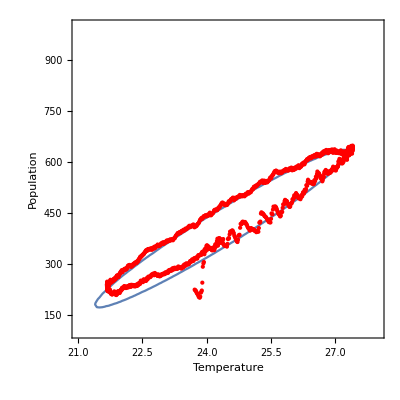

Plots/Ellipse/EllipseExperiment.png

```mathematica
Clear[l,a,b,c,d]
(*GenerateDataPoints*)
{adults,temp}={dataRaw[[2,2,5]][[100;;All]]//N,dataRaw[[2,2,tempIndex]][[100;;All]]//N};
points={temp,adults}//Transpose;
(*ModelFit*)
lin={#1^2,#1,#2,2 #1 #2,#2^2}&@@@points;
lm=LinearModelFit[lin,{1,a,b,c,d},{a,b,c,d}];
lm["AIC"]
pa=lm["BestFitParameters"];
w[x_,y_]:=pa.{1,x^2,x,y,2 x y}-y^2;
TraditionalForm[-w[x,y]==0]
ellipse=ContourPlot[w[x,y]==0,{x,21,28},{y,100,1000},Epilog->{Red,Point[points]},FrameLabel->{"Temperature","Population"}]
Export["Plots/Ellipse/EllipseExperiment.png",ellipse,ImageSize->1000,ImageResolution->150]
```

## Error Plots (first run minitab fits on Experiment 1)

### List and Whisker

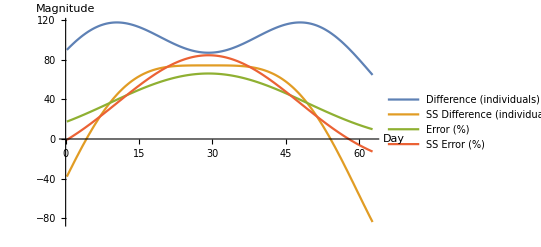

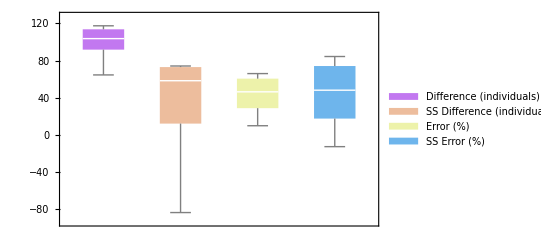

```mathematica
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,1]][[200;;All]],dataRaw[[2,2,tempIndex]][[200;;All]]};
breedingSites=ConstantArray[20,(adults//Length)]//Flatten;
(**)
plotPairs={temps,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
(**)
error1=factDiff[#[[1]],#[[2]]]&/@errorPairs;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
error3=factErr[#[[1]],#[[2]]]&/@errorPairs;
error4=factErrSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
results=Grid[{
{ListPlot[#,Joined->True,AxesLabel->{"TimeStep","Error"},ImageSize->500],BoxWhiskerChart[#,ImageSize->500]}
}]&/@{error1,error2,error3,error4};
(**)
Export["Plots/Error/"<>#[[1]],#[[2]],ImageSize->1000,ImageResolution->150]&/@({{"errorDifferences.png","errorRatios.png","errorDifferencesSS.png","errorRatiosSS.png"},results}//Transpose);
ls=ListPlot[({TickToDay[#,secondsPerTick]&/@(Range[error1//Length]*sampleRate)//N,#}//Transpose)&/@{error1,error2,error3*100,error4*100},Joined->True,PlotLegends->{"Difference (individuals)","SS Difference (individuals)","Error (%)","SS Error (%)"},AxesLabel->{"Day","Magnitude"}]
bw=BoxWhiskerChart[{error1,error2,error3*100,error4*100},ChartStyle->"Pastel",ChartLegends->{"Difference (individuals)","SS Difference (individuals)","Error (%)","SS Error (%)"}]
Export["Plots/TemperatureErrors/listError.png",ls,ImageSize->1000,ImageResolution->150];
Export["Plots/TemperatureErrors/boxError.png",bw,ImageSize->1000,ImageResolution->150];
```

### Ellipse

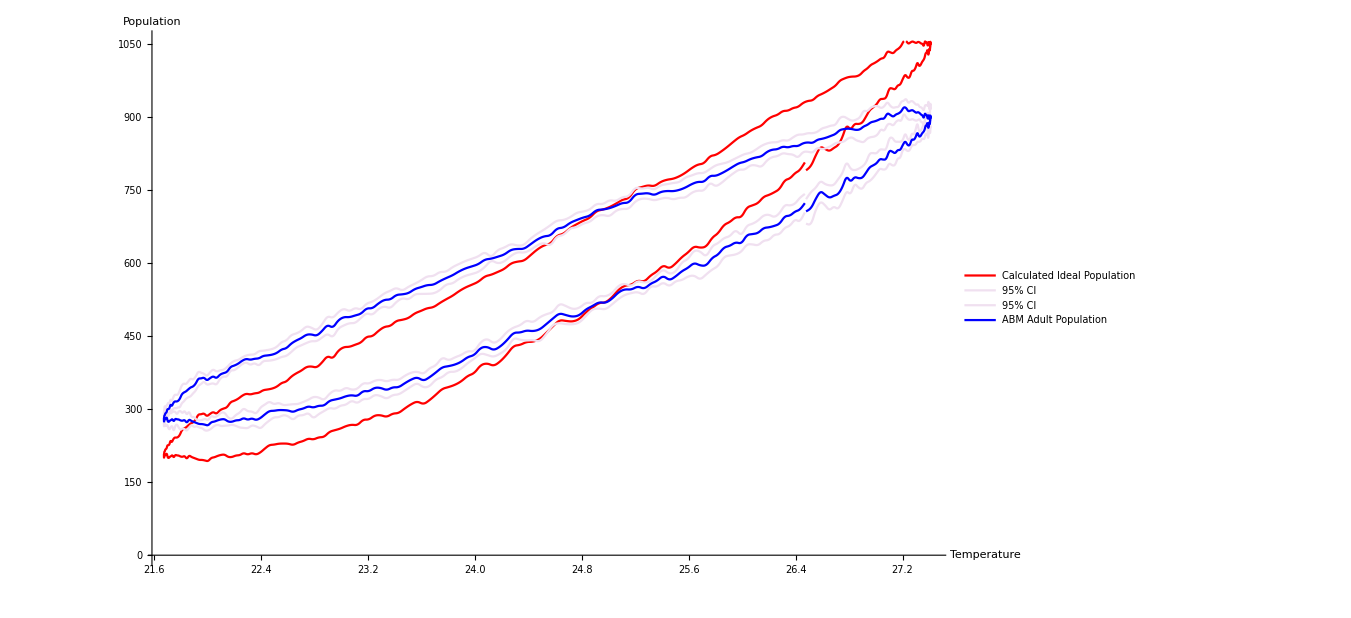

Plots/Error/errorEllipse.png

```mathematica
start=85;
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,adultIndex]][[start;;All]],dataRaw[[2,2,tempIndex]][[start;;All]]};
breedingSites=dataRaw[[2,2,3]][[start;;All]];
(**)
plotPairs={temps,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
adultsCI=MeanCI/@dataRaw[[2,1,adultIndex]][[start;;All]];
(**)
plotPairsMin={temps,adultsCI[[All,1]]}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMax={temps,adultsCI[[All,2]]}//Transpose;
(**)
plotPairsErr={temps,adults-error2}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMin={temps,adultsCI[[All,1]]}//Transpose;
plotPairsMean={temps,adults}//Transpose;
plotPairsMax={temps,adultsCI[[All,2]]}//Transpose;
(**)
errorEllipse=ListPlot[{plotPairsErr,plotPairsMin,plotPairsMax,plotPairsMean}
,Joined->True
,PlotStyle->{Red,LightPurple,LightPurple,Blue}
,PlotRange->{0,All}
,AxesLabel->{"Temperature","Population"}
,PlotLegends->{"Calculated Ideal Population","95% CI","95% CI","ABM Adult Population"}
,ImageSize->1000
,InterpolationOrder->2
]
Export["Plots/Error/errorEllipse.png",errorEllipse,ImageSize->2000,ImageResolution->300]
```

### Dynamic

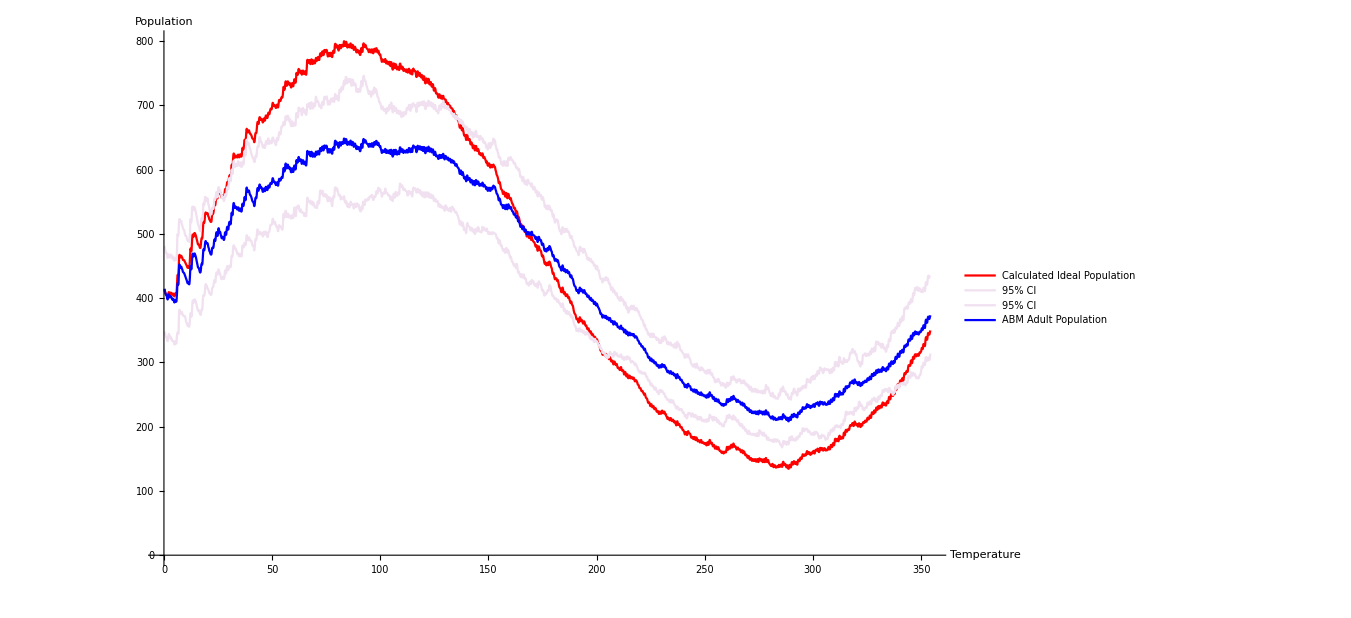

Plots/Error/errorList.png

```mathematica
(*GenerateDataPoints*)
{adults,temps}={dataRaw[[2,2,adultIndex]][[200;;All]],dataRaw[[2,2,tempIndex]][[200;;All]]};
days=(TickToDay[#,secondsPerTick]&/@(Range[error1//Length]*sampleRate)//N);
breedingSites=ConstantArray[20,(adults//Length)]//Flatten;
(**)
plotPairs={days,adults}//N//Transpose;
errorPairs={breedingSites,temps}//Transpose;
error2=factDiffSS[#[[1]],#[[2]]]&/@errorPairs;
(**)
adultsCI=MeanCI/@dataRaw[[2,1,adultIndex]][[200;;All]];
(**)
plotPairsMin={days,adultsCI[[All,1]]}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMax={days,adultsCI[[All,2]]}//Transpose;
(**)
plotPairsErr={days,adults-error2}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMin={days,adultsCI[[All,1]]}//Transpose;
plotPairsMean={days,adults}//Transpose;
plotPairsMax={days,adultsCI[[All,2]]}//Transpose;
(**)
errorEllipse=ListPlot[{plotPairsErr,plotPairsMin,plotPairsMax,plotPairsMean}
,Joined->True
,PlotStyle->{Red,LightPurple,LightPurple,Blue}
,PlotRange->{0,All}
,AxesLabel->{"Temperature","Population"}
,PlotLegends->{"Calculated Ideal Population","95% CI","95% CI","ABM Adult Population"}
,ImageSize->1000
,InterpolationOrder->2
]
Export["Plots/Error/errorList.png",errorEllipse,ImageSize->2000,ImageResolution->300]
```

## Experiment 3 : Optimisation

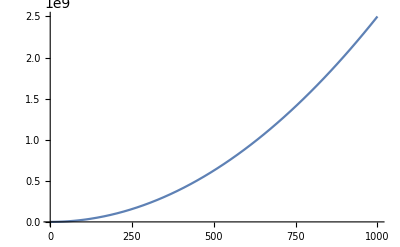

```mathematica
costPerIndividual=50;
(*MinimisationFitnessFunction*)
FitnesFunction[population_,costPerIndividual_,releasesNumber_]:=population+(costPerIndividual*releasesNumber)^2
Plot[FitnesFunction[500,costPerIndividual,releasedIndividuals],{releasedIndividuals,1,1000}]
```

## Experiment 4 : Network

## Network

```mathematica
mixFunction=Mean;
imageSize=500;
edgeshape[e_,___]:={Arrowheads[{{.0005,.5}}],Arrow[e]};
varStyle="Both";
graphLay="CircularEmbedding";
vSize=.5;
lThick=.0025;
clusteringMethod="Modularity";
mixFunction=Median;
```

### Direct

```mathematica
SetDirectory[NotebookDirectory[]];
path=ParentDirectory[]<>"/GeneratedData/PopDynAt20";
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
(*GetExperimentDescription*)
header=GetExperimentsSetHeader[xmlSet];
parameters=GetExperimentsSetParameters[xmlSet];
(*GetContactsSection*)
cSect=GetExperimentsSetContactsSection[xmlSet];
(*GetTransitionsMatrix*)
labels=GetExperimentsSetContactLabels[cSect];
contactsMatrix=GetExperimentSetContactsTransitionsWithPattern[cSect,labels,mixFunction];
contactsMatrices=GetExperimentSetRawContactsTransitionsWithPattern[cSect,labels];
(*GraphTransitions*)
frequenciesGraph=GraphTransitionsFrequencies[contactsMatrix,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
frequenciesScale=GridColorScaleFrequency[10,10,contactsMatrix];
(*Communities*)
communities=FindGraphCommunities[frequenciesGraph,Method->clusteringMethod];
communitiesGraph=CommunityGraphPlot[frequenciesGraph,communities,ImageSize->imageSize]
```

-Graphics-

### Bites

```mathematica
SetDirectory[NotebookDirectory[]];
path=ParentDirectory[]<>"/GeneratedData/PopDynAt20";
xmlSet=GetExperimentsSetXMLDataAbsolute[path];
bites=GetExperimentsSetBitesSection[xmlSet];
labels=GetExperimentsSetBiteLabels[bites];
bitesMatrix=GetExperimentsSetBitesTransitionsWithPattern[bites,labels,mixFunction];
bitesMatrices=GetExperimentsSetRawBitesTransitionsWithPattern[bites,labels];
frequenciesGraph=GraphTransitionsFrequencies[bitesMatrix,VariableStyle->varStyle,GraphLayout->graphLay,VertexSize->vSize,LineThickness->lThick,EdgeShapeFunction->edgeshape,ImageSize->imageSize];
frequenciesScale=GridColorScaleFrequency[10,10,bitesMatrix];
communities=FindGraphCommunities[frequenciesGraph,Method->clusteringMethod];
communitiesGraph=CommunityGraphPlot[frequenciesGraph,communities,ImageSize->imageSize]
```

-Graphics-